## Global Initialization

### Local Directory setup

```mathematica
SetDirectory["/Users/mgraham/HPS/Reach"]
```

/Users/mgraham/HPS/Reach

```mathematica
EXPDIR="/Users/mgraham/HPS/Reach"
```

/Users/mgraham/HPS/Reach

```mathematica
MassDataDir="/Users/mgraham/HPS/Reach/Acceptance-Jan7-2013"
```

/Users/mgraham/HPS/Reach/Acceptance-Jan7-2013

```mathematica
myThick=Thickness[0.015];
myDashed=Dashing[{0.01,0.03}];
```

### Units

```mathematica
cm=5.0677 10^13 GeV^-1;
α=1/137.0;

NAvo=6*10^(23)/mole; (* Avogadro's number in units of 1/mol *)
day=60*60*24 sec;
sec=2.997 10^10 cm;
barn=10^-24 cm^2;
inCM={GeV->5.0677 10^13/CM};
inMM={GeV->5.0677 10^12/MM};
Coulomb=1/(1.6 10^-19);
nA=10^-9 Coulomb/SEC;
```

```mathematica
Z[W]=74; (* Atomic number of material; tungsten = 74 *)
A[W]=184 g/mole; (* Atomic weight in g/mol of material; tungsten = 184 *)
Xzero[W]=6.76 g/cm^2; (* Unit radiation length of material in g/cm^2; tungsten = 6.76 *)
ρ[W]=19.3 g/cm^3;(* Density of target material in g/cm^3 *)
```

```mathematica
Clear[fticksR,fticksR2,fticksR3,PrettyExp,PrettyExpR2]
PrettyExp[x_,MAX_:2]:=If[Abs[x]≥MAX,Superscript[10,x],If[x≥0,10^x,10.^x]]
(* Axis for Epsilon versus mass: *)
fticksR[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{i*10.^x,"",{.008,0}},{i,2,9}],{1}],{10.^x,PrettyExp[x,AMAX],{.02,0}}],{x,Floor[Log[10,min]],Ceiling[Log[10,max]],1}],1]
PrettyExpR2[x_,MAX_:2]:=If[Abs[x]>MAX,Superscript[10,2x],If[x≥0,10^x,10.^x]]
(* Axis for Epsilon^2 versus mass *)fticksR2[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{10.^(x+Log[10,i]/2)," ",{.008,0}},{i,2,10}],{1}],{10.^x,PrettyExpR2[x,AMAX],{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1/2}],1]
(* Axis for Epsilon^2 versus mass, but with y-axis labels only every 2 decades *)
fticksR3[min_,max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{If[i≤10,10.^(x+Log[10,i]/2),10.^(0.5+x+Log[10,i-10]/2)]," ",{If[i==10,0.02,0.008],0}},{i,2,20}],{1}],{10.^x,PrettyExpR2[x,AMAX],{.02,0}}],{x,Ceiling[Log[10,min]],Floor[Log[10,max]],1}],1]


myopacity=0.5;
myopacityae=0.3;
```

### R, Neff, and A' Physics Functions

```mathematica
mμ=.1057 GeV;me=0.000511 GeV;
```

```mathematica
(*Note: first two data points are made up...*)
SaveRdata={{0,0},{0.21,0},{0.36,0.12018},{0.37,0.14244},{0.38,0.1699},{0.39,0.15662},{0.4,0.17795},{0.41,0.21191},{0.42,0.21045},{0.43,0.26582},{0.438,0.31445},{0.44,0.27114},{0.45,0.31856},{0.46,0.29863},{0.47,0.36269},{0.48,0.41626},{0.483,0.42434},{0.5,0.47917},{0.51,0.53818},{0.52,0.53441},{0.53,0.6477},{0.54,0.71278},{0.55,0.76157},{0.56,0.82466},{0.58,0.9847},{0.59938,1.26713},{0.6,1.27602},{0.6024,1.4343},{0.6105,1.44391},{0.6125,1.46919},{0.62,1.56426},{0.6205,1.78021},{0.62951,1.8362},{0.63,1.83918},{0.6305,2.01462},{0.6375,1.87678},{0.64,1.82743},{0.64051,2.0713},{0.6426,2.22231},{0.65049,2.41066},{0.65952,2.66538},{0.66,2.68093},{0.6605,2.57812},{0.6626,2.77054},{0.6705,2.98936},{0.6776,3.3272},{0.68059,3.82901},{0.6875,4.09426},{0.6876,4.0981},{0.68956,4.12935},{0.69,4.1364},{0.69043,4.06039},{0.6976,4.57888},{0.7,4.736},{0.70052,4.76808},{0.7076,5.02195},{0.71047,5.57636},{0.7176,5.70707},{0.71951,6.16537},{0.72,6.28308},{0.72025,6.48024},{0.7276,6.61028},{0.73024,7.0504},{0.7375,7.51559},{0.7376,7.522},{0.74,9.23169},{0.7402,7.81113},{0.7476,8.18975},{0.7495,8.40992},{0.74979,8.44409},{0.75,8.46645},{0.7502,7.35286},{0.75028,8.81559},{0.7504,8.82912},{0.7576,8.7449},{0.7595,8.89862},{0.75979,8.92262},{0.76,9.01818},{0.76018,9.44356},{0.7604,9.27291},{0.7635,9.18243},{0.76379,9.17555},{0.764,9.19366},{0.76417,9.45586},{0.7644,9.4237},{0.765,9.44214},{0.7676,9.52205},{0.7695,9.72673},{0.76979,9.76121},{0.77,9.99286},{0.77011,10.4834},{0.7704,10.32274},{0.7732,10.85005},{0.7735,10.91999},{0.7736,10.94949},{0.77379,11.0909},{0.774,11.20199},{0.77438,11.12463},{0.7744,11.41367},{0.7756,12.35831},{0.7775,13.65382},{0.7776,13.72113},{0.77779,14.05203},{0.778,14.58469},{0.77811,15.04189},{0.77817,15.43237},{0.7782,15.02042},{0.7784,15.04593},{0.77871,15.29651},{0.77948,16.04105},{0.7796,16.15387},{0.77979,16.6373},{0.7799,17.0937},{0.78,17.36742},{0.78017,17.96852},{0.7804,18.168},{0.78059,18.39342},{0.78079,18.61971},{0.781,18.70267},{0.7814,19.00943},{0.7816,19.21468},{0.78163,19.26361},{0.78179,19.49558},{0.782,19.51737},{0.78213,19.2855},{0.78223,18.80432},{0.7824,19.24945},{0.78252,19.29009},{0.78279,19.37206},{0.7829,19.34747},{0.783,18.88315},{0.7832,17.51745},{0.7834,18.21596},{0.78351,18.16503},{0.7836,18.11474},{0.78379,17.95418},{0.784,17.37078},{0.78424,17.01961},{0.7844,17.06267},{0.785,15.57022},{0.7854,14.70865},{0.78551,14.47749},{0.7856,14.29268},{0.78579,14.06117},{0.786,13.23948},{0.78604,12.93056},{0.78618,13.5066},{0.7864,13.12601},{0.7876,12.58515},{0.7882,12.18298},{0.7892,11.50828},{0.7895,10.28934},{0.7896,9.8898},{0.78979,9.26884},{0.79,9.30908},{0.79009,9.5883},{0.7901,9.62226},{0.7904,9.55384},{0.7905,9.515},{0.7916,9.08784},{0.7932,7.58238},{0.79349,7.59868},{0.79379,7.62576},{0.794,7.73677},{0.79414,7.5686},{0.7944,7.65001},{0.7976,6.85693},{0.79949,6.78703},{0.79979,6.77794},{0.8,6.92387},{0.80002,6.92867},{0.8004,6.7746},{0.8076,5.87209},{0.80949,5.77621},{0.80979,5.762},{0.81,5.76471},{0.81014,5.66236},{0.8104,5.62342},{0.8125,5.44421},{0.8176,5.00889},{0.81949,4.98327},{0.82,4.97676},{0.82002,5.20454},{0.8276,4.36986},{0.82997,4.45226},{0.8375,3.8534},{0.8376,3.84545},{0.8391,3.64889},{0.83947,3.69744},{0.84,3.76713},{0.8432,3.47328},{0.8476,3.34969},{0.84924,3.1415},{0.8576,2.97234},{0.8596,3.19798},{0.8625,2.99413},{0.8676,2.63553},{0.8695,2.47022},{0.8776,2.27526},{0.87945,2.26273},{0.87984,2.26014},{0.88,2.25703},{0.8875,1.9867},{0.8876,1.9831},{0.88972,1.8971},{0.8932,1.98922},{0.8976,1.76211},{0.90004,1.76892},{0.9076,1.67315},{0.91,1.57469},{0.91002,1.57385},{0.915,1.50171},{0.9176,1.46471},{0.91943,1.41715},{0.91956,1.41376},{0.92,1.52625},{0.9276,1.32076},{0.93011,1.35979},{0.9376,1.1807},{0.93945,1.24033},{0.94,1.25809},{0.94219,1.25931},{0.9476,1.08959},{0.94945,1.15095},{0.95,1.1692},{0.95184,1.14956},{0.954,1.10041},{0.955,1.07844},{0.956,1.05733},{0.95745,1.12295},{0.9576,1.12975},{0.958,1.10597},{0.96,1.14217},{0.96152,1.16973},{0.963,0.98309},{0.9676,1.04334},{0.96946,1.03046},{0.97,1.0266},{0.971,1.03001},{0.9776,1.03905},{0.98,1.08035},{0.984,0.84472},{0.98402,0.90958},{0.9841,0.90913},{0.98421,0.90839},{0.985,0.84366},{0.98558,0.86662},{0.9875,0.94934},{0.9876,0.9537},{0.99,0.98578},{0.993,1.00152},{0.994,1.01414},{0.9976,1.17841},{1.,1.28743},{1.002,1.21652},{1.003,1.24341},{1.00371,1.3235},{1.00391,1.31582},{1.004,1.33791},{1.00425,1.39842},{1.00464,1.40464},{1.00496,1.41746},{1.005,1.41936},{1.0066,1.48588},{1.007,1.50828},{1.00862,2.18169},{1.01,2.38555},{1.01017,2.52534},{1.01027,2.56136},{1.0103,2.49776},{1.01034,2.41239},{1.0107,2.91542},{1.01076,2.99928},{1.01086,3.14299},{1.011,3.27799},{1.0113,3.49135},{1.01276,5.11864},{1.013,5.79143},{1.01388,6.81776},{1.015,9.43127},{1.01525,10.14716},{1.01543,10.67349},{1.01566,11.58305},{1.0157,11.74122},{1.01575,11.93964},{1.01599,13.82994},{1.01607,14.30754},{1.0162,15.08235},{1.01637,16.09538},{1.01654,17.66207},{1.01668,19.35854},{1.01673,19.68035},{1.01678,19.98223},{1.01685,20.41182},{1.01694,21.14228},{1.017,21.4738},{1.01709,22.36159},{1.0171,22.52055},{1.01716,23.47441},{1.01726,25.01183},{1.01759,29.1985},{1.01765,30.20412},{1.01766,30.35742},{1.01772,31.27712},{1.01782,32.61978},{1.01798,34.79933},{1.018,35.15911},{1.0181,36.76637},{1.01814,37.40925},{1.01821,39.17207},{1.01828,40.92831},{1.01832,42.04514},{1.01848,43.16968},{1.01862,44.20921},{1.01864,44.33669},{1.01868,44.59188},{1.01878,45.22235},{1.01881,44.94947},{1.01887,46.38056},{1.01896,47.7383},{1.019,48.77336},{1.01907,51.3376},{1.0191,51.21821},{1.01914,51.05903},{1.01921,49.97977},{1.01925,49.68513},{1.01944,48.22998},{1.01951,48.63771},{1.01962,47.52246},{1.01964,47.31957},{1.01968,46.7152},{1.01969,46.70317},{1.01979,46.60564},{1.02,44.92471},{1.02006,44.62208},{1.02013,44.24064},{1.02043,39.21917},{1.02058,38.70239},{1.0206,38.6374},{1.02065,35.69761},{1.02076,33.66329},{1.02086,32.10018},{1.02096,33.13547},{1.021,32.69651},{1.02102,32.36441},{1.02141,25.86468},{1.0215,25.07718},{1.02151,24.98968},{1.02154,24.73508},{1.02168,22.21144},{1.02182,21.03826},{1.02185,20.7867},{1.0219,20.32775},{1.022,19.40936},{1.02207,18.76611},{1.02223,17.16167},{1.02232,16.13137},{1.02246,15.51094},{1.02267,14.58192},{1.0227,14.45908},{1.02274,14.29547},{1.023,13.32596},{1.02325,12.42672},{1.02327,12.34922},{1.02397,10.75849},{1.02535,8.23463},{1.02752,4.62247},{1.0277,4.55876},{1.02774,4.57564},{1.0278,4.60097},{1.028,4.69479},{1.02812,4.38616},{1.02823,4.10348},{1.02841,4.02034},{1.0292,3.75596},{1.03358,2.40284},{1.0337,2.35371},{1.03372,2.3456},{1.03384,2.29695},{1.03386,2.3017},{1.034,2.33495},{1.03406,2.34904},{1.0375,1.96032},{1.03916,1.7731},{1.0393,1.75728},{1.03959,1.72503},{1.0396,1.72108},{1.03964,1.70536},{1.0398,1.69948},{1.04,1.6921},{1.044,1.53588},{1.046,1.45783},{1.047,1.39064},{1.0496,1.29671},{1.0497,1.28863},{1.04981,1.27975},{1.05,1.30425},{1.053,1.17347},{1.058,1.22046},{1.05952,1.10492},{1.05966,1.10033},{1.06,1.12298},{1.061,1.1077},{1.0625,1.09049},{1.065,1.07818},{1.067,1.06149},{1.068,1.0818},{1.07,1.12852},{1.076,1.17961},{1.077,1.14824},{1.08,1.08245},{1.083,1.01672},{1.086,0.95046},{1.087,0.94305},{1.0875,0.9522},{1.088,0.96085},{1.09,0.98455},{1.095,0.94136},{1.096,0.93272},{1.097,0.97193},{1.098,0.99142},{1.1,0.89996},{1.103,0.91403},{1.106,0.93303},{1.107,0.9354},{1.11,0.88637},{1.111,0.8501},{1.1125,0.83944},{1.117,0.83718},{1.12,0.87198},{1.123,0.85297},{1.127,0.82509},{1.129,0.84562},{1.13,0.9199},{1.137,0.88345},{1.1375,0.88965},{1.14,0.9107},{1.142,0.90503},{1.143,0.90165},{1.148,0.90821},{1.15,0.8955},{1.152,0.89129},{1.16,0.93641},{1.1625,0.88103},{1.163,0.87238},{1.164,0.85334},{1.167,0.85932},{1.17,0.95386},{1.171,0.97129},{1.177,0.94768},{1.18,0.93467},{1.183,0.92127},{1.186,0.90338},{1.187,0.90795},{1.1875,0.89966},{1.188,0.89125},{1.19,0.86452},{1.197,0.92673},{1.2,0.93851},{1.202,0.94528},{1.204,0.93461},{1.205,0.9448},{1.207,0.98233},{1.21,0.99026},{1.2114,0.96508},{1.2125,0.93527},{1.214,0.90476},{1.217,0.87894},{1.22,0.98171},{1.224,0.94818},{1.225,0.9398},{1.226,0.93694},{1.227,0.93369},{1.23,1.02086},{1.232,1.00232},{1.237,1.09029},{1.2375,1.09159},{1.24,1.05556},{1.246,0.99685},{1.247,1.00278},{1.25,1.05266},{1.251,1.05141},{1.252,1.05051},{1.257,1.06037},{1.26,1.04646},{1.2625,1.05306},{1.266,1.0414},{1.267,1.05268},{1.27,1.12779},{1.273,1.04058},{1.275,1.0342},{1.277,1.02775},{1.28,1.12876},{1.285,1.08273},{1.286,1.07368},{1.287,1.07765},{1.2875,1.08324},{1.29,1.12239},{1.292,1.05459},{1.296,1.12568},{1.297,1.14328},{1.3,1.20291},{1.304,1.18957},{1.305,1.18602},{1.307,1.18741},{1.31,1.18561},{1.3125,1.19436},{1.314,1.17984},{1.317,1.22812},{1.32,1.23694},{1.325,1.17594},{1.326,1.1641},{1.327,1.1521},{1.33,1.23575},{1.335,1.28161},{1.337,1.30105},{1.3375,1.29986},{1.34,1.35709},{1.345,1.2964},{1.346,1.2841},{1.347,1.31383},{1.35,1.44763},{1.353,1.50106},{1.354,1.49284},{1.357,1.46711},{1.36,1.44077},{1.362,1.35289},{1.3625,1.35851},{1.364,1.37302},{1.365,1.38328},{1.367,1.40549},{1.368,1.43772},{1.37,1.50612},{1.374,1.41415},{1.377,1.44487},{1.38,1.51386},{1.387,1.50176},{1.3875,1.50449},{1.39,1.52685},{1.393,1.55246},{1.395,1.65671},{1.397,1.58416},{1.3995,1.6733},{1.4,1.68689},{1.403,1.57211},{1.4125,1.51502},{1.42,1.52689},{1.425,1.47392},{1.4375,1.38995},{1.44,1.42411},{1.441,1.56764},{1.45,1.5529},{1.46,1.70191},{1.4625,1.73834},{1.475,1.96079},{1.48,2.04976},{1.4875,2.11148},{1.49,2.16579},{1.491,2.18723},{1.4995,2.23819},{1.5,2.24135},{1.505,2.20214},{1.5125,2.18275},{1.5245,2.21812},{1.525,2.21953},{1.53,2.22217},{1.5375,2.2266},{1.54,2.24055},{1.55,2.29639},{1.56,2.32374},{1.5625,2.25601},{1.57,2.26882},{1.5745,2.27521},{1.575,2.27596},{1.58,2.31392},{1.5875,2.34592},{1.5895,2.3833},{1.59,2.39244},{1.6,2.44139},{1.6065,2.40613},{1.61,2.39075},{1.612,2.38176},{1.6125,2.37789},{1.62,2.42668},{1.625,2.36983},{1.63,2.45154},{1.633,2.49905},{1.637,2.55787},{1.6375,2.56335},{1.64,2.78122},{1.65,2.96036},{1.653,2.90251},{1.66,2.76975},{1.662,2.61841},{1.6625,2.59046},{1.67,2.62887},{1.6745,2.65587},{1.675,2.65865},{1.68,2.67141},{1.6875,2.54909},{1.69,2.56388},{1.7,2.64809},{1.71,2.5863},{1.712,2.55792},{1.7125,2.5466},{1.72,2.59392},{1.725,2.52834},{1.73,2.49804},{1.7375,2.46475},{1.74,2.57472},{1.7485,2.58263},{1.7495,2.58367},{1.75,2.58423},{1.756,2.84643},{1.76,2.79019},{1.762,2.6436},{1.7625,2.58456},{1.769,2.21931},{1.77,2.29543},{1.775,2.70605},{1.78,2.68188},{1.7875,2.44231},{1.79,2.43623},{1.792,2.44169},{1.8,2.46278},{1.81,2.21746},{1.812,2.18439},{1.8125,2.17873},{1.82,2.35243},{1.825,2.25221},{1.83,2.41574},{1.835,2.58998},{1.8375,2.43693},{1.84,2.46016},{1.85,1.93152},{1.86,1.94406},{1.8625,1.8216},{1.87,1.88872},{1.875,1.93884},{1.8775,1.95634},{1.88,1.97338},{1.883,1.91272},{1.8875,1.83049},{1.89,1.85947},{1.9,1.99242},{1.91,1.8642},{1.9125,1.8569},{1.92,2.01938},{1.925,2.02798},{1.93,1.94881},{1.9375,1.85327},{1.94,2.0581},{1.945,1.93692},{1.95,2.18147},{1.955,1.75033},{1.96,2.34912},{1.9625,2.10179},{1.97,2.23392},{1.971,2.24961},{1.973,2.28662},{1.975,2.32459},{1.98,2.43799},{1.9875,2.21492},{1.99,2.29725},{2.,2.18},{2.2,2.38},{2.4,2.38}};
```

```mathematica
Rhad=Interpolation[SaveRdata,InterpolationOrder->1];
(*LogLogPlot[Rfunction[m],{m,0.36,2.4},PlotRange->{All,All}]*)
```

```mathematica
electronWidthFunction[mA_]:=√(1-4 me^2/mA^2);
muonWidthFunction[mA_]:=√Max[1-4 mμ^2/mA^2,0];
totalWidthFunction[mA_]:=√(1-4 me^2/mA^2)+√Max[1-4 mμ^2/mA^2,0]  (1+Rhad[mA/GeV]);
```

```mathematica
electronFraction[mA_]:=electronWidthFunction[mA]/totalWidthFunction[mA];
muonFraction[mA_]:=muonWidthFunction[mA]/totalWidthFunction[mA];
effLeptonFraction[mA_]:=Sqrt[electronFraction[mA]^2+muonFraction[mA]^2];
```

```mathematica
NeffFunction[mA_]:=1/electronFraction[mA]
```

```mathematica
NeffFunctionMuon[mA_]:=1/muonFraction[mA]
```

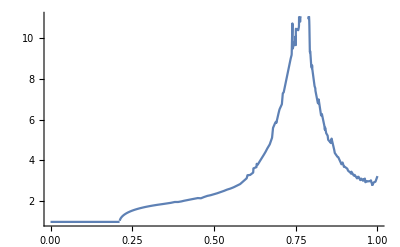

```mathematica
Plot[NeffFunction[ma GeV],{ma,0,1}]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Max::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Max :: nord will be suppressed during this calculation.

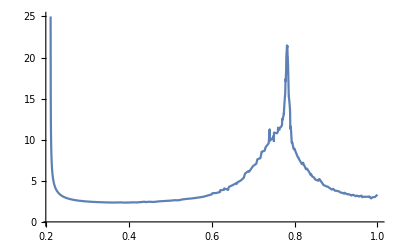

```mathematica
Plot[NeffFunctionMuon[ma GeV],{ma,0.01,1},PlotRange->{0,25}]
```

```mathematica
cτ[m_,ϵ_]:=3/(α ϵ^2 m GeV NeffFunction[m GeV]) /.inMM
γcτ[m_,ϵ_,En_:5.5]:=3/(α ϵ^2 m GeV NeffFunction[m GeV]) (En GeV)/(m GeV)/.inMM
```

```mathematica
NeffFunction[ee,mA_]:=NeffFunction[mA]
NeffFunction[μμ,mA_]:=NeffFunctionMuon[mA]
m0[ee]=0.;
```

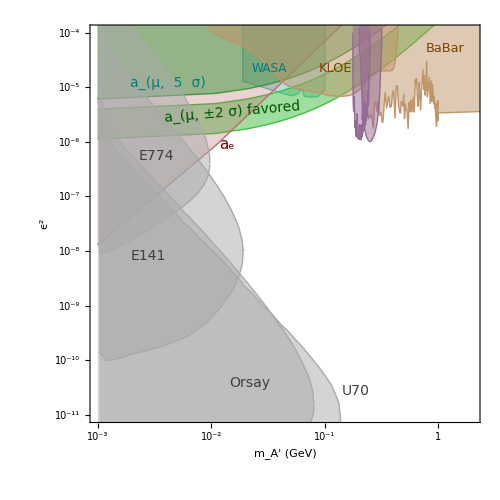
```mathematica
m0[μμ]=0.;
comboFromRouvenFeb2014=-Graphics-;
```

## Non-Parasitic Reach

### Run Constants

```mathematica
T[_,6.6,_]=0.0025; (* target thickness in radiation lengths *)
T[_,2.2,_]=0.00125; (* target thickness in radiation lengths *)
T[_,4.4,_]=0.0025; (* target thickness in radiation lengths *)
T[_,1.1,_]=0.00125;
```

```mathematica
EffMat0[Full]=0.005;
EffMat0[Test]=0.005;
```

```mathematica
beamSpot=20.0*10^-6; (*20 um*)

L = 0.1 ;  (* 10 cm *)
dpOverp[1.1,Test]=0.08;
dpOverp[2.2,Test]=0.04  (* changed from 0.03 7/18/2012/ *)
dpOverp[2.2,Full]=0.03;
dpOverp[6.6,Full]=0.015;  (* changed from 0.03 7/18/2012/ *)
dpOverp[_,Gen]=0.01;  (* dummy *)
RecoEfficiency=0.85;
nMonths[Full] = 0.25;
nMonths[Gen] = 1.0;
Nelectron[_,1.1,Run_]:=nMonths[Run]50 nA 3*10^6 SEC;
Nelectron[_,2.2,Run_]:=nMonths[Run]200 nA 3*10^6 SEC;
Nelectron[_,4.4,Run_]:=nMonths[Run]300 nA 3*10^6 SEC;
Nelectron[_,6.6,Run_]:=nMonths[Run]450 nA 3*10^6 SEC;
```

0.04

### Mass Data

```mathematica
(*  These numbers were for the HPS-Prime* detectors *)
SigmaMdata[ee,NoBS,1.1,Full]={{0.01,0.000955602},{0.02,0.00168917},{0.03,0.00211266},{0.04,0.00244738},{0.05,0.00274674},{0.06,0.00311293},{0.07,0.00342416},{0.08,0.00370191},{0.09,0.00363934},{0.1,0.00408088}};
SigmaMdata[ee,BS,1.1,Full]={{0.01,0.000504113},{0.01,0.000504113},{0.02,0.000895473},{0.03,0.00131617},{0.04,0.00176202},{0.05,0.00219393},{0.06,0.00265356},{0.07,0.00308415},{0.08,0.00348599},{0.09,0.00354437},{0.1,0.00408512}};
SigmaMdata[ee,NoBS,2.2,Full]={{0.04,0.00202127},{0.05,0.00221679},{0.06,0.00240364},{0.07,0.00265138},{0.08,0.00277603},{0.09,0.00276567},{0.1,0.0028931},{0.11,0.00305742},{0.12,0.00322297},{0.13,0.00339782}};
SigmaMdata[ee,BS,2.2,Full]={{0.04,0.000995135},{0.04,0.000995135},{0.05,0.00121764},{0.06,0.00145849},{0.07,0.0016969},{0.08,0.0019286},{0.09,0.00202524},{0.1,0.00226026},{0.11,0.00247384},{0.12,0.00270209},{0.13,0.00292839}};
SigmaMdata[ee,NoBS,4.4,Full]={{0.05,0.00244494},{0.06,0.00255083},{0.07,0.00264566},{0.08,0.00262025},{0.09,0.00235913},{0.1,0.00238422},{0.11,0.00244421},{0.12,0.00253579},{0.13,0.00261873},{0.14,0.00279368},{0.16,0.00292795},{0.17,0.00301437},{0.18,0.00311798},{0.19,0.00320705},{0.2,0.00327796}};
SigmaMdata[ee,BS,4.4,Full]={{0.05,0.00090896},{0.05,0.00090896},{0.06,0.000932897},{0.07,0.00100356},{0.08,0.00114001},{0.09,0.00126945},{0.1,0.00140524},{0.11,0.00153378},{0.12,0.00166297},{0.13,0.0017632},{0.14,0.00190143},{0.16,0.00212793},{0.17,0.00225101},{0.18,0.00237076},{0.19,0.00249395},{0.2,0.00259483}};
SigmaMdata[ee,NoBS,6.6,Full]={{0.08,0.00261153},{0.1,0.00232602},{0.125,0.00241825},{0.15,0.00258677},{0.175,0.00277136},{0.2,0.00296449},{0.225,0.00314652},{0.25,0.0033339},{0.275,0.00350594}};
SigmaMdata[ee,BS,6.6,Full]={{0.08,0.00090848},{0.08,0.00090848},{0.1,0.00104147},{0.125,0.00126978},{0.15,0.0015174},{0.175,0.00174012},{0.2,0.00198006},{0.225,0.00221574},{0.25,0.00244377},{0.275,0.00267895}};

SigmaMdata[μμ,NoBS,6.6,Full]={{0.215,0.000693578},{0.225,0.00135447},{0.25,0.00173014},{0.275,0.00188259},{0.3,0.00225885},{0.35,0.00286517},{0.4,0.00330635}};
SigmaMdata[μμ,BS,6.6,Full]={{0.215,0.00048611},{0.215,0.00048611},{0.225,0.000683796},{0.25,0.00101486},{0.275,0.00135302},{0.3,0.00167526},{0.35,0.00228521},{0.4,0.00279194}};
```

### Mass Resolution

```mathematica
fitSigmaM[mode_,Reg_,E0_,Run_]:=Fit[SigmaMdata[mode,Reg,E0,Run],{1,mm},mm];
sigmaMFit[mode_,Reg_,E0_,m_,Run_]:=fitSigmaM[mode,Reg,E0,Run]/.mm->m;
deltaMFit[mode_,m_,Reg_, E0_, Run_,massOptimism_:1,multiplier_:2.5]:=sigmaMFit[mode,Reg,E0,m,Run]*multiplier*massOptimism;
```

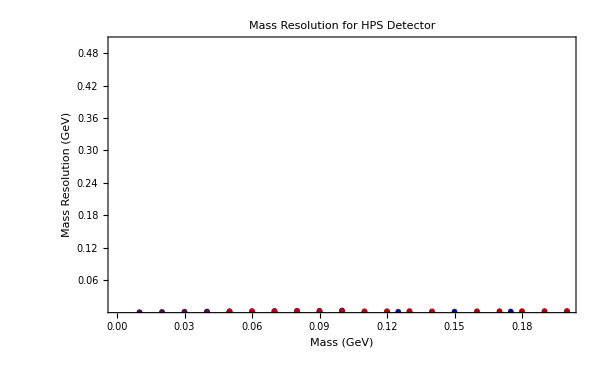

```mathematica
p=Plot[{sigmaMFit[ee,BS,2.2,m,Full],sigmaMFit[ee,NoBS,2.2,m,Full],sigmaMFit[ee,BS,6.6,m,Full],sigmaMFit[ee,NoBS,6.6,m,Full]},{m,0.01,0.50},PlotLabel->Style["2.2 and 6.6 GeV Mass Resolution for Full Detector",16],Frame->True,FrameLabel->{"Mass (GeV)","Mass Resolution (GeV)"},LabelStyle->16,PlotRange->{{0.010,0.500}},PlotStyle->{{Red,Thick},{Red,Thick,Dashed},{Blue,Thick},{Blue,Thick,Dashing[Large]}},Axes->False];
p1pt1=Plot[{sigmaMFit[ee,BS,1.1,m,Full],sigmaMFit[ee,NoBS,1.1,m,Full]},{m,0.01,0.20},PlotLabel->Style["1.1 GeV Mass Resolution for Full Detector",16],Frame->True,FrameLabel->{"Mass (GeV)","Mass Resolution (GeV)"},LabelStyle->16,PlotRange->{{0.010,0.300}},PlotStyle->{{Purple,Thick},{Purple,Thick,Dashing[Large]}},Axes->False];
p2pt2=Plot[{sigmaMFit[ee,BS,2.2,m,Full],sigmaMFit[ee,NoBS,2.2,m,Full]},{m,0.01,0.20},PlotLabel->Style["Mass Resolution for HPS Detector",16],Frame->True,FrameLabel->{"Mass (GeV)","Mass Resolution (GeV)"},LabelStyle->16,PlotRange->{{0.010,0.500}},PlotStyle->{{Red,Thick},{Red,Thick,Dashing[Large]}},Axes->False,BaseStyle->{FontWeight->"Bold",FontSize->14},ImageSize->600];
p4pt4=Plot[{sigmaMFit[ee,BS,4.4,m,Full],sigmaMFit[ee,NoBS,4.4,m,Full]},{m,0.01,0.20},PlotLabel->Style["1.1, 2.2 and 6.6 GeV Mass Resolution for Full Detector",16],Frame->True,FrameLabel->{"Mass (GeV)","Mass Resolution (GeV)"},LabelStyle->16,PlotRange->{{0.010,0.500}},PlotStyle->{{Red,Thick},{Red,Thick,Dashing[Large]}},Axes->False];
p6pt6=Plot[{sigmaMFit[ee,BS,6.6,m,Full],sigmaMFit[ee,NoBS,6.6,m,Full]},{m,0.05,0.5},PlotLabel->Style["1.1, 2.2 and 6.6 GeV Mass Resolution for Full Detector",16],Frame->True,FrameLabel->{"Mass (GeV)","Mass Resolution (GeV)"},LabelStyle->16,PlotRange->{{0.010,0.500}},PlotStyle->{{Blue,Thick},{Blue,Thick,Dashing[Large]}},Axes->False];
p6pt6Muon=Plot[{sigmaMFit[μμ,BS,6.6,m,Full],sigmaMFit[μμ,NoBS,6.6,m,Full]},{m,0.2,0.5},PlotLabel->Style["1.1, 2.2 and 6.6 GeV Mass Resolution for Full Detector",16],Frame->True,FrameLabel->{"Mass (GeV)","Mass Resolution (GeV)"},LabelStyle->16,PlotRange->{{0.010,0.500}},PlotStyle->{{Darker[Green],Thick},{Green,Thick,Dashing[Large]}},Axes->False];
gs=ListPlot[SigmaMdata[ee,NoBS,6.6,Full],PlotMarkers->{Automatic,Medium}];
gsBS=ListPlot[SigmaMdata[ee,BS,6.6,Full],PlotMarkers->{Automatic,Medium},PlotStyle->Darker[Blue]];
gs22=ListPlot[SigmaMdata[ee,NoBS,2.2,Full],PlotMarkers->{Automatic,Medium},PlotStyle->Pink];
gs22BS=ListPlot[SigmaMdata[ee,BS,2.2,Full],PlotMarkers->{Automatic,Medium},PlotStyle->Darker[Pink]];
gs44=ListPlot[SigmaMdata[ee,NoBS,4.4,Full],PlotMarkers->{Automatic,Medium},PlotStyle->Red];
gs44BS=ListPlot[SigmaMdata[ee,BS,4.4,Full],PlotMarkers->{Automatic,Medium},PlotStyle->Darker[Red]];
gs11=ListPlot[SigmaMdata[ee,NoBS,1.1,Full],PlotMarkers->{Automatic,Medium},PlotStyle->Purple];
gs11BS=ListPlot[SigmaMdata[ee,BS,1.1,Full],PlotMarkers->{Automatic,Medium},PlotStyle->Darker[Purple]];
gs66Muon=ListPlot[SigmaMdata[μμ,NoBS,6.6,Full],PlotMarkers->{Automatic,Medium},PlotStyle->Green];
gs66MuonBS=ListPlot[SigmaMdata[μμ,BS,6.6,Full],PlotMarkers->{Automatic,Medium},PlotStyle->Darker[Green]];Show[ p2pt2,p6pt6,gs,gsBS,gs22,gs22BS,p1pt1,gs11,gs11BS,p4pt4,gs44,gs44BS,gs66Muon,gs66MuonBS,p6pt6Muon,ImageSize->600]
```

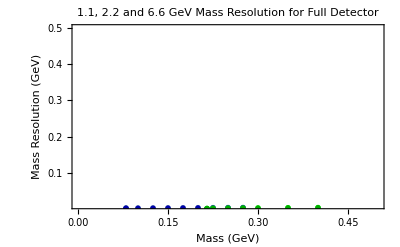

```mathematica
Show[ p6pt6,gs,gsBS,gs66Muon,gs66MuonBS,p6pt6Muon]
```

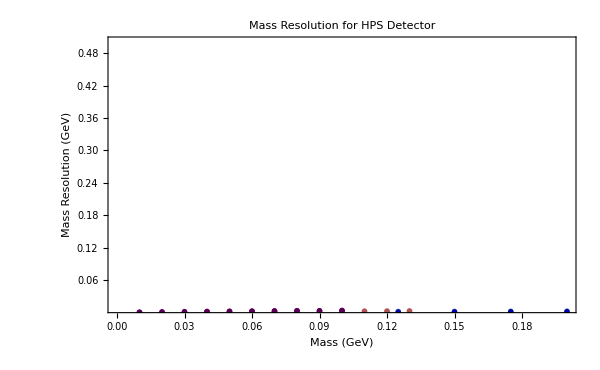

```mathematica
Show[ p2pt2,p6pt6,gs,gsBS,gs22,gs22BS,p1pt1,gs11,gs11BS,gs66Muon,gs66MuonBS,p6pt6Muon,ImageSize->600]
```

### Rate Helper functions

```mathematica
Lumi[cond_,E0_,Run_]:=Nelectron[cond,E0,Run](NAvo T[cond,E0,Run] Xzero[W])/A[W]  (10^-9 barn)/nb  (* in inverse nb *);
Rate[T_,Current_(*in nA*)]:=Current*nA(NAvo T Xzero[W])/A[W]  (10^-9 barn)/nb;
```

```mathematica
TotalStatistics[mode_,E0_,Run_,BkgMode_:BH]:=Lumi[mode,E0,Run]*TotalBKGXS[mode,E0,Run,BkgMode]*RecoEfficiency^2
RadStatistics[mode_,E0_,Run_]:=Lumi[mode,E0,Run]*radXS[mode,E0,Run]*RecoEfficiency^2
BHStatistics[mode_,E0_,Run_]:=Lumi[mode,E0,Run]*BHXS[mode,E0,Run]*RecoEfficiency^2
RadFraction[mode_,E0_,Run_,BkgMode_]:=radXS[mode,E0,Run]/(TotalBKGXS[mode,E0,Run,BkgMode])
```

```mathematica
tridentRecoRate[mode_,E0_,Run_]:=Rate[T[mode,E0,Run],400]*TotalBKGXS[mode,E0,Run]*RecoEfficiency^2
```

### Cross-sections:

New cross-section calculations...Oct 2012 by mg...

#### 1.1 GeV for proposed 2014 detector with 0.25T field

```mathematica
radXS[ee,1.1,Gen]=.42262*10^8/1000.0 *nb(* divide by 1000 to go from MadGraph (pb) to nb *)
radEff[ee,1.1,Gen]=1.0;
radEff[ee,1.1,Full]=2115604/9378181.0
```

42262. nb

0.225588

```mathematica
(* Using Takahi's new, correct MadGraph...for Radiative, use only the gamma* e+e-...should be same (similar) as before*)
radXS[ee,1.1,Gen]=33900*nb
radEff[ee,1.1,Gen]=1.0;
radEff[ee,1.1,Full]=228439/965241.0
radXS[ee,1.1,Full]=radXS[ee,1.1,Gen]*radEff[ee,1.1,Full]
```

33900 nb

0.236665

8022.95 nb

```mathematica
FullTriXS[ee,1.1,Gen]=538000 *nb
FullTriEff[ee,1.1,Gen]=1.0;
FullTriEff[ee,1.1,Full]=68990/768398.0*2 (* x2 because the there are 2 pairs per event *)
FullTriXS[ee,1.1,Full]=FullTriXS[ee,1.1,Gen]*FullTriEff[ee,1.1,Full]
```

538000 nb

0.179568

96607.8 nb

```mathematica
BHXS[ee,1.1,Gen]=.88653*10^8/1000.0 *nb(* divide by 1000 to go from MadGraph (pb) to nb *)
BHEff[ee,1.1,Gen]=1.0;
BHEff[ee,1.1,Full]=3043415/9812479.0
```

88653. nb

0.310158

```mathematica
radXS[ee,1.1,Full]=radXS[ee,1.1,Gen]*radEff[ee,1.1,Full]
BHXS[ee,1.1,Full]=BHXS[ee,1.1,Gen]*BHEff[ee,1.1,Full]
TotalBKGXS[ee,1.1,Full,FullTri]=FullTriXS[ee,1.1,Full]
TotalBKGXS[ee,1.1,Full,BH]=radXS[ee,1.1,Full]+BHXS[ee,1.1,Full]
```

8022.95 nb

27496.4 nb

96607.8 nb

35519.4 nb

#### 2.2 GeV for proposed 2014 detector with 0.5T field

```mathematica
(*radXS[ee,2.2,Gen]=1.112*10^7/1000.0 *nb(* divide by 1000 to go from MadGraph (pb) to nb *)
radEff[ee,2.2,Gen]=1.0;
radEff[ee,2.2,Full]=1692050/8137941.0*)
```

```mathematica
(*radXS[ee,2.2,Full]=radXS[ee,2.2,Gen]*radEff[ee,2.2,Full]
BHXS[ee,2.2,Full]=BHXS[ee,2.2,Gen]*BHEff[ee,2.2,Full]
TotalBKGXS[ee,2.2,Full]=radXS[ee,2.2,Full]+BHXS[ee,2.2,Full]
  RadFraction[ee,2.2,Full]=radXS[ee,2.2,Full]/(BHXS[ee,2.2,Full]+radXS[ee,2.2,Full])  
*)
```

```mathematica
(* Using Takashi's new, correct MadGraph...for Radiative, use only the gamma* e+e-...should be same (similar) as before*)
radXS[ee,2.2,Gen]=8100*nb
radEff[ee,2.2,Gen]=1.0;
radEff[ee,2.2,Full]=236798/980575.0
radXS[ee,2.2,Full]=radXS[ee,2.2,Gen]*radEff[ee,2.2,Full]
```

8100 nb

0.241489

1956.06 nb

```mathematica
BHXS[ee,2.2,Gen]=0.2814*10^8/1000.0 *nb(* divide by 1000 to go from MadGraph (pb) to nb *)
BHEff[ee,2.2,Gen]=1.0;
BHEff[ee,2.2,Full]=2875983/9646817.0
BHXS[ee,2.2,Full]=BHXS[ee,2.2,Gen]*BHEff[ee,2.2,Full]
```

28140. nb

0.298128

8389.31 nb

```mathematica
FullTriXS[ee,2.2,Gen]=130000 *nb
FullTriEff[ee,2.2,Gen]=1.0;
FullTriEff[ee,2.2,Full]=72107/742770.0*2 (* x2 because the there are 2 pairs per event *)
FullTriXS[ee,2.2,Full]=FullTriXS[ee,2.2,Gen]*FullTriEff[ee,2.2,Full]
```

130000 nb

0.194157

25240.4 nb

```mathematica
TotalBKGXS[ee,2.2,Full,FullTri]=FullTriXS[ee,2.2,Full]
TotalBKGXS[ee,2.2,Full,BH]=radXS[ee,2.2,Full]+BHXS[ee,2.2,Full]
```

25240.4 nb

10345.4 nb

```mathematica
RadFraction[ee,2.2,Full,BH]
RadFraction[ee,2.2,Full,FullTri]
```

0.189076

0.0774972

#### 4.4 GeV for proposed 2014 detector with 1T field

```mathematica
(* radXS[ee,4.4,Gen]=.2701*10^7/1000.0 *nb(* divide by 1000 to go from MadGraph (pb) to nb *)
radEff[ee,4.4,Gen]=1.0; *)
(*  radEff[ee,4.4,Full]=1209714/1980000.0 ...this number is wrong! *)
```

```mathematica
(* Using Takahi's new, correct MadGraph...for Radiative, use only the gamma* e+e-...should be same (similar) as before*)
radXS[ee,4.4,Gen]=1840*nb
radEff[ee,4.4,Gen]=1.0;
radEff[ee,4.4,Full]=221140/936495.0
radXS[ee,4.4,Full]=radXS[ee,4.4,Gen]*radEff[ee,4.4,Full]
```

1840 nb

0.236136

434.49 nb

```mathematica
BHXS[ee,4.4,Gen]=.7468*10^7/1000.0 *nb(* divide by 1000 to go from MadGraph (pb) to nb *)
BHEff[ee,4.4,Gen]=1.0;
BHEff[ee,4.4,Full]=2613710/9010945.0
BHXS[ee,4.4,Full]=BHXS[ee,4.4,Gen]*BHEff[ee,4.4,Full]
```

7468. nb

0.290059

2166.16 nb

```mathematica
FullTriXS[ee,4.4,Gen]=31400 *nb
FullTriEff[ee,4.4,Gen]=1.0;
FullTriEff[ee,4.4,Full]=69151/696167.0*2 (* x2 because the there are 2 pairs per event *)
FullTriXS[ee,4.4,Full]=FullTriXS[ee,4.4,Gen]*FullTriEff[ee,4.4,Full]
```

31400 nb

0.198662

6237.99 nb

```mathematica
TotalBKGXS[ee,4.4,Full,FullTri]=FullTriXS[ee,4.4,Full]
TotalBKGXS[ee,4.4,Full,BH]=radXS[ee,4.4,Full]+BHXS[ee,4.4,Full]
RadFraction[ee,4.4,Full,BH]
RadFraction[ee,4.4,Full,FullTri]
```

6237.99 nb

2600.65 nb

0.167069

0.0696522

#### 6.6 GeV for proposed 2014 detector with 1.5T field

```mathematica
(* radXS[ee,6.6,Gen]=1.007*10^6/1000.0 *nb(* divide by 1000 to go from MadGraph (pb) to nb *)
radEff[ee,6.6,Gen]=1.0;
radEff[ee,6.6,Full]=1077954/6034347.0 *)
```

```mathematica
(* Using Takahi's new, correct MadGraph...for Radiative, use only the gamma* e+e-...should be same (similar) as before*)
radXS[ee,6.6,Gen]=730*nb
radEff[ee,6.6,Gen]=1.0;
radEff[ee,6.6,Full]=202492/870628.0
radXS[ee,6.6,Full]=radXS[ee,6.6,Gen]*radEff[ee,6.6,Full]
```

730 nb

0.232582

169.785 nb

```mathematica
FullTriXS[ee,6.6,Gen]=12700 *nb
FullTriEff[ee,6.6,Gen]=1.0;
FullTriEff[ee,6.6,Full]=67181/666467.0*2 (* x2 because the there are 2 pairs per event *)
FullTriXS[ee,6.6,Full]=FullTriXS[ee,6.6,Gen]*FullTriEff[ee,6.6,Full]
```

12700 nb

0.201603

2560.36 nb

```mathematica
BHXS[ee,6.6,Gen]=0.319*10^7/1000.0 *nb(* divide by 1000 to go from MadGraph (pb) to nb *)
BHEff[ee,6.6,Gen]=1.0;
BHEff[ee,6.6,Full]=2453644/8618308.0
```

3190. nb

0.284701

```mathematica
radXS[ee,6.6,Full]=radXS[ee,6.6,Gen]*radEff[ee,6.6,Full]
BHXS[ee,6.6,Full]=BHXS[ee,6.6,Gen]*BHEff[ee,6.6,Full]
TotalBKGXS[ee,6.6,Full,BH]=radXS[ee,6.6,Full]+BHXS[ee,6.6,Full]
TotalBKGXS[ee,6.6,Full,FullTri]=FullTriXS[ee,6.6,Full]
```

169.785 nb

908.197 nb

1077.98 nb

2560.36 nb

#### 6.6 GeV to muons for proposed 2014 detector with 1.5T field

```mathematica
(* radXS[μμ,6.6,Gen]=.44740*10^5/1000.0 *nb(* divide by 1000 to go from MadGraph (pb) to nb *)
radEff[μμ,6.6,Gen]=1.0;
radEff[μμ,6.6,Full]=3282072/12900966.0 *)
```

```mathematica
(*  radXS[μμ,6.6,Gen]=.47862*10^5/1000.0 *nb(* divide by 1000 to go from MadGraph (pb) to nb *)
radEff[μμ,6.6,Gen]=1.0;
radEff[μμ,6.6,Full]=3968793/15685897.0  *)
```

```mathematica
radXS[μμ,6.6,Gen]=.414*10^5/1000.0 *nb(* divide by 1000 to go from MadGraph (pb) to nb *)
radEff[μμ,6.6,Gen]=1.0;
radEff[μμ,6.6,Full]=3474398/6061489.0
```

41.4 nb

0.573192

```mathematica
BHXS[μμ,6.6,Gen]=.78621*10^6/1000.0 *nb(* divide by 1000 to go from MadGraph (pb) to nb *)
BHEff[μμ,6.6,Gen]=1.0;
BHEff[μμ,6.6,Full]=1846523/9990810.0
```

786.21 nb

0.184822

```mathematica
radXS[μμ,6.6,Full]=radXS[μμ,6.6,Gen]*radEff[μμ,6.6,Full]
BHXS[μμ,6.6,Full]=BHXS[μμ,6.6,Gen]*BHEff[μμ,6.6,Full]
TotalBKGXS[μμ,6.6,Full,BH]=radXS[μμ,6.6,Full]+BHXS[μμ,6.6,Full]
```

23.7302 nb

145.309 nb

169.039 nb

### Mass Distribtion Tabulation and Display Functions

Basic processing of input files.

```mathematica
(*massdata[mode_,2.2,bkg_,Run_]:=Table[{m0[mode]+i*2.5-1.25,mass[mode,2.2,bkg,Run][[i]]},{i,1,160,1}];
massdata[mode_,4.4,bkg_,Run_]:=Table[{m0[mode]+i*1.0-0.5,mass[mode,4.4,bkg,Run][[i]]},{i,1,500,1}];
massdata[mode_,1.1,bkg_,Run_]:=Table[{m0[mode]+i*1.0-0.5,mass[mode,1.1,bkg,Run][[i]]},{i,1,200,1}];
massdata[ee,6.6,bkg_,Run_]:=Table[{m0[ee]+i*2.5-1.25,mass[ee,6.6,bkg,Run][[i]]},{i,1,400,1}];
massdata[μμ,6.6,bkg_,Run_]:=Table[{m0[μμ]+i*2.5-1.25,mass[μμ,6.6,bkg,Run][[i]]},{i,1,800,1}]; *)
```

```mathematica
massdata[mode_,E0_,bkg_,Run_]:=Table[{m0[mode]+i*1.0-0.5,mass[mode,E0,bkg,Run][[i]]},{i,1,1000,1}];
```

```mathematica
effdata[mode_,E0_,bkg_,Run_]:=Table[{m0[mode]+i*1.0-0.5,If[mass[mode,E0,bkg,Gen][[i]]>0,mass[mode,E0,bkg,Run][[i]]/mass[mode,E0,bkg,Gen][[i]],0]},{i,1,1000,1}];
```

```mathematica
MakeDistributions[mode_,E0_,Run_]:=Module[{},
TestDist[mode,E0,Rad,Run]=Interpolation[massdata[mode,E0,Rad,Run],InterpolationOrder->0];
TestDist[mode,E0,BH,Run]=Interpolation[massdata[mode,E0,BH,Run],InterpolationOrder->0];
 TestDist[mode,E0,FullTri,Run]=Interpolation[massdata[mode,E0,FullTri,Run],InterpolationOrder->0]; 
Normalization[mode,E0,Rad,Run]=NIntegrate[TestDist[mode,E0,Rad,Run][x],{x,2,1000}];
Normalization[mode,E0,BH,Run]=NIntegrate[TestDist[mode,E0,BH,Run][x],{x,2,1000}];
 Normalization[mode,E0,FullTri,Run]=NIntegrate[TestDist[mode,E0,FullTri,Run][x],{x,10,1000}]; 
];


RadToBHratio[mode_,E0_,Run_][x_]:=If[TestDist[mode,E0,BH,Run][x]==0,1,(TestDist[mode,E0,Rad,Run][x])/Normalization[mode,E0,Rad,Run]*((TestDist[mode,E0,BH,Run][x])/Normalization[mode,E0,BH,Run])^-1*RadFraction[mode,E0,Run,BH]]
```

```mathematica
RadToFullratio[mode_,E0_,Run_][x_]:=If[TestDist[mode,E0,FullTri,Run][x]==0,1,(TestDist[mode,E0,Rad,Run][x])/Normalization[mode,E0,Rad,Run]*((TestDist[mode,E0,FullTri,Run][x])/Normalization[mode,E0,FullTri,Run])^-1*RadFraction[mode,E0,Run,FullTri]]
```

For display of diagnostic plots (see below)

```mathematica
MassDistTest[mode_,E0_,Run_,minX_:30, maxX_:200]:=Module[{},
{Plot[{(TestDist[mode,E0,Rad,Run][x])/Normalization[mode,E0,Rad,Run],(TestDist[mode,E0,BH,Run][x])/Normalization[mode,E0,BH,Run]},{x,minX,maxX},PlotRange->{{minX,maxX},{0,0.25}},PlotStyle->Thick,PlotLabel->ToString[mode]<>" ("<>ToString[E0]<>" GeV) Rad & BH" ],
Plot[{RadToBHratio[mode,E0,Run][x],RadFraction[mode,E0,Run,BH]},{x,minX,maxX},PlotRange->{{minX,maxX},{0,2*RadFraction[mode,E0,Run,BH]}},PlotStyle->{Thick,Thin},PlotLabel->ToString[mode]<>" ("<>ToString[E0]<>" GeV) Rad/BH" ]
}]
```

```mathematica
MassDistTestFullTri[mode_,E0_,Run_,minX_:30, maxX_:200]:=Module[{},
{Plot[{(TestDist[mode,E0,Rad,Run][x])/Normalization[mode,E0,Rad,Run],(TestDist[mode,E0,FullTri,Run][x])/Normalization[mode,E0,FullTri,Run]},{x,minX,maxX},PlotRange->{{minX,maxX},{0,0.1}},PlotStyle->Thick,ImageSize->400,PlotLabel->ToString[mode]<>" ("<>ToString[E0]<>" GeV) Rad & Full Trident" ],
Plot[{RadToFullratio[mode,E0,Run][x],RadFraction[mode,E0,Run,FullTri]},{x,30,200},PlotRange->{{minX,maxX},{0,2*RadFraction[mode,E0,Run,FullTri]}},ImageSize->400,PlotStyle->{Thick,Thin},PlotLabel->ToString[mode]<>" ("<>ToString[E0]<>" GeV) Rad/Full" ]
}]
```

```mathematica
MassDisteeVsmm[E0_,Run_,minX_:100, maxX_:500]:=Module[{},
{Plot[{(TestDist[ee,E0,Rad,Run][x])/Normalization[ee,E0,Rad,Run]*radXS[ee,E0,Run]/nb,(TestDist[μμ,E0,Rad,Run][x])/Normalization[μμ,E0,Rad,Run]*radXS[μμ,E0,Run]/nb},{x,minX,maxX},PlotRange->{{minX,maxX},{10^-4,0.5}},PlotStyle->Thick,PlotLabel->"6.6 GeV: Radiative Cross-section ee & μμ",Frame->True,FrameLabel->{"Mass (MeV)","Radiative Cross Section (nb)"},BaseStyle->{FontWeight->"Bold",FontSize->14},ImageSize->600 ]
}]
```

```mathematica
MassDistRadXS[E0_,Run_,minX_:100, maxX_:500]:=Module[{},
{LogPlot[{(TestDist[ee,E0,Rad,Run][x])/Normalization[ee,E0,Rad,Run]*radXS[ee,E0,Run]/nb},{x,minX,maxX},PlotRange->{{minX,maxX},{10^-4,500.0}},PlotStyle->{Blue,myThick},PlotLabel->"Radiative Cross-section",Frame->True,FrameLabel->{"Mass (MeV)","Radiative Cross Section (nb)"},BaseStyle->{FontWeight->"Bold",FontSize->14},ImageSize->600 ]
}]
```

```mathematica
MassDistBHXS[E0_,Run_,minX_:100, maxX_:500]:=Module[{},
{LogPlot[{(TestDist[ee,E0,BH,Run][x])/Normalization[ee,E0,BH,Run]*BHXS[ee,E0,Run]/nb},{x,minX,maxX},PlotRange->{{minX,maxX},{10^-4,5000.0}},PlotStyle->{Blue,myThick},Frame->True,FrameLabel->{"Mass (MeV)","Cross Section (nb)"},BaseStyle->{FontWeight->"Bold",FontSize->14},ImageSize->600 ]
}]
```

### Raw data -- CHANGE FILENAMES HERE AS NEEDED

```mathematica
(* mass[ee,2.2,Rad,Full]=Flatten[Import["rad2.2gev0.5t_after.dat"]];
mass[ee,2.2,BH,Full]=Flatten[Import["bh2.2gev0.5t_after.dat"]];
MakeDistributions[ee,2.2,Full]; *)

(* mass[ee,2.2,Rad,Full]=Flatten[Import[MassDataDir<>"/Rad2pt2_Full.dat"]];
mass[ee,2.2,BH,Full]=Flatten[Import[MassDataDir<>"/BH2pt2_Full.dat"]];
(* mass[ee,2.2,FullTri,Full]=Flatten[Import["/Users/mgraham/HPS/HPS-Reach/datfiles-from-me/FullTri2pt2_Full.dat"]]; *)
MakeDistributions[ee,2.2,Full]; *)

mass[ee,2.2,Rad,Full]=Flatten[Import["/Users/mgraham/HPS/Reach/Acceptance-FixBackgroundTridents/GammaStarElectronsOnly/RadComp2pt2_Full.dat"]];
mass[ee,2.2,BH,Full]=Flatten[Import["/Users/mgraham/HPS/Reach/Acceptance-Jan7-2013/BH2pt2_Full.dat" ]];
mass[ee,2.2,FullTri,Full]=Flatten[Import["/Users/mgraham/HPS/Reach/Acceptance-FixBackgroundTridents/BothElectrons/TriComp2pt2_Full.dat"]];
```

```mathematica
MakeDistributions[ee,2.2,Full];
```

```mathematica
mass[ee,6.6,Rad,Full]=Flatten[Import["/Users/mgraham/HPS/Reach/Acceptance-FixBackgroundTridents/GammaStarElectronsOnly/RadComp6pt6_Full.dat"]];
mass[ee,6.6,Rad,Gen]=Flatten[Import["/Users/mgraham/HPS/Reach/Acceptance-FixBackgroundTridents/GammaStarElectronsOnly/RadComp6pt6_generated.dat"]];
(* mass[ee,6.6,Rad,Full]=Flatten[Import[MassDataDir<>"/Rad6pt6_Full.dat"]];
mass[ee,6.6,Rad,Gen]=Flatten[Import[MassDataDir<>"/Rad6pt6_generated.dat"]];*)
mass[ee,6.6,BH,Full]=Flatten[Import["/Users/mgraham/HPS/Reach/Acceptance-Jan7-2013/BH6pt6_Full.dat" ]];
mass[ee,6.6,BH,Gen]=Flatten[Import["/Users/mgraham/HPS/Reach/Acceptance-Jan7-2013/BH6pt6_generated.dat" ]];
mass[ee,6.6,FullTri,Full]=Flatten[Import["/Users/mgraham/HPS/Reach/Acceptance-FixBackgroundTridents/BothElectrons/TriComp6pt6_Full.dat"]]; 
(* mass[ee,2.2,FullTri,Full]=Flatten[Import["/Users/mgraham/HPS/Reach/datfiles-from-me/FullTri2pt2_Full.dat"]]; *)
MakeDistributions[ee,6.6,Full];
```

```mathematica
(* mass[ee,1.1,Rad,Full]=Flatten[Import[MassDataDir<>"/Rad1pt1_Full.dat"]]; *)
mass[ee,1.1,Rad,Full]=Flatten[Import["/Users/mgraham/HPS/Reach/Acceptance-FixBackgroundTridents/GammaStarElectronsOnly/RadComp1pt1_Full.dat"]];
mass[ee,1.1,BH,Full]=Flatten[Import["/Users/mgraham/HPS/Reach/Acceptance-Jan7-2013/BH1pt1_Full.dat" ]]; mass[ee,1.1,FullTri,Full]=Flatten[Import["/Users/mgraham/HPS/Reach/Acceptance-FixBackgroundTridents/BothElectrons/TriComp1pt1_Full.dat"]]; 
(* mass[ee,2.2,FullTri,Full]=Flatten[Import["/Users/mgraham/HPS/Reach/datfiles-from-me/FullTri2pt2_Full.dat"]]; *)
MakeDistributions[ee,1.1,Full];
```

```mathematica
mass[ee,4.4,Rad,Full]=Flatten[Import["/Users/mgraham/HPS/Reach/Acceptance-FixBackgroundTridents/GammaStarElectronsOnly/RadComp4pt4_Full.dat"]];
mass[ee,4.4,BH,Full]=Flatten[Import["/Users/mgraham/HPS/Reach/Acceptance-Jan7-2013/BH4pt4_Full.dat" ]]; mass[ee,4.4,FullTri,Full]=Flatten[Import["/Users/mgraham/HPS/Reach/Acceptance-FixBackgroundTridents/BothElectrons/TriComp4pt4_Full.dat"]]; 
(* mass[ee,2.2,FullTri,Full]=Flatten[Import["/Users/mgraham/HPS/Reach/datfiles-from-me/FullTri2pt2_Full.dat"]]; *)
MakeDistributions[ee,4.4,Full];
```

```mathematica
mass[μμ,6.6,Rad,Full]=Flatten[Import["/Users/mgraham/HPS/Reach/Acceptance-Jan7-2013/RadMuon6pt6_Full.dat"]];
mass[μμ,6.6,Rad,Gen]=Flatten[Import["/Users/mgraham/HPS/Reach/Acceptance-Jan7-2013/RadMuon6pt6_generated.dat"]];
mass[μμ,6.6,BH,Full]=Flatten[Import["/Users/mgraham/HPS/Reach/Acceptance-Jan7-2013/BHMuon6pt6_Full.dat"]];
mass[μμ,6.6,BH,Gen]=Flatten[Import["/Users/mgraham/HPS/Reach/Acceptance-Jan7-2013/BHMuon6pt6_generated.dat"]];
(* mass[ee,2.2,FullTri,Full]=Flatten[Import["/Users/mgraham/HPS/Reach/datfiles-from-me/FullTri2pt2_Full.dat"]]; *)
MakeDistributions[μμ,6.6,Full];
MakeDistributions[μμ,6.6,Gen];
```

Part::partw: Part 5 of mass[μμ, 6.6, FullTri, Full] does not exist.

Part::partw: Part 6 of mass[μμ, 6.6, FullTri, Full] does not exist.

Part::partw: Part 7 of mass[μμ, 6.6, FullTri, Full] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

NIntegrate::inumr: The integrand TagBox[InterpolatingFunction[{{0.5`, 999.5`}}, {4, 3, 0, {1000}, {1}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{0.5`, 1.5`, « 47 », 49.5`, « 950 »}}, {{μμ}, {6.6`}, {FullTri}, {Full}, {mass[μμ, 6.6`, FullTri, Full] ⟦ 5 ⟧}, {mass[μμ, 6.6`, FullTri, Full] ⟦ 6 ⟧}, « 39 », {mass[μμ, 6.6`, FullTri, Full] ⟦ 46 ⟧}, {mass[μμ, 6.6`, FullTri, Full] ⟦ 47 ⟧}, {mass[μμ, 6.6`, FullTri, Full] ⟦ 48 ⟧}, {mass[μμ, 6.6`, FullTri, Full] ⟦ 49 ⟧}, {mass[μμ, 6.6`, FullTri, Full] ⟦ 50 ⟧}, « 950 »}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{10, 10.5}}.

Part::partw: Part 5 of mass[μμ, 6.6, FullTri, Gen] does not exist.

Part::partw: Part 6 of mass[μμ, 6.6, FullTri, Gen] does not exist.

Part::partw: Part 7 of mass[μμ, 6.6, FullTri, Gen] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

NIntegrate::inumr: The integrand TagBox[InterpolatingFunction[{{0.5`, 999.5`}}, {4, 3, 0, {1000}, {1}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{« 1 »}}, {{μμ}, {6.6`}, {FullTri}, {Gen}, {mass[μμ, 6.6`, FullTri, Gen] ⟦ 5 ⟧}, {mass[μμ, 6.6`, FullTri, Gen] ⟦ 6 ⟧}, {mass[μμ, 6.6`, FullTri, Gen] ⟦ 7 ⟧}, « 38 », {mass[μμ, 6.6`, FullTri, Gen] ⟦ 46 ⟧}, {mass[μμ, 6.6`, FullTri, Gen] ⟦ 47 ⟧}, {mass[μμ, 6.6`, FullTri, Gen] ⟦ 48 ⟧}, {mass[μμ, 6.6`, FullTri, Gen] ⟦ 49 ⟧}, {mass[μμ, 6.6`, FullTri, Gen] ⟦ 50 ⟧}, « 950 »}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{10, 10.5}}.

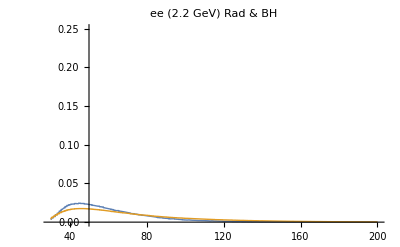
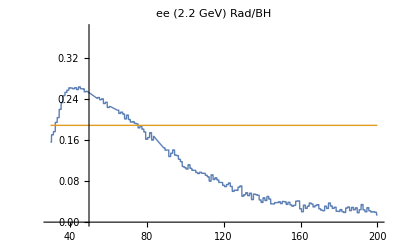

```mathematica
MassDistTest[ee,2.2,Full,30,200]
```

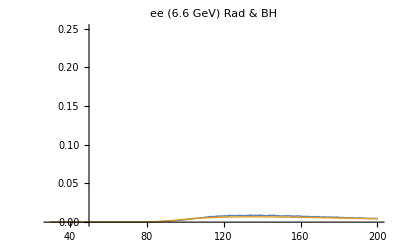
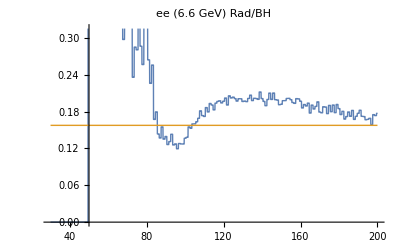

```mathematica
MassDistTest[ee,6.6,Full,30,200]
```

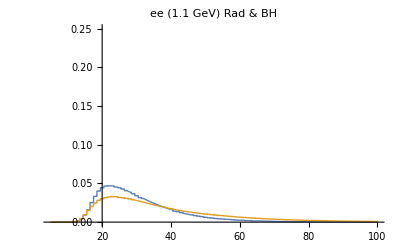
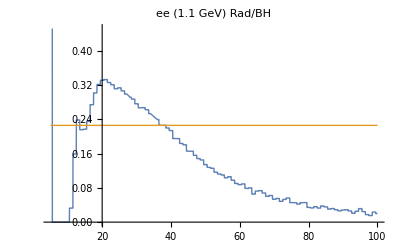

```mathematica
MassDistTest[ee,1.1,Full,5,100]
```

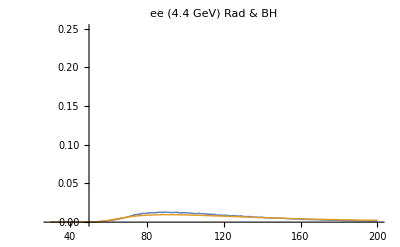
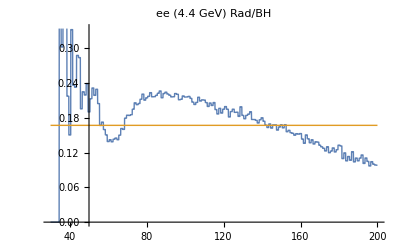

```mathematica
MassDistTest[ee,4.4,Full,30,200]
```

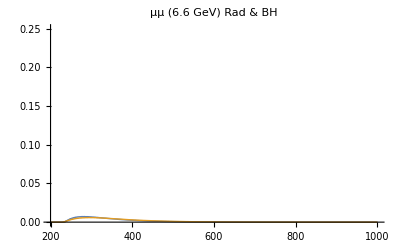
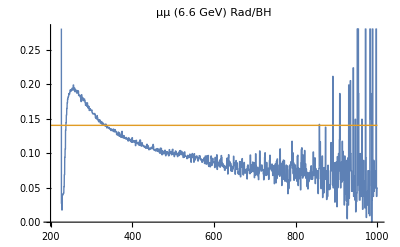

```mathematica
MassDistTest[μμ,6.6,Full,200,1000]
```

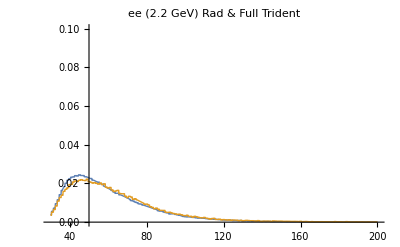
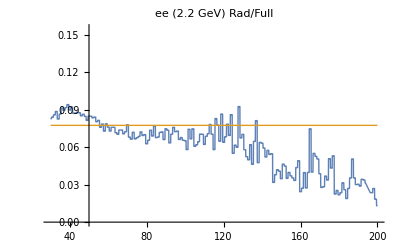

```mathematica
MassDistTestFullTri[ee,2.2,Full,30,200]
```

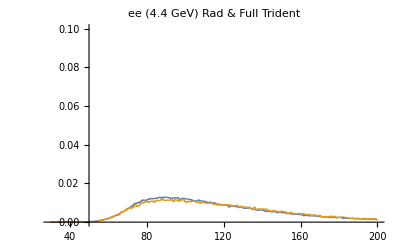
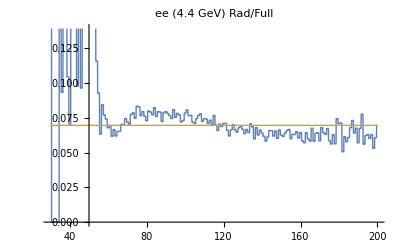

```mathematica
MassDistTestFullTri[ee,4.4,Full,30,200]
```

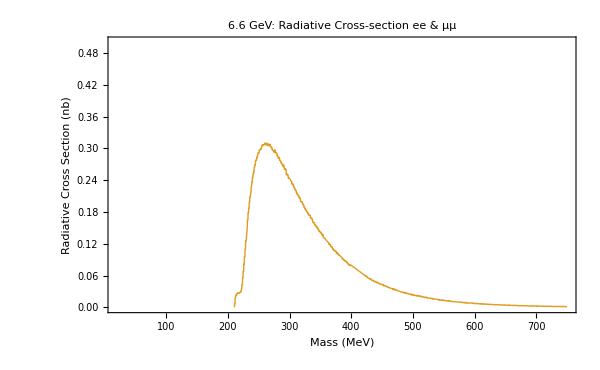

```mathematica
MassDisteeVsmm[6.6,Gen,20,750]
```

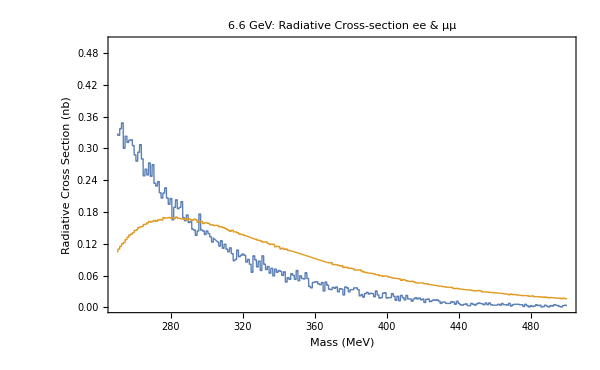

```mathematica
MassDisteeVsmm[6.6,Full,250,500]
```

```mathematica
(* MassDistTestFullTri[ee,2.2,Test] *)
```

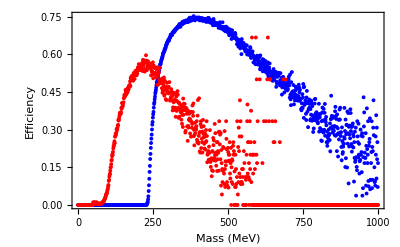

```mathematica
mumuEff=ListPlot[effdata[μμ,6.6,Rad,Full],PlotStyle->{Blue,myThick},Frame->True,FrameLabel->{"Mass (MeV)","Efficiency"}];
eeEff=ListPlot[effdata[ee,6.6,Rad,Full],PlotStyle->{Red,myThick},Frame->True,FrameLabel->{"Mass (MeV)","Efficiency"}];
Show[mumuEff,eeEff]
```

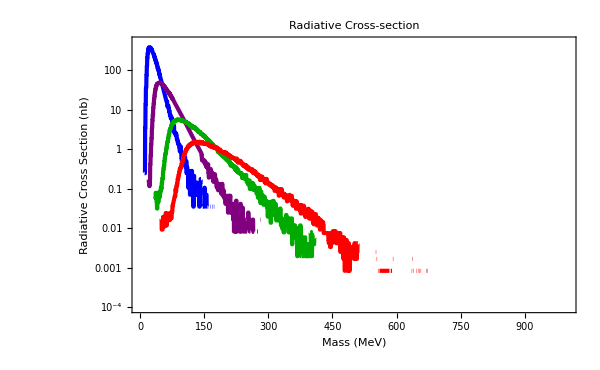

```mathematica
Show[MassDistRadXS[1.1,Full,1,1000]/.myThick->Sequence[Thickness[0.005],Blue],MassDistRadXS[2.2,Full,1,1000]/.myThick->Sequence[Thickness[0.005],Purple],MassDistRadXS[4.4,Full,1,1000]/.myThick->Sequence[Thickness[0.005],Darker[Green]],MassDistRadXS[6.6,Full,1,1000]/.myThick->Sequence[Thickness[0.005],Red]]
```

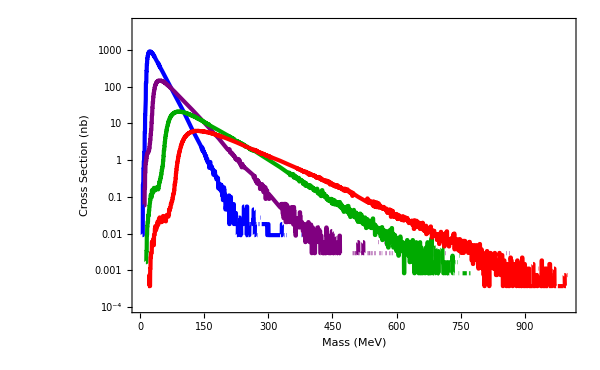

```mathematica
Show[MassDistBHXS[1.1,Full,1,1000]/.myThick->Sequence[Thickness[0.005],Blue],MassDistBHXS[2.2,Full,1,1000]/.myThick->Sequence[Thickness[0.005],Purple],MassDistBHXS[4.4,Full,1,1000]/.myThick->Sequence[Thickness[0.005],Darker[Green]],MassDistBHXS[6.6,Full,1,1000]/.myThick->Sequence[Thickness[0.005],Red]]
```

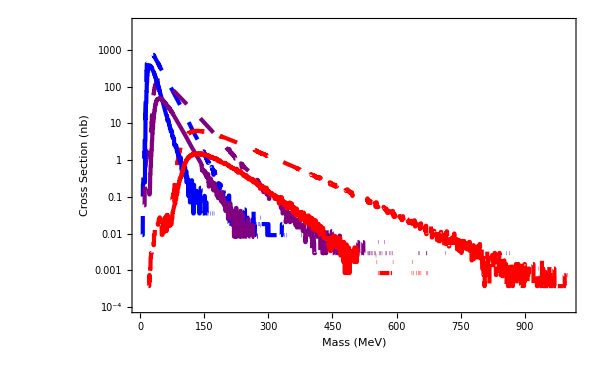

```mathematica
Show[MassDistBHXS[1.1,Full,1,1000]/.myThick->Sequence[Thickness[0.005],Dashing[Large],Blue],MassDistBHXS[2.2,Full,1,1000]/.myThick->Sequence[Thickness[0.005],Dashing[Large],Purple],(* MassDistBHXS[4.4,Full,1,1000]/.myThick->Sequence[Thickness[0.005],Dashing[Large],Darker[Green]], *)MassDistBHXS[6.6,Full,1,1000]/.myThick->Sequence[Thickness[0.005],Dashing[Large],Red],MassDistRadXS[1.1,Full,1,1000]/.myThick->Sequence[Thickness[0.005],Blue],MassDistRadXS[2.2,Full,1,1000]/.myThick->Sequence[Thickness[0.005],Purple],(* MassDistRadXS[4.4,Full,1,1000]/.myThick->Sequence[Thickness[0.005],Darker[Green]], *) MassDistRadXS[6.6,Full,1,1000]/.myThick->Sequence[Thickness[0.005],Red]]
```

### Reach functions for Bump Hunt

Fraction of events in a resolution-limited mass bin.  
(using BH, but rad distribution is quite similar so this is accurate almost everywhere – nonetheless, we could add it if worried about it.)

```mathematica
fbin[mode_,BSCon_,E0_,Run_,BkgMode_:BH][m_ (*GeV*),massOptimism_:1]:=NIntegrate[(TestDist[mode,E0,BkgMode,Run][x])/Normalization[mode,E0,BkgMode,Run],{x,m*1000-(deltaMFit[mode,m,BSCon, E0,Run, massOptimism]*1000)/2,m*1000+(deltaMFit[mode,m,BSCon, E0,Run, massOptimism]*1000)/2}];
```

Note: peakEff is the fraction of signal peak that ends up in a mass bin, which for 2.5 σ is about 80%. 
	Note the product below is (R/B) * (√B) * (S/R) i.e. S/√B, where R=radiative bkg, B=total bkg, and S=signal, IN A GIVEN BIN.

```mathematica
Significance[mode_?AtomQ,BSCon_,E0_,Run_,BkgMode_:BH][m_ (* in GeV!!! *), ϵ_,LumiBoost_:1,massOptimism_:1,peakEff_:0.8]:=RadFraction[mode,E0,Run,BkgMode]*
(LumiBoost*TotalStatistics[mode,E0,Run,BkgMode]*fbin[mode,BSCon,E0,Run,BkgMode][m,massOptimism])^(1/2)*
((3 π ϵ^2)/(2 α NeffFunction[mode,m GeV])*(m/deltaMFit[mode,m,BSCon, E0,Run, massOptimism])*peakEff);

NSigmaEpsilon[mode_,BSCon_,E0_,Run_,BkgMode_:BH][n_,m_,LumiBoost_:1,massOptimism_:1]:=√n 10^-3/ √(Significance[mode,BSCon,E0,Run,BkgMode][m,10^-3,LumiBoost,massOptimism]);
TwoSigmaEpsilon[mode_,BSCon_,E0_,Run_,BkgMode_:BH][m_,LumiBoost_:1,massOptimism_:1]:=NSigmaEpsilon[mode,BSCon,E0,Run,BkgMode][2,m,LumiBoost,massOptimism]
FiveSigmaEpsilon[mode_,BSCon_,E0_,Run_,BkgMode_:BH][m_,LumiBoost_:1,massOptimism_:1]:=NSigmaEpsilon[mode,BSCon,E0,Run,BkgMode][5,m,LumiBoost,massOptimism]
```

#### Combined Electron and Muon Resonance Search Significance

```mathematica
Significance[{ee,μμ},BSCon_,E0_,Run_][m_ (* in GeV!!! *),ϵ_,LumiBoost_:1,massOptimism_:1,peakEff_:0.8]:=((Significance[ee,BSCon,E0,Run][m,ϵ,LumiBoost,massOptimism,peakEff])^2+If[m<.21,0.0,(Significance[μμ,BSCon,E0,Run][m,ϵ,LumiBoost,massOptimism,peakEff])^2])^(1/2);
```

```mathematica
CombinedSignificance[BSCon_,BkgMode_,RunList_,BoostList_][m_ (* in GeV!!! *),ϵ_,massOptimism_:1,peakEff_:0.8]:=Module[{totSig=0},Do[(totSig+=(Significance[RunList[[i]][[1]],BSCon,RunList[[i]][[2]],Full,BkgMode][m,ϵ,BoostList[[i]],massOptimism,peakEff])^2),{i,Length[RunList]}];totSig^(1/2)];
```

```mathematica
TwoSigmaEpsilonCombined[BSCon_,BkgMode_,RunList_,BoostList_][m_,massOptimism_:1]:=√2 10^-3/ √(CombinedSignificance[BSCon,BkgMode,RunList,BoostList][m,10^-3,massOptimism]);
```

```mathematica
FourPtFiveSigmaEpsilonCombined[BSCon_,BkgMode_,RunList_,BoostList_][m_,massOptimism_:1]:=√4.5 10^-3/ √(CombinedSignificance[BSCon,BkgMode,RunList,BoostList][m,10^-3,massOptimism]);
```

```mathematica
(*  CombinedSignificance[mode_,BSCon_,Run_][m_ (* in GeV!!! *),ϵ_,LumiBoost_:1,massOptimism_:1,peakEff_:0.8]:=((Significance[ee,BSCon,1.1,Run][m,ϵ,LumiBoost,massOptimism,peakEff])^2+(Significance[ee,BSCon,2.2,Run][m,ϵ,LumiBoost,massOptimism,peakEff])^2+
(Significance[ee,BSCon,6.6,Run][m,ϵ,LumiBoost,massOptimism,peakEff])^2)^(1/2);  *)
```

```mathematica
NAprimeProduced[mode_?AtomQ,BSCon_,E0_,Run_,BkgMode_:BH][m_ (* in GeV!!! *), ϵ_,LumiBoost_:1,massOptimism_:1,peakEff_:0.8]:=RadFraction[mode,E0,Run,BkgMode]*(LumiBoost*TotalStatistics[mode,E0,Run,BkgMode]*fbin[mode,BSCon,E0,Run,BkgMode][m,massOptimism])*((3 π ϵ*ϵ)/(2 α NeffFunction[mode,m GeV])*(m/deltaMFit[mode,m,BSCon, E0,Run, massOptimism])*peakEff);
```

### Vertexing Rejection Values and Interpolation Functions

```mathematica
(*2.2 GeV  VERTEX PERFORMANCE With HPS detector  *) (* Numbers from HPS-Prime-SplitSensors with constrain chi^2 < 5 *)
VtxData[2.2,40,10]={{0.0,Log[10,0.5]},{2.0,Log[10,0.362697]},{3.0,Log[10,0.270757]},{4.0,Log[10,0.191652]},{5.0,Log[10,0.127753]},{6.0,Log[10,0.080193]},{7.0,Log[10,0.047083]},{8.0,Log[10,0.025914]},{9.0,Log[10,0.013217]},{10.0,Log[10,0.006245]},{11.0,Log[10,0.002784]},{12.0,Log[10,0.001219]},{13.0,Log[10,0.000516]},{14.0,Log[10,0.000236]},{15.0,Log[10,0.000112]},{17.5,Log[10,0.000020]}};
logFakeFraction[2.2,40,10]=Interpolation[VtxData[2.2,40,10],InterpolationOrder->1];
FakeFraction[2.2,40,10][x_]:=Power[10,logFakeFraction[2.2,40,10][x]];
VtxData[2.2,60,10]={{0.0,Log[10,0.5]},{2.0,Log[10,0.261310]},{3.0,Log[10,0.159982]},{4.0,Log[10,0.089022]},{5.0,Log[10,0.045331]},{6.0,Log[10,0.021388]},{7.0,Log[10,0.009513]},{8.0,Log[10,0.004091]},{9.0,Log[10,0.001750]},{10.0,Log[10,0.000755]},{11.0,Log[10,0.000332]},{12.0,Log[10,0.000153]},{13.0,Log[10,0.000073]},{14.0,Log[10,0.000037]},{15.0,Log[10,0.000019]},{17.5,Log[10,0.000004]}};
logFakeFraction[2.2,60,10]=Interpolation[VtxData[2.2,60,10],InterpolationOrder->1];
FakeFraction[2.2,60,10][x_]:=Power[10,logFakeFraction[2.2,60,10][x]];	
VtxData[2.2,80,10]={{0.0,Log[10,0.5]},{2.0,Log[10,0.195453]},{3.0,Log[10,0.097814]},{4.0,Log[10,0.043575]},{5.0,Log[10,0.017932]},{6.0,Log[10,0.007126]},{7.0,Log[10,0.002855]},{8.0,Log[10,0.001196]},{9.0,Log[10,0.000521]},{10.0,Log[10,0.000238]},{11.0,Log[10,0.000113]},{12.0,Log[10,0.000056]},{13.0,Log[10,0.000031]},{14.0,Log[10,0.000019]},{15.0,Log[10,0.000011]},{17.5,Log[10,0.000004]}};
logFakeFraction[2.2,80,10]=Interpolation[VtxData[2.2,80,10],InterpolationOrder->1];
FakeFraction[2.2,80,10][x_]:=Power[10,logFakeFraction[2.2,80,10][x]];
```

```mathematica
VtxData[4.4,80,10]={{0.0,Log[10,0.5]},{2.0,Log[10,0.2107792]},{3.0,Log[10,0.1073696]},{4.0,Log[10,0.0495355]},{5.0,Log[10,0.0206221]},{6.0,Log[10,0.0082084]},{7.0,Log[10,0.0030619]},{8.0,Log[10,0.0010892]},{9.0,Log[10,0.0003390]},{10.0,Log[10,0.0001154]},{11.0,Log[10,0.0000361]},{12.0,Log[10,0.0000108]}};
logFakeFraction[4.4,80,10]=Interpolation[VtxData[4.4,80,10],InterpolationOrder->1];
FakeFraction[4.4,80,10][x_]:=Power[10,logFakeFraction[4.4,80,10][x]];VtxData[4.4,120,10]={{0.0,Log[10,0.5]},{2.0,Log[10,0.1048160]},{3.0,Log[10,0.0327884]},{4.0,Log[10,0.0096827]},{5.0,Log[10,0.0029288]},{6.0,Log[10,0.0009227]},{7.0,Log[10,0.0002789]},{8.0,Log[10,0.0000876]},{9.0,Log[10,0.0000207]},{10.0,Log[10,0.0000069]},{11.0,Log[10,0.0000017]}};
logFakeFraction[4.4,120,10]=Interpolation[VtxData[4.4,120,10],InterpolationOrder->1];
FakeFraction[4.4,120,10][x_]:=Power[10,logFakeFraction[4.4,120,10][x]];
VtxData[4.4,160,10]={{0.0,Log[10,0.5]},{2.0,Log[10,0.0587916]},{3.0,Log[10,0.0138155]},{4.0,Log[10,0.0034521]},{5.0,Log[10,0.0009645]},{6.0,Log[10,0.0002713]},{7.0,Log[10,0.0000815]},{8.0,Log[10,0.0000232]},{9.0,Log[10,0.0000077]},{10.0,Log[10,0.0000023]},{11.0,Log[10,0.0000015]},{12.0,Log[10,0.0000003]}};
logFakeFraction[4.4,160,10]=Interpolation[VtxData[4.4,160,10],InterpolationOrder->1];
FakeFraction[4.4,160,10][x_]:=Power[10,logFakeFraction[4.4,160,10][x]];
```

```mathematica
(*6.6 GeV  VERTEX PERFORMANCE With HPS detector  *)
 (* Numbers from HPS-Prime-6GeV with constrain chi^2 < 5 *)
VtxData[6.6,100,10]={{0.0,Log[10,0.5]},{2.0,Log[10,0.150011]},{3.0,Log[10,0.059788]},{4.0,Log[10,0.021065]},{5.0,Log[10,0.007121]},{6.0,Log[10,0.002417]},{7.0,Log[10,0.000788]},{8.0,Log[10,0.000244]},{9.0,Log[10,0.000076]},{10.0,Log[10,0.000019]},{11.0,Log[10,0.000004]},{12.0,Log[10,0.000002]}};
logFakeFraction[6.6,100,10]=Interpolation[VtxData[6.6,100,10],InterpolationOrder->1];
FakeFraction[6.6,100,10][x_]:=Power[10,logFakeFraction[6.6,100,10][x]];
VtxData[6.6,150,10]={{0.0,Log[10,0.5]},{2.0,Log[10,0.069353]},{3.0,Log[10,0.017001]},{4.0,Log[10,0.004245]},{5.0,Log[10,0.001204]},{6.0,Log[10,0.000372]},{7.0,Log[10,0.000124]},{8.0,Log[10,0.000039]},{9.0,Log[10,0.000010]},{10.0,Log[10,0.000004]}};
logFakeFraction[6.6,150,10]=Interpolation[VtxData[6.6,150,10],InterpolationOrder->1];
FakeFraction[6.6,150,10][x_]:=Power[10,logFakeFraction[6.6,150,10][x]];
VtxData[6.6,200,10]={{0.0,Log[10,0.5]},{2.0,Log[10,0.034989]},{3.0,Log[10,0.006566]},{4.0,Log[10,0.001498]},{5.0,Log[10,0.000399]},{6.0,Log[10,0.000106]},{7.0,Log[10,0.000027]},{8.0,Log[10,0.000008]},{9.0,Log[10,0.000002]},{10.0,Log[10,0.000001]}};
logFakeFraction[6.6,200,10]=Interpolation[VtxData[6.6,200,10],InterpolationOrder->1];
FakeFraction[6.6,200,10][x_]:=Power[10,logFakeFraction[6.6,200,10][x]];
```

```mathematica
(*1.1 GeV  VERTEX PERFORMANCE With HPS detector  *) 
(* Numbers from HPS-Prime-1GeV with constrain chi^2 < 5 *)
VtxData[1.1,20,10]={{0.0,Log[10,0.5]},{2.0,Log[10,0.5028764]},{4.0,Log[10,0.3836150]},{6.0,Log[10,0.2710913]},{8.0,Log[10,0.1750463]},{10.0,Log[10,0.1014783]},{12.0,Log[10,0.0515525]},{14.0,Log[10,0.0227521]},{16.0,Log[10,0.0086820]},{18.0,Log[10,0.0028421]},{20.0,Log[10,0.0008868]},{22.0,Log[10,0.0003052]},{25.0,Log[10,0.0000789]},{30.0,Log[10,0.0000062]},{35.0,Log[10,0.0000007]}};
logFakeFraction[1.1,20,10]=Interpolation[VtxData[1.1,20,10],InterpolationOrder->1];
FakeFraction[1.1,20,10][x_]:=Power[10,logFakeFraction[1.1,20,10][x]];
VtxData[1.1,30,10]={{0.0,Log[10,0.5]},{2.0,Log[10,0.3941790]},{4.0,Log[10,0.2487679]},{6.0,Log[10,0.1354019]},{8.0,Log[10,0.0622149]},{10.0,Log[10,0.0241141]},{12.0,Log[10,0.0082035]},{14.0,Log[10,0.0026395]},{16.0,Log[10,0.0008545]},{18.0,Log[10,0.0002911]},{20.0,Log[10,0.0001168]},{22.0,Log[10,0.0000501]},{25.0,Log[10,0.0000164]},{30.0,Log[10,0.0000023]},{35.0,Log[10,0.0000004]},{40.0,Log[10,0.0000001]}};
logFakeFraction[1.1,30,10]=Interpolation[VtxData[1.1,30,10],InterpolationOrder->1];
FakeFraction[1.1,30,10][x_]:=Power[10,logFakeFraction[1.1,30,10][x]];
VtxData[1.1,40,10]={{0.0,Log[10,0.5]},{2.0,Log[10,0.3324942]},{4.0,Log[10,0.1716134]},{6.0,Log[10,0.0709187]},{8.0,Log[10,0.0238853]},{10.0,Log[10,0.0072200]},{12.0,Log[10,0.0022139]},{14.0,Log[10,0.0007136]},{16.0,Log[10,0.0002485]},{18.0,Log[10,0.0000934]},{20.0,Log[10,0.0000403]},{22.0,Log[10,0.0000186]},{25.0,Log[10,0.0000063]},{30.0,Log[10,0.0000014]},{35.0,Log[10,0.0000002]},{40.0,Log[10,0.00000005]}};
logFakeFraction[1.1,40,10]=Interpolation[VtxData[1.1,40,10],InterpolationOrder->1];
FakeFraction[1.1,40,10][x_]:=Power[10,logFakeFraction[1.1,40,10][x]];
```

```mathematica
VtxTable[E0_,m_,imax_:15]:=Table[{m,VtxData[E0,m,10][[i]][[1]],VtxData[E0,m,10][[i]][[2]]},{i,1,imax}];
FullTable1pt1=Join[VtxTable[1.1,20],VtxTable[1.1,30],VtxTable[1.1,40]];
FullTable2pt2=Join[VtxTable[2.2,40],VtxTable[2.2,60],VtxTable[2.2,80]];
FullTable6pt6=Join[VtxTable[6.6,100,12],VtxTable[6.6,150,10],VtxTable[6.6,200,10]];
```

```mathematica
ListPlot3D[FullTable1pt1]
```

-Graphics3D-

```mathematica
ListPlot3D[FullTable2pt2]
```

-Graphics3D-

```mathematica
ListPlot3D[FullTable6pt6]
```

-Graphics3D-

```mathematica
maxZ=40;
Needs["PlotLegends`"]
(* 2.2 GeV Fake Fractions *) 
step1FakeFractionGrid=Join[Table[{{0.06,x},Log[10,FakeFraction[2.2,60,10][x]]},{x,0,maxZ,1}],
Table[{{0.04,x},Log[10,FakeFraction[2.2,40,10][x]]},{x,0,maxZ,1}],
Table[{{0.08,x},Log[10,FakeFraction[2.2,80,10][x]]},{x,0,maxZ,1}]];
step1FakeFraction=Interpolation[step1FakeFractionGrid,InterpolationOrder->1];
step2FakeFractionGrid2pt2=Flatten[Table[{{x,y},step1FakeFraction[x,y]},{x,0.01,0.2,0.005},{y,0,maxZ,1}],1];
testFakeFraction2pt2=Interpolation[step2FakeFractionGrid2pt2,InterpolationOrder->1];
FakeFraction[2.2,10][m_(*in GeV*),z_(*in MM*)]:=Power[10,testFakeFraction2pt2[m,z]];
Plot3D[testFakeFraction2pt2[x,y],{x,0.01,0.10},{y,0,maxZ}]
```

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

InterpolatingFunction::dmval: Input value {18} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {19} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.01, 0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.01, 1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.01, 2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
(* 4.4 GeV Fake Fractions *) 
step1FakeFractionGrid4pt4=Join[Table[{{0.08,x},Log[10,FakeFraction[4.4,80,10][x]]},{x,0,maxZ,1}],
Table[{{0.12,x},Log[10,FakeFraction[4.4,120,10][x]]},{x,0,maxZ,1}],
Table[{{0.16,x},Log[10,FakeFraction[4.4,160,10][x]]},{x,0,maxZ,1}]];
step1FakeFraction4pt4=Interpolation[step1FakeFractionGrid4pt4,InterpolationOrder->1];
step2FakeFractionGrid4pt4=Flatten[Table[{{x,y},step1FakeFraction4pt4[x,y]},{x,0.01,0.4,0.005},{y,0,maxZ,1}],1];
testFakeFraction4pt4=Interpolation[step2FakeFractionGrid4pt4,InterpolationOrder->1];
FakeFraction[4.4,10][m_(*in GeV*),z_(*in MM*)]:=Power[10,testFakeFraction4pt4[m,z]];
Plot3D[testFakeFraction4pt4[x,y],{x,0.02,0.25},{y,0,maxZ}]
```

InterpolatingFunction::dmval: Input value {13} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {14} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {15} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.01, 0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.01, 1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.01, 2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
(* 6.6 GeV Fake Fractions *) 
step1FakeFractionGrid6pt6=Join[Table[{{0.15,x},Log[10,FakeFraction[6.6,150,10][x]]},{x,0,maxZ,1}],
Table[{{0.2,x},Log[10,FakeFraction[6.6,200,10][x]]},{x,0,maxZ,1}]];
step1FakeFraction6pt6=Interpolation[step1FakeFractionGrid6pt6,InterpolationOrder->1];
step2FakeFractionGrid6pt6=Flatten[Table[{{x,y},step1FakeFraction6pt6[x,y]},{x,0.01,0.5,0.01},{y,0,maxZ,1}],1];
testFakeFraction6pt6=Interpolation[step2FakeFractionGrid6pt6,InterpolationOrder->1];
FakeFraction[6.6,10][m_(*in GeV*),z_(*in MM*)]:=Power[10,testFakeFraction6pt6[m,z]];
Plot3D[testFakeFraction6pt6[x,y],{x,0.01,0.5},{y,0,maxZ}]
```

InterpolatingFunction::dmval: Input value {11} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {12} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {13} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.01, 0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.01, 1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.01, 2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
(* 1.1 GeV Fake Fractions *) step1FakeFractionGrid1pt1=Join[Table[{{0.02,x},Log[10,FakeFraction[1.1,20,10][x]]},{x,0,maxZ,1}],
 Table[{{0.03,x},Log[10,FakeFraction[1.1,30,10][x]]},{x,0,maxZ,1}],
Table[{{0.04,x},Log[10,FakeFraction[1.1,40,10][x]]},{x,0,maxZ,1}]];
step1FakeFraction1pt1=Interpolation[step1FakeFractionGrid1pt1,InterpolationOrder->1];
step2FakeFractionGrid1pt1=Flatten[Table[{{x,y},step1FakeFraction1pt1[x,y]},{x,0.005,0.05,0.002},{y,0,maxZ,1}],1];
testFakeFraction1pt1=Interpolation[step2FakeFractionGrid1pt1,InterpolationOrder->1];
FakeFraction[1.1,10][m_(*in GeV*),z_(*in MM*)]:=Power[10,testFakeFraction1pt1[m,z]];
Show[Plot3D[testFakeFraction1pt1[x,y],{x,0.01,0.05},{y,0,maxZ}]]
```

InterpolatingFunction::dmval: Input value {36} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {37} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {38} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.005, 0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.005, 1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.005, 2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
-Graphics3D-.10
```

.10 -Graphics3D-

```mathematica
FakeFractionCalc[s_,z_]:=1-CDF[NormalDistribution[0,s],z];
vtxDataPlot[E0_,m_]:=ListPlot[VtxData[E0,m,10],Joined->True,PlotStyle->{Blue,myThick},PlotMarkers->{Automatic,Medium},PlotRange->{{0,40},{0,-7}},Frame->True, FrameLabel->{"Z_cut (mm)","log(rejection)"},BaseStyle->{FontWeight->"Bold",FontSize->18}]
```

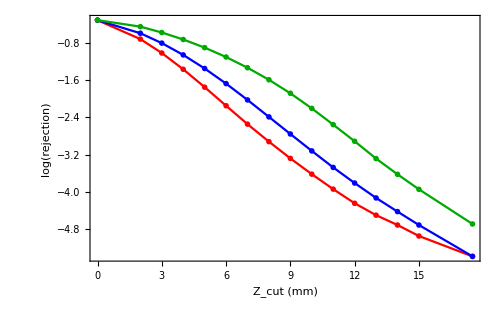

```mathematica
Show[vtxDataPlot[2.2,80] /.myThick->Sequence[Red],vtxDataPlot[2.2,60]/.myThick->Sequence[Blue],vtxDataPlot[2.2,40]/.myThick->Sequence[Darker[Green]],ImageSize->500]
```

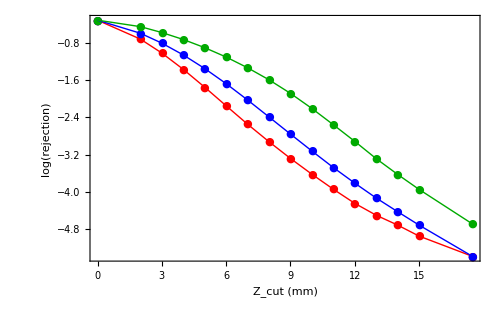

-Graphics-

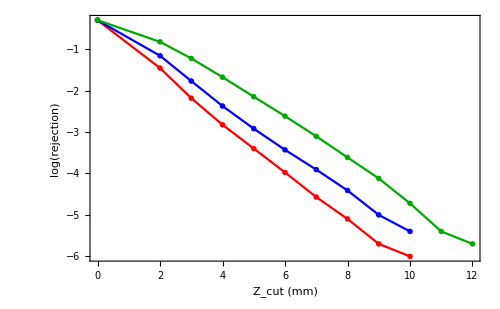

```mathematica
Show[vtxDataPlot[6.6,200] /.myThick->Sequence[Red],vtxDataPlot[6.6,150]/.myThick->Sequence[Blue],vtxDataPlot[6.6,100]/.myThick->Sequence[Darker[Green]],ImageSize->500]
```

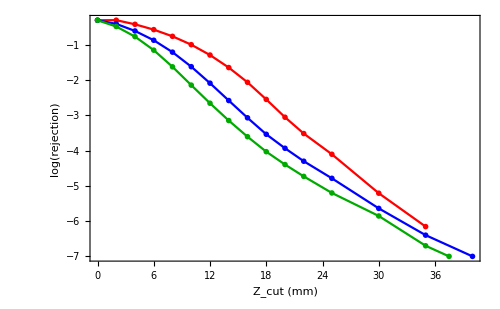

```mathematica
Show[vtxDataPlot[1.1,20] /.myThick->Sequence[Red],vtxDataPlot[1.1,30]/.myThick->Sequence[Blue],vtxDataPlot[1.1,40]/.myThick->Sequence[Darker[Green]],ImageSize->500]
```

InterpolatingFunction::dmval: Input value {17.5354} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {17.9601} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {18.3567} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

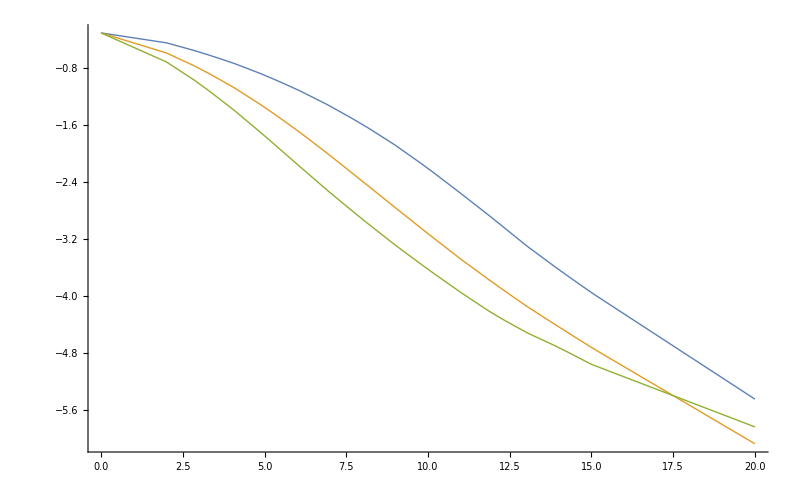

```mathematica
int2pt2=Plot[{Log[10,FakeFraction[2.2,40,10][x]],Log[10,FakeFraction[2.2,60,10][x]],Log[10,FakeFraction[2.2,80,10][x]]},{x,0,20},PlotRange->{{1,20},{0,-10}},PlotStyle->{Thick,Thick,Thick,},PlotLegend->{"40MeV","60MeV", "80MeV" },LegendPosition->{0.9,-0.2},LegendSize->{0.6,0.6},LegendShadow->None,ImageSize->800];
Show[int2pt2]
```

InterpolatingFunction::dmval: Input value {12.2434} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {12.6674} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {13.0632} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

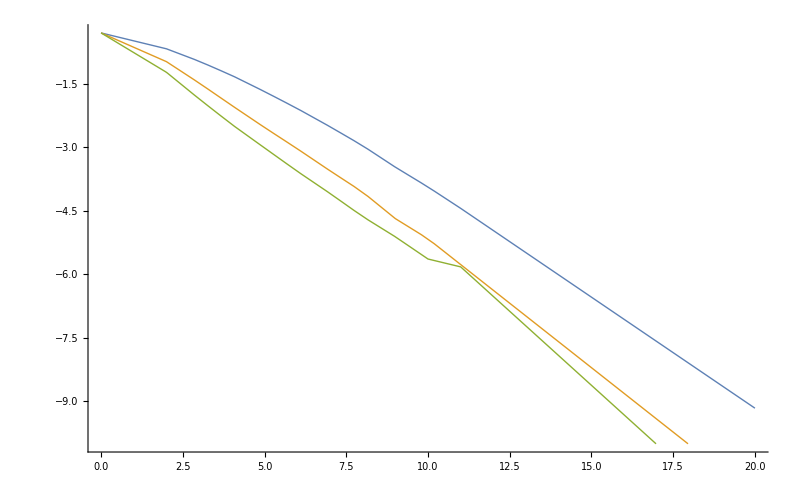

```mathematica
Plot[{Log[10,FakeFraction[4.4,80,10][x]],Log[10,FakeFraction[4.4,120,10][x]],Log[10,FakeFraction[4.4,160,10][x]]},{x,0,20},PlotRange->{{1,20},{0,-10}},PlotStyle->{Thick,Thick,Thick,},PlotLegend->{"80MeV","120MeV", "160MeV" },LegendPosition->{0.9,-0.2},LegendSize->{0.6,0.6},LegendShadow->None,ImageSize->800]
```

InterpolatingFunction::dmval: Input value {12.2434} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {12.6674} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {13.0632} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

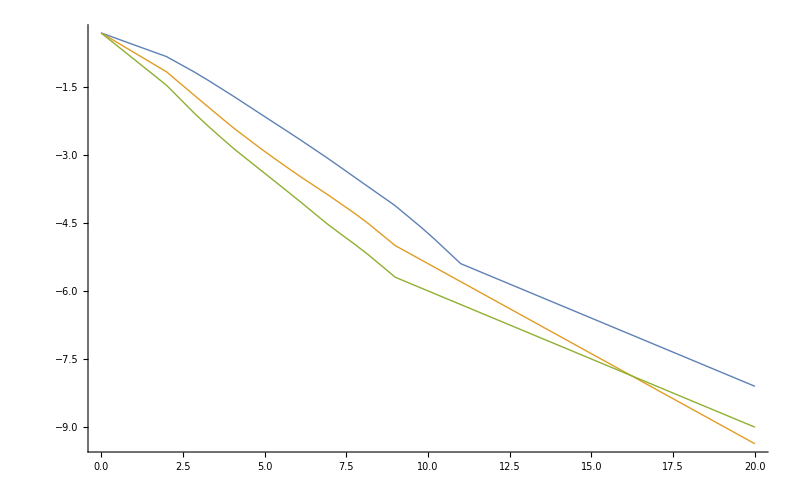

InterpolatingFunction::dmval: Input value {35.0708} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {35.9203} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {36.7133} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

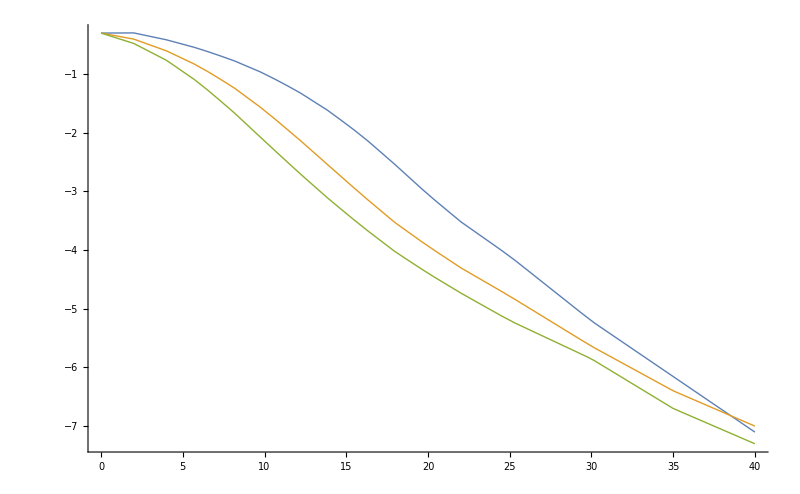

```mathematica
Plot[{Log[10,FakeFraction[6.6,100,10][x]],Log[10,FakeFraction[6.6,150,10][x]],Log[10,FakeFraction[6.6,200,10][x]]},{x,0,20},PlotRange->{{1,20},{0,-10}},PlotStyle->{Thick,Thick,Thick},PlotLegend->{"100MeV","150MeV", "200MeV" },LegendPosition->{0.9,-0.2},LegendSize->{0.6,0.6},LegendShadow->None,ImageSize->800]

Plot[{Log[10,FakeFraction[1.1,20,10][x]],Log[10,FakeFraction[1.1,30,10][x]],Log[10,FakeFraction[1.1,40,10][x]]},{x,0,40},PlotRange->{{1,40},{0,-10}},PlotStyle->{Thick,Thick,Thick},PlotLegend->{"20MeV","30MeV", "40MeV" },LegendPosition->{0.9,-0.2},LegendSize->{0.6,0.6},LegendShadow->None,ImageSize->800]
```

```mathematica
Plot3D[testFakeFraction4pt4[x,y],{x,0.176,0.18},{y,0,maxZ}]
```

-Graphics3D-

-Graphics3D-

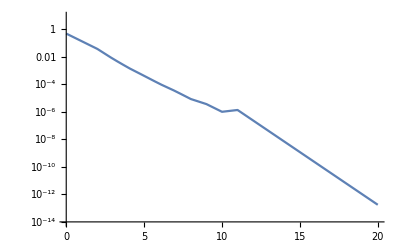

```mathematica
LogPlot[FakeFraction[4.4,10][0.19(*in GeV*),y(*in MM*)],{y,0,20}]
```

### Plots: Initialize constraints reference plots

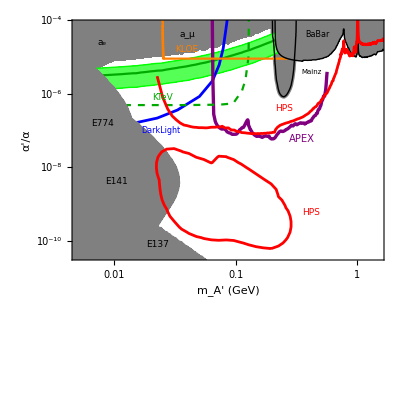
```mathematica
comboAll=-Graphics-
```

General::noinfo: Input expression InterpolatingFunction[] contains insufficient information to interpret the result.

-Graphics-

-Graphics-

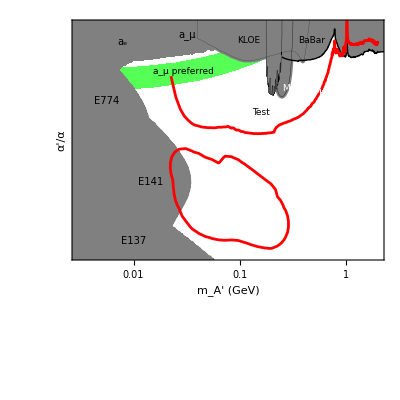
```mathematica
NoFuture=-Graphics-
```

General::noinfo: Input expression InterpolatingFunction[] contains insufficient information to interpret the result.

-Graphics-

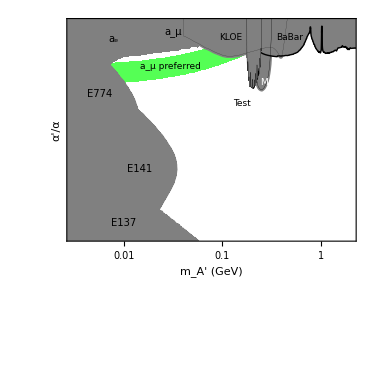
```mathematica
current=-Graphics-;
```

```mathematica
mylegendplot2=LogLogPlot[1,{m,0.001,2.1},Frame->True,PlotRange->{{0.001,2},{10^-5.5,1.00001 10^-2}},FrameTicks->{fticksR[0.001,2,5],(*fticks2[10^-11,10^-1,1]*)fticksR2[10^-11,10^-2,0]},FrameLabel->{"m_A' (GeV)","α'/α"},LabelStyle->16,
Epilog->{
(*Inset[Style["Orsay",FontSize->12,Black],Scaled[{0.3,0.59}]],*)
}]
```

-Graphics-

### Bump-Hunt Functions & Plots

```mathematica
(* bumphuntPlot[{args__},PlotOptions___,LumiBoost_:1]:=ListPlot[Table[Log[10,{m,TwoSigmaEpsilon[args][m,LumiBoost]}],{m,0.01,1.0,0.005}],Joined->True,PlotRange->{{-2.5,0.},{-5,-2}},PlotOptions]
bumphuntCombinedPlot[{args__},PlotOptions___,LumiBoost_:1]:=ListPlot[Table[Log[10,{m,TwoSigmaEpsilonCombined[args][m,LumiBoost]}],{m,0.01,1.0,0.005}],Joined->True,PlotRange->{{-2.5,0.},{-5,-2}},PlotOptions]
bumphuntPlot5Sigma[{args__},PlotOptions___,LumiBoost_:1]:=ListPlot[Table[Log[10,{m,FiveSigmaEpsilon[args][m,LumiBoost]}],{m,0.01,1.0,0.005}],Joined->True,PlotRange->{{-2.5,0.},{-5,-2}},PlotOptions] *)
bumphuntTable[{args__},LumiBoost_:1]:=Table[{m,TwoSigmaEpsilon[args][m,LumiBoost]},{m,0.01,1.0,0.005}];
bumphuntPlot[{args__},PlotOptions___,LumiBoost_:1]:=ListLogLogPlot[Table[{m,TwoSigmaEpsilon[args][m,LumiBoost]},{m,0.01,1.0,0.005}],Joined->True,PlotRange->{{10^-2.5,10^0},{10^-5,10^-2}},PlotOptions]
bumphuntCombinedPlot[{args__},PlotOptions___]:=ListLogLogPlot[Table[{m,TwoSigmaEpsilonCombined[args][m]},{m,0.01,1.0,0.005}],Joined->True,PlotRange->{{10^-2.5,10^0},{10^-5,10^-2}},PlotOptions]
bumphuntPlot5Sigma[{args__},PlotOptions___,LumiBoost_:1]:=ListLogLogPlot[Table[{m,FiveSigmaEpsilon[args][m,LumiBoost]},{m,0.01,1.0,0.005}],Joined->True,PlotRange->{{10^-2.5,10^0},{10^-5,10^-2}},PlotOptions]
bumphuntCombinedPlotEvidence[{args__},PlotOptions___]:=ListLogLogPlot[Table[{m,FourPtFiveSigmaEpsilonCombined[args][m]},{m,0.01,1.0,0.005}],Joined->True,PlotRange->{{10^-2.5,10^0},{10^-5,10^-2}},PlotOptions]
```

#### Electron Only Plots

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

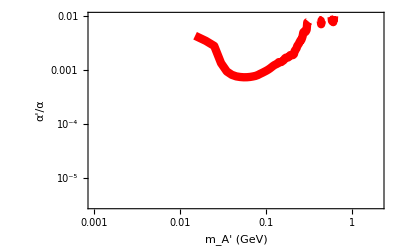

```mathematica
Boost=1;massImprove=1;
(* ee2pt2GeVBumpHunt=Show[bumphuntPlot[{ee,BS,2.2,Full},PlotStyle->{Red,myThick},Boost],PlotRange->{{-2.5,0.},{-5,-2}}] *)
ee2pt2GeVBumpHunt=bumphuntPlot[{ee,BS,2.2,Full,FullTri},PlotStyle->{Red,myThick},Boost];
Show[mylegendplot2,ee2pt2GeVBumpHunt]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

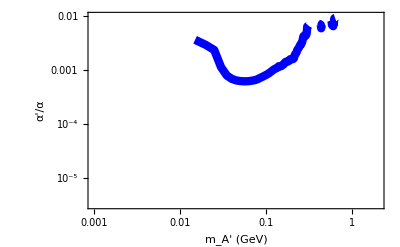

```mathematica
Boost=2;massImprove=1;
(* ee2pt2GeVBumpHunt=Show[bumphuntPlot[{ee,BS,2.2,Full},PlotStyle->{Red,myThick},Boost],PlotRange->{{-2.5,0.},{-5,-2}}] *)
ee2pt2GeVBumpHunt2WeeksFullTri=bumphuntPlot[{ee,BS,2.2,Full,FullTri},PlotStyle->{Blue,myThick},Boost];
Show[mylegendplot2,ee2pt2GeVBumpHunt2WeeksFullTri]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

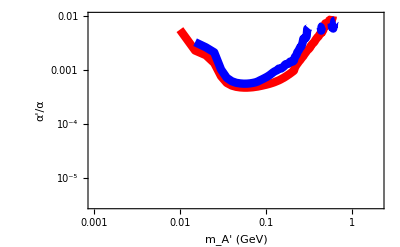

```mathematica
Boost=3;massImprove=1;
(* ee2pt2GeVBumpHunt=Show[bumphuntPlot[{ee,BS,2.2,Full},PlotStyle->{Red,myThick},Boost],PlotRange->{{-2.5,0.},{-5,-2}}] *)
ee2pt2GeVBumpHunt3Weeks=bumphuntPlot[{ee,BS,2.2,Full,BH},PlotStyle->{Red,myThick},Boost];
ee2pt2GeVBumpHunt3WeeksFullTri=bumphuntPlot[{ee,BS,2.2,Full,FullTri},PlotStyle->{Blue,myThick},Boost];
Show[mylegendplot2,ee2pt2GeVBumpHunt3Weeks,ee2pt2GeVBumpHunt3WeeksFullTri]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

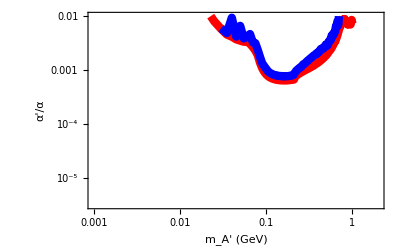

```mathematica
Boost=1;massImprove=1;
(*ee6pt6GeVBumpHunt=Show[bumphuntPlot[{ee,BS,6.6,Full},PlotStyle->{Red,myThick},Boost],PlotRange->{{10^-2.5,10^0},{10^-5,10^-2}}] *)
ee6pt6GeVBumpHunt=bumphuntPlot[{ee,BS,6.6,Full},PlotStyle->{Red,myThick},Boost];
ee6pt6GeVBumpHuntFullTri=bumphuntPlot[{ee,BS,6.6,Full,FullTri},PlotStyle->{Blue,myThick},Boost];
Show[mylegendplot2,ee6pt6GeVBumpHunt,ee6pt6GeVBumpHuntFullTri]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

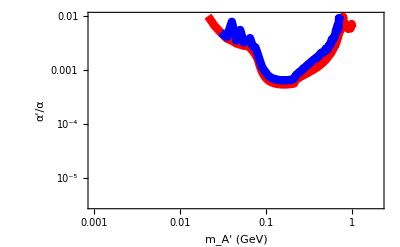

```mathematica
Boost=2;massImprove=1;
(*ee6pt6GeVBumpHunt=Show[bumphuntPlot[{ee,BS,6.6,Full},PlotStyle->{Red,myThick},Boost],PlotRange->{{10^-2.5,10^0},{10^-5,10^-2}}] *)
ee6pt6GeVBumpHunt2Weeks=bumphuntPlot[{ee,BS,6.6,Full},PlotStyle->{Red,myThick},Boost];
ee6pt6GeVBumpHunt2WeeksFullTri=bumphuntPlot[{ee,BS,6.6,Full,FullTri},PlotStyle->{Blue,myThick},Boost];
Show[mylegendplot2,ee6pt6GeVBumpHunt2Weeks,ee6pt6GeVBumpHunt2WeeksFullTri]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

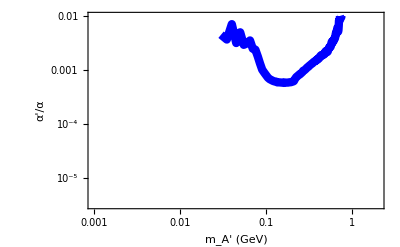

```mathematica
Boost=3;massImprove=1;
(*ee6pt6GeVBumpHunt=Show[bumphuntPlot[{ee,BS,6.6,Full},PlotStyle->{Red,myThick},Boost],PlotRange->{{10^-2.5,10^0},{10^-5,10^-2}}] *)
ee6pt6GeVBumpHunt3WeeksFullTri=bumphuntPlot[{ee,BS,6.6,Full,FullTri},PlotStyle->{Blue,myThick},Boost];
Show[mylegendplot2,ee6pt6GeVBumpHunt3WeeksFullTri]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

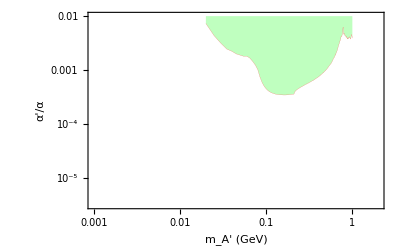

```mathematica
Boost=4*3;massImprove=1;
(*ee6pt6GeVBumpHunt=Show[bumphuntPlot[{ee,BS,6.6,Full},PlotStyle->{Red,myThick},Boost],PlotRange->{{10^-2.5,10^0},{10^-5,10^-2}}] *)
ee6pt6GeVBumpHuntBeam3Months=bumphuntPlot[{ee,BS,6.6,Full},{PlotStyle->{Red,Thickness[0.0001]},Filling->{1->Top},FillingStyle->Directive[Green,Opacity[0.25]]},Boost];
Show[mylegendplot2,ee6pt6GeVBumpHuntBeam3Months]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

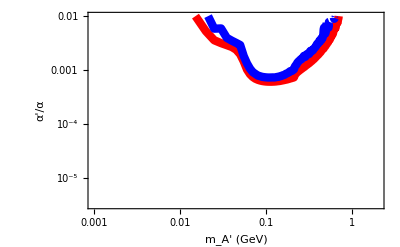

```mathematica
Boost=1;massImprove=1;
ee4pt4GeVBumpHunt1Week=bumphuntPlot[{ee,BS,4.4,Full},PlotStyle->{Red,myThick},Boost];
ee4pt4GeVBumpHunt1WeekFullTri=bumphuntPlot[{ee,BS,4.4,Full,FullTri},PlotStyle->{Blue,myThick},Boost];
Show[mylegendplot2,ee4pt4GeVBumpHunt1Week,ee4pt4GeVBumpHunt1WeekFullTri]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

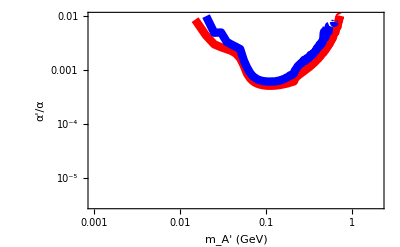

```mathematica
Boost=2;massImprove=1;
(* ee1pt1GeVBumpHunt=Show[bumphuntPlot[{ee,BS,1.1,Full},PlotStyle->{Red,myThick},Boost],PlotRange->{{-2.5,0.},{-5,-2}}] *)
(*Export[EXPDIR<>"ee5pt5GeVBumpHunt.pdf",ee5pt5GeVBumpHunt];*)
ee4pt4GeVBumpHunt2Weeks=bumphuntPlot[{ee,BS,4.4,Full},PlotStyle->{Red,myThick},Boost];
ee4pt4GeVBumpHunt2WeeksFullTri=bumphuntPlot[{ee,BS,4.4,Full,FullTri},PlotStyle->{Blue,myThick},Boost];
Show[mylegendplot2,ee4pt4GeVBumpHunt2Weeks,ee4pt4GeVBumpHunt2WeeksFullTri]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

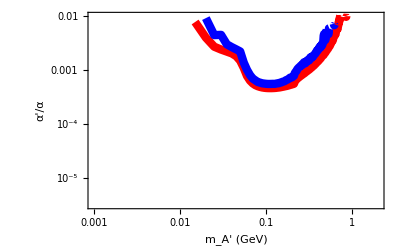

```mathematica
Boost=3;massImprove=1;
(* ee1pt1GeVBumpHunt=Show[bumphuntPlot[{ee,BS,1.1,Full},PlotStyle->{Red,myThick},Boost],PlotRange->{{-2.5,0.},{-5,-2}}] *)
(*Export[EXPDIR<>"ee5pt5GeVBumpHunt.pdf",ee5pt5GeVBumpHunt];*)
ee4pt4GeVBumpHunt3Weeks=bumphuntPlot[{ee,BS,4.4,Full},PlotStyle->{Red,myThick},Boost];
ee4pt4GeVBumpHunt3WeeksFullTri=bumphuntPlot[{ee,BS,4.4,Full,FullTri},PlotStyle->{Blue,myThick},Boost];
Show[mylegendplot2,ee4pt4GeVBumpHunt3Weeks,ee4pt4GeVBumpHunt3WeeksFullTri]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

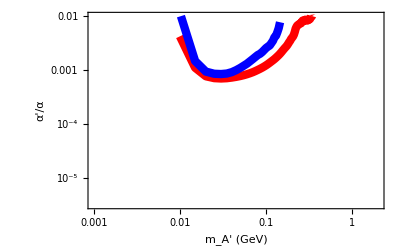

```mathematica
Boost=1;massImprove=1;
(* ee1pt1GeVBumpHunt=Show[bumphuntPlot[{ee,BS,1.1,Full},PlotStyle->{Red,myThick},Boost],PlotRange->{{-2.5,0.},{-5,-2}}] *)
(*Export[EXPDIR<>"ee5pt5GeVBumpHunt.pdf",ee5pt5GeVBumpHunt];*)
ee1pt1GeVBumpHunt=bumphuntPlot[{ee,BS,1.1,Full},PlotStyle->{Red,myThick},Boost];
ee1pt1GeVBumpHuntFullTri=bumphuntPlot[{ee,BS,1.1,Full,FullTri},PlotStyle->{Blue,myThick},Boost];
Show[mylegendplot2,ee1pt1GeVBumpHunt,ee1pt1GeVBumpHuntFullTri]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

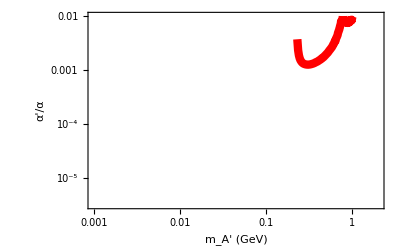

```mathematica
Boost=1;massImprove=1;
(* ee1pt1GeVBumpHunt=Show[bumphuntPlot[{ee,BS,1.1,Full},PlotStyle->{Red,myThick},Boost],PlotRange->{{-2.5,0.},{-5,-2}}] *)
(*Export[EXPDIR<>"ee5pt5GeVBumpHunt.pdf",ee5pt5GeVBumpHunt];*)
ee6pt6GeVMuonBumpHunt=bumphuntPlot[{μμ,BS,6.6,Full},PlotStyle->{Red,myThick},Boost];
Show[mylegendplot2,ee6pt6GeVMuonBumpHunt]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

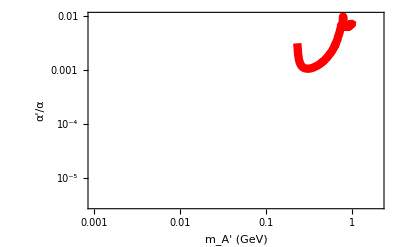

```mathematica
Boost=2;massImprove=1;
(* ee1pt1GeVBumpHunt=Show[bumphuntPlot[{ee,BS,1.1,Full},PlotStyle->{Red,myThick},Boost],PlotRange->{{-2.5,0.},{-5,-2}}] *)
(*Export[EXPDIR<>"ee5pt5GeVBumpHunt.pdf",ee5pt5GeVBumpHunt];*)
ee6pt6GeVMuonBumpHunt1Month=bumphuntPlot[{μμ,BS,6.6,Full},PlotStyle->{Red,myThick},Boost];
Show[mylegendplot2,ee6pt6GeVMuonBumpHunt1Month]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

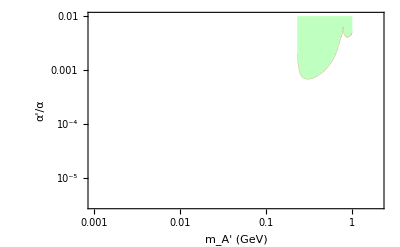

```mathematica
Boost=4*3;massImprove=1;
(* ee1pt1GeVBumpHunt=Show[bumphuntPlot[{ee,BS,1.1,Full},PlotStyle->{Red,myThick},Boost],PlotRange->{{-2.5,0.},{-5,-2}}] *)
(*Export[EXPDIR<>"ee5pt5GeVBumpHunt.pdf",ee5pt5GeVBumpHunt];*)
ee6pt6GeVMuonBumpHuntBeam3Months=bumphuntPlot[{μμ,BS,6.6,Full},{PlotStyle->{Red,Thickness[0.0001]},Filling->{1->Top},FillingStyle->Directive[Green,Opacity[0.25]]},Boost];
Show[mylegendplot2,ee6pt6GeVMuonBumpHuntBeam3Months]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

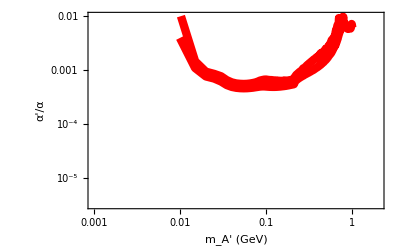

```mathematica
RunList={{ee,1.1},{ee,2.2},{ee,6.6}};
BoostList={1,3,2};
(* eeCombinedBumpHunt=Show[bumphuntCombinedPlot[{ee,BS,Full},PlotStyle->{Red,myThick},Boost],PlotRange->{{-2.5,0.},{-5,-2}}] *)
eemumuCombinedBumpHuntProposalNoMuons=bumphuntCombinedPlot[{BS,BH,RunList,BoostList},PlotStyle->{Red,myThick},Filling->True];
eemumuCombinedBumpHuntProposalNoMuonsFullTri=bumphuntCombinedPlot[{BS,FullTri,RunList,BoostList},PlotStyle->{Red,myThick},Filling->True];
Show[mylegendplot2,eemumuCombinedBumpHuntProposalNoMuons,eemumuCombinedBumpHuntProposalNoMuonsFullTri]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

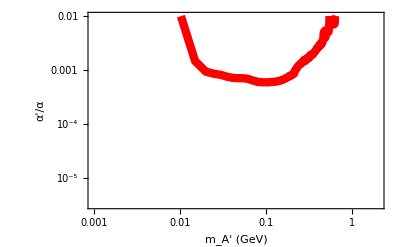

```mathematica
RunList={{ee,1.1},{ee,2.2},{ee,4.4}};
BoostList={1,1,2};
(* eeCombinedBumpHunt=Show[bumphuntCombinedPlot[{ee,BS,Full},PlotStyle->{Red,myThick},Boost],PlotRange->{{-2.5,0.},{-5,-2}}] *)
eemumuCombinedBumpHunt2015=bumphuntCombinedPlot[{BS,FullTri,RunList,BoostList},PlotStyle->{Red,myThick},Filling->True];
Show[mylegendplot2,eemumuCombinedBumpHunt2015]
```

```mathematica
Table[{m,TwoSigmaEpsilonCombined[BS,FullTri,RunList,BoostList][m]},{m,0.013,0.6,0.01}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

{{0.013,0.0024898},{0.023,0.000871871},{0.033,0.000778889},{0.043,0.000711677},{0.053,0.00070968},{0.063,0.000678375},{0.073,0.000626532},{0.083,0.000602848},{0.093,0.000594223},{0.103,0.000593306},{0.113,0.000597756},{0.123,0.00060219},{0.133,0.000617356},{0.143,0.000632269},{0.153,0.000655156},{0.163,0.000680991},{0.173,0.000726731},{0.183,0.000753159},{0.193,0.000796551},{0.203,0.000824193},{0.213,0.000927702},{0.223,0.00103502},{0.233,0.00116788},{0.243,0.00123347},{0.253,0.00133091},{0.263,0.00139059},{0.273,0.00150885},{0.283,0.00148175},{0.293,0.00158275},{0.303,0.00168204},{0.313,0.00167306},{0.323,0.00182501},{0.333,0.00190698},{0.343,0.00196669},{0.353,0.00200264},{0.363,0.00218507},{0.373,0.00220422},{0.383,0.00238159},{0.393,0.00260567},{0.403,0.00265108},{0.413,0.00296838},{0.423,0.00286638},{0.433,0.00299586},{0.443,0.00317612},{0.453,0.0033065},{0.463,0.00424099},{0.473,0.00535242},{0.483,0.00397041},{0.493,0.00418574},{0.503,0.00530904},{0.513,ComplexInfinity},{0.523,0.00539007},{0.533,0.005714},{0.543,0.00687232},{0.553,0.0124248},{0.563,0.0125831},{0.573,0.00926074},{0.583,0.00792821},{0.593,0.00842114}}

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

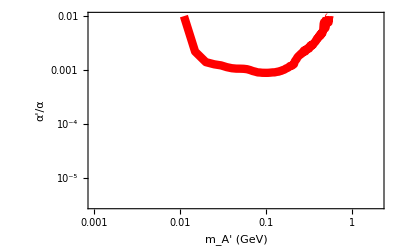

```mathematica
RunList={{ee,1.1},{ee,2.2},{ee,4.4}};
BoostList={1,1,2};
(* eeCombinedBumpHunt=Show[bumphuntCombinedPlot[{ee,BS,Full},PlotStyle->{Red,myThick},Boost],PlotRange->{{-2.5,0.},{-5,-2}}] *)
eemumuCombinedBumpHunt2015Evidence=bumphuntCombinedPlotEvidence[{BS,FullTri,RunList,BoostList},PlotStyle->{Red,myThick},Filling->True];
Show[mylegendplot2,eemumuCombinedBumpHunt2015Evidence]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

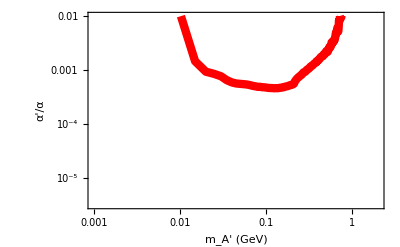

```mathematica
RunList={{ee,1.1},{ee,2.2},{ee,4.4},{ee,6.6}};
BoostList={1,3,4,3};
(* eeCombinedBumpHunt=Show[bumphuntCombinedPlot[{ee,BS,Full},PlotStyle->{Red,myThick},Boost],PlotRange->{{-2.5,0.},{-5,-2}}] *)
eemumuCombinedBumpHunt2017=bumphuntCombinedPlot[{BS,FullTri,RunList,BoostList},PlotStyle->{Red,myThick},Filling->True];
Show[mylegendplot2,eemumuCombinedBumpHunt2017]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

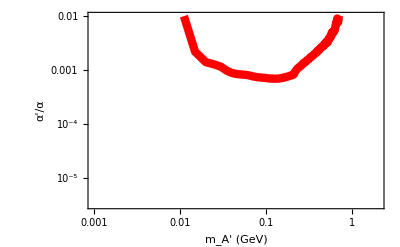

```mathematica
RunList={{ee,1.1},{ee,2.2},{ee,4.4},{ee,6.6}};
BoostList={1,3,4,3};
(* eeCombinedBumpHunt=Show[bumphuntCombinedPlot[{ee,BS,Full},PlotStyle->{Red,myThick},Boost],PlotRange->{{-2.5,0.},{-5,-2}}] *)
eemumuCombinedBumpHunt2017Evidence=bumphuntCombinedPlotEvidence[{BS,FullTri,RunList,BoostList},PlotStyle->{Red,myThick},Filling->True];
Show[mylegendplot2,eemumuCombinedBumpHunt2017Evidence]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

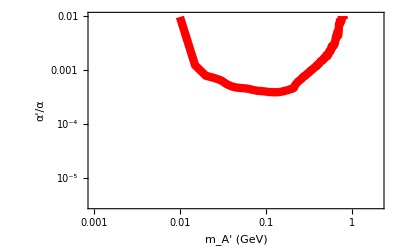

```mathematica
RunList={{ee,1.1},{ee,2.2},{ee,4.4},{ee,6.6}};
BoostList={2,6,8,6};
(* eeCombinedBumpHunt=Show[bumphuntCombinedPlot[{ee,BS,Full},PlotStyle->{Red,myThick},Boost],PlotRange->{{-2.5,0.},{-5,-2}}] *)
eemumuCombinedBumpHunt2027=bumphuntCombinedPlot[{BS,FullTri,RunList,BoostList},PlotStyle->{Red,myThick},Filling->True];
Show[mylegendplot2,eemumuCombinedBumpHunt2027]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

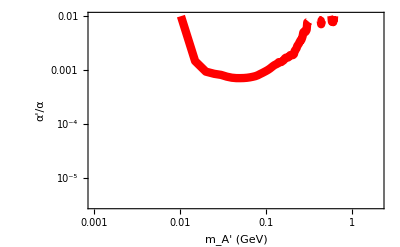

```mathematica
RunList={{ee,1.1},{ee,2.2}};
BoostList={1,1};
(* eeCombinedBumpHunt=Show[bumphuntCombinedPlot[{ee,BS,Full},PlotStyle->{Red,myThick},Boost],PlotRange->{{-2.5,0.},{-5,-2}}] *)
eeCombinedBumpHunt1gev2gev2015=bumphuntCombinedPlot[{BS,FullTri,RunList,BoostList},PlotStyle->{Red,myThick},Filling->True];
Show[mylegendplot2,eeCombinedBumpHunt1gev2gev2015]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

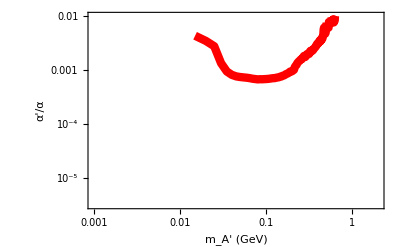

```mathematica
RunList={{ee,4.4},{ee,2.2}};
BoostList={1,1};
(* eeCombinedBumpHunt=Show[bumphuntCombinedPlot[{ee,BS,Full},PlotStyle->{Red,myThick},Boost],PlotRange->{{-2.5,0.},{-5,-2}}] *)
eeCombinedBumpHuntwith4pt42015=bumphuntCombinedPlot[{BS,FullTri,RunList,BoostList},PlotStyle->{Red,myThick},Filling->True];
Show[mylegendplot2,eeCombinedBumpHuntwith4pt42015]
```

### Vertex Reach Functions

Assuming reconstruction works out to 20 cm, and neglecting smearing of signal (probably fair since we're at >>> 1σ):

```mathematica
maxDecay=200MM;
vtxeffsig[m_,ϵ_,zcut_,vtxQualityEff_:0.7,En_:5.5]:=If[zcut/MM<200,vtxQualityEff*(E^(-zcut/γcτ[m,ϵ,En])-E^(-(maxDecay)/γcτ[m,ϵ,En])),0];
vtxeffbkg[fakeFunction_,m_(*in GeV*),zcut_,vtxQualityEff_:0.7]:=vtxQualityEff*fakeFunction[m,zcut/MM];
```

```mathematica
vtxBkgCount[mode_,E0_,Run_,BkgMode_:BH][fakeFunction_,m_,zcut_,LumiBoost_:1,massOptimism_:1,vtxQualityEff_:0.7]:=vtxeffbkg[fakeFunction,m,zcut,vtxQualityEff]*LumiBoost*TotalStatistics[mode,E0,Run,BkgMode]*fbin[mode,NoBS,E0,Run,BkgMode][m,massOptimism];

vtxSigCount[mode_,E0_,Run_,BkgMode_:BH][fakeFunction_,m_,ϵ_,zcut_,LumiBoost_:1,massOptimism_:1,vtxQualityEff_:0.7,peakEff_:0.8]:=vtxeffsig[m,ϵ,zcut,vtxQualityEff,E0]*RadFraction[mode,E0,Run,BkgMode]*
(LumiBoost*TotalStatistics[mode,E0,Run,BkgMode]*fbin[mode,NoBS,E0,Run,BkgMode][m,massOptimism])*
((3 π ϵ^2)/(2 α NeffFunction[mode,m GeV])*(m/deltaMFit[mode,m,NoBS, E0, Run,massOptimism])*peakEff);
```

```mathematica
VtxSignificance[mode_,E0_,Run_,BkgMode_:BH][fakeFunction_,m_,ϵ_,zcut_,LumiBoost_:1,massOptimism_:1,vtxQualityEff_:0.7,peakEff_:0.8]:=Module[{sigFrac,bkgFrac,bkgCount},
sigFrac=vtxeffsig[m,ϵ,zcut,vtxQualityEff,E0];
bkgFrac=vtxeffbkg[fakeFunction,m,zcut,vtxQualityEff];
bkgCount=vtxBkgCount[mode,E0,Run,BkgMode][fakeFunction,m,zcut,LumiBoost,massOptimism,vtxQualityEff];

(* DEBUGGING // Print["bkgCount=",bkgCount,"  sigCount=",vtxSigCount[mode,E0][fakeFunction,m,ϵ,zcut,LumiBoost,massOptimism,vtxQualityEff,peakEff],
If[sigFrac/(√bkgFrac)*Significance[mode,E0][m,ϵ,LumiBoost,massOptimism,peakEff]>
1/1.5 vtxSigCount[mode,E0][fakeFunction,m,ϵ,zcut,LumiBoost,massOptimism,vtxQualityEff,peakEff],"count","signif"]];


Print["two significances: ",
sigFrac/(√bkgFrac)*Significance[mode,E0][m,ϵ,LumiBoost,massOptimism,peakEff], "    ",
(vtxSigCount[mode,E0][fakeFunction,m,ϵ,zcut,LumiBoost,massOptimism,vtxQualityEff,peakEff])/(√bkgCount)

]; //END DEBUGGING *)
(* This is ad hoc, want at least 2.4 signal events expected in order to exclude. *)

Min[
sigFrac/(√bkgFrac)*Significance[mode,NoBS,E0,Run,BkgMode][m,ϵ,LumiBoost,massOptimism,peakEff],
2/2.4 vtxSigCount[mode,E0,Run,BkgMode][fakeFunction,m,ϵ,zcut,LumiBoost,massOptimism,vtxQualityEff,peakEff]]
]
```

```mathematica
EndBinZ[mode_,E0_,Run_,BkgMode_:BH][fakeFunction_,m_,LumiBoost_:1,massOptimism_:1,vtxEff_:0.7]:=x/.FindRoot[vtxBkgCount[mode,E0,Run,BkgMode][fakeFunction,m,x MM,LumiBoost,massOptimism,vtxEff]==0.5,{x,13}];
```

```mathematica
(* vtxSigCount[ee,E0,Run][fakeFunction,m,ϵ,
EndBinZ[ee,E0,Run][fakeFunction,m] MM*vtxcutscale, lumiBoost, massOpt,vtxEff,trkEff]; *)

(* VtxSignal[E0_,Run_][fakeFunction_,m_,ϵ_]:= vtxSigCount[ee,E0,Run][fakeFunction,m,ϵ,
EndBinZ[ee,E0,Run][fakeFunction,m] MM, 1.0, 1.0,0.5,0.8];
LogPlot[{VtxSignal[1.1,Full][FakeFraction[1.1,10],m,10^-4]},{m,0.075,0.35},AxesLabel->{"Mass (GeV)","Signal Events"}] *)
```

```mathematica
(*  p=LogPlot[{TotalStatistics[ee,6.6,Full] fbin[ee,NoBS,6.6,Full][m],RadStatistics[ee,6.6,Full] fbin[ee,NoBS,6.6,Full][m]},{m,0.,0.35},PlotRange->{{0,0.35},{0,5*10^7}},PlotLabel->Style["E_beam = 6.6 GeV Statistics",16],Frame->True,FrameLabel->{"Mass (GeV)","N_events per mass bin"},LabelStyle->16,PlotStyle->{{Thickness[0.007],Red},{Thickness[0.007],Blue,Dashed}}] *)
```

```mathematica
(*  p=LogPlot[{TotalStatistics[ee,1.1,Full] fbin[ee,NoBS,1.1,Full][m],RadStatistics[ee,1.1,Full] fbin[ee,NoBS,1.1,Full][m]},{m,0.,0.1},PlotRange->{{0,0.1},{0,5*10^7}},PlotLabel->Style["E_beam = 1.1 GeV Statistics",16],Frame->True,FrameLabel->{"Mass (GeV)","N_events per mass bin"},LabelStyle->16,PlotStyle->{{Thickness[0.007],Red},{Thickness[0.007],Blue,Dashed}}] *)
```

```mathematica
(*  p=LogPlot[{TotalStatistics[ee,4.4,Full] fbin[ee,NoBS,4.4,Full][m],RadStatistics[ee,4.4,Full] fbin[ee,NoBS,4.4,Full][m]},{m,0.005,0.2},PlotRange->{{0,0.2},{0,1.*10^8}},PlotLabel->Style["E_beam = 4.4 GeV Statistics",16],Frame->True,FrameLabel->{"Mass (GeV)","N_events per mass bin"},LabelStyle->16,PlotStyle->{{Thickness[0.007],Red},{Thickness[0.007],Blue,Dashed}}] *)
```

```mathematica
(*  p=LogPlot[{TotalStatistics[μμ,6.6,Full] fbin[μμ,NoBS,6.6,Full][m],RadStatistics[μμ,6.6,Full] fbin[μμ,NoBS,6.6,Full][m]},{m,0.,1.0},PlotRange->{{0,1.0},{0,5*10^7}},PlotLabel->Style["E_beam = 6.6 GeV Statistics",16],Frame->True,FrameLabel->{"Mass (GeV)","N_events per mass bin"},LabelStyle->16,PlotStyle->{{Thickness[0.007],Red},{Thickness[0.007],Blue,Dashed}}] *)
```

```mathematica
(*  p=LogPlot[{TotalStatistics[ee,6.6,Full] fbin[ee,NoBS,6.6,Full][m],RadStatistics[ee,6.6,Full] fbin[ee,NoBS,6.6,Full][m],TotalStatistics[μμ,6.6,Full] fbin[μμ,NoBS,6.6,Full][m],RadStatistics[μμ,6.6,Full] fbin[μμ,NoBS,6.6,Full][m]},{m,0.,1.0},PlotRange->{{0,1.0},{0,5*10^7}},PlotLabel->Style["E_beam = 6.6 GeV Statistics",16],Frame->True,FrameLabel->{"Mass (GeV)","N_events per mass bin"},LabelStyle->16,PlotStyle->{{Thickness[0.007],Red},{Thickness[0.007],Blue,Dashed},{Thickness[0.007],Darker[Green]},{Thickness[0.007],Purple,Dashed}}] *)
```

```mathematica
(* p=LogPlot[{TotalStatistics[ee,6.6,Full] fbin[ee,NoBS,6.6,Full][m],RadStatistics[ee,6.6,Full] fbin[ee,NoBS,6.6,Full][m],TotalStatistics[ee,4.4,Full] fbin[ee,NoBS,4.4,Full][m],RadStatistics[ee,4.4,Full] fbin[ee,NoBS,4.4,Full][m]},{m,0.,0.5},PlotRange->{{0,0.5},{0,5*10^7}},PlotLabel->Style["E_beam = 6.6 GeV Statistics",16],Frame->True,FrameLabel->{"Mass (GeV)","N_events per mass bin"},LabelStyle->16,PlotStyle->{{Thickness[0.007],Red},{Thickness[0.007],Blue,Dashed},{Thickness[0.007],Darker[Green]},{Thickness[0.007],Purple,Dashed}}] *)
```

```mathematica
(*  p=LogPlot[{TotalStatistics[ee,6.6,Full] fbin[ee,NoBS,6.6,Full][m],NAprimeProduced[ee,NoBS,6.6,Full][m,10^-3],TotalStatistics[ee,4.4,Full] fbin[ee,NoBS,4.4,Full][m],NAprimeProduced[ee,NoBS,4.4,Full][m,10^-3]},{m,0.,0.3},PlotRange->{{0,0.3},{0,5*10^7}},PlotLabel->Style["E_beam = 6.6 & 4.4 GeV Statistics",16],Frame->True,FrameLabel->{"Mass (GeV)","N_events per mass bin"},LabelStyle->16,PlotStyle->{{Thickness[0.007],Red},{Thickness[0.007],Blue,Dashed},{Thickness[0.007],Darker[Green]},{Thickness[0.007],Purple,Dashed}}] *)
```

```mathematica
(*  p=LogPlot[{(2*TotalStatistics[ee,6.6,Full] fbin[ee,BS,6.6,Full][m])^(1/2),NAprimeProduced[ee,BS,6.6,Full][m,10^-3,2],(2*TotalStatistics[μμ,6.6,Full] fbin[μμ,BS,6.6,Full][m])^(1/2),NAprimeProduced[μμ,BS,6.6,Full][m,10^-3,2]},{m,0.2,0.5},PlotRange->{{0.2,0.5},{0,5*10^7}},PlotLabel->Style["E_beam = 6.6 GeV Statistics:  ee & μμ",16],Frame->True,FrameLabel->{"Mass (GeV)","N_events per mass bin"},LabelStyle->16,PlotStyle->{{Thickness[0.007],Red},{Thickness[0.007],Blue,Dashed},{Thickness[0.007],Darker[Green]},{Thickness[0.007],Purple,Dashed}},ImageSize->600] *)
```

```mathematica
(*  p=LogPlot[{NAprimeProduced[ee,BS,6.6,Full][m,10^-3,2]/(2*TotalStatistics[ee,6.6,Full] fbin[ee,BS,6.6,Full][m])^(1/2),NAprimeProduced[μμ,BS,6.6,Full][m,10^-3,2]/(2*TotalStatistics[μμ,6.6,Full] fbin[μμ,BS,6.6,Full][m])^(1/2)(*,Significance[μμ,BS,6.6,Full][m , 10^-3,2]*)},{m,0.15,0.5},PlotRange->{{0.15,0.5},{0,5*10^7}},PlotLabel->Style["E_beam = 6.6 GeV Significance ee & mumu",16],Frame->True,FrameLabel->{"Mass (GeV)","S/sqrt(B)"},LabelStyle->16,PlotStyle->{{Thickness[0.007],Red},{Thickness[0.007],Blue,Dashed},{Thickness[0.007],Darker[Green]},{Thickness[0.007],Purple,Dashed}}] *)
```

```mathematica
(* ListPlot[Table[{m,Significance[ee,BS,2.2,Full][m , 10^-3]},{m,0.01,0.3,0.01}],PlotStyle->{Red,Thickness[0.007]},Joined->True] *)
```

```mathematica
(* p=Plot[{fbin[ee,BS,6.6,Full][m], fbin[μμ,BS,6.6,Full][m]},{m,0.15,0.5},PlotRange->{{0.2,0.5},{0,0.05}},PlotLabel->Style["E_beam = 6.6 GeV fBin:  ee & μμ",16],Frame->True,FrameLabel->{"Mass (GeV)","f(bin)"},LabelStyle->16,PlotStyle->{{Thickness[0.007],Red},{Thickness[0.007],Blue,Dashed}},ImageSize->500] *)
```

```mathematica
(*  p=Plot[{fbin[μμ,BS,6.6,Full][m]/fbin[ee,BS,6.6,Full][m]},{m,0.21,0.5},PlotRange->{{0.21,0.5},{0,10}},PlotLabel->Style["E_beam = 6.6 GeV fBin(μμ/ee)",16],Frame->True,FrameLabel->{"Mass (GeV)","f(bin)"},LabelStyle->16,PlotStyle->{{Thickness[0.007],Red},{Thickness[0.007],Blue,Dashed}},ImageSize->500] *)
```

```mathematica
(* neff=Plot[{1/NeffFunction[ee,m GeV],1/NeffFunction[μμ,m GeV]},{m,0.2,0.5},PlotRange->{{0.2,0.5},{0,1.1}},PlotLabel->Style["E_beam = 6.6 GeV 1/Neff:  μμ and ee",16],Frame->True,FrameLabel->{"Mass (GeV)","1/Neff"},LabelStyle->16,PlotStyle->{{Thickness[0.007],Red},{Thickness[0.007],Blue,Dashed}},ImageSize->500] *)
```

```mathematica
(* dm=Plot[{(1/deltaMFit[μμ,m,BS, 6.6,Full])/(1/deltaMFit[ee,m,BS, 6.6,Full])},{m,0.21,0.5},PlotRange->{{0.21,0.5},{0,10}},PlotLabel->Style["E_beam = 6.6 GeV 1/deltaM(μμ/ee)",16],Frame->True,FrameLabel->{"Mass (GeV)","1/deltaM"},LabelStyle->16,PlotStyle->{{Thickness[0.007],Red},{Thickness[0.007],Blue,Dashed}},ImageSize->500] *)
```

```mathematica
(* mdterms=Plot[{(1/deltaMFit[μμ,m,BS, 6.6,Full])/(1/deltaMFit[ee,m,BS, 6.6,Full])*(1/NeffFunction[μμ,m GeV])/(1/NeffFunction[ee,m GeV])*fbin[μμ,BS,6.6,Full][m]/fbin[ee,BS,6.6,Full][m]},{m,0.21,0.5},PlotRange->{{0.21,0.5},{0,10}},PlotLabel->Style["E_beam = 6.6 GeV mass DependentTerms",16],Frame->True,FrameLabel->{"Mass (GeV)","MassDepTerms"},LabelStyle->16,PlotStyle->{{Thickness[0.007],Red},{Thickness[0.007],Blue,Dashed}},ImageSize->500] *)
```

```mathematica
(* p=Plot[{NAprimeProduced[μμ,BS,6.6,Full][m,10^-3,2]/NAprimeProduced[ee,BS,6.6,Full][m,10^-3,2]},{m,0.22,0.5},PlotRange->{{0.22,0.5},{0,1}},PlotLabel->Style["E_beam = 6.6 GeV Statistics: μμ/ee ",16],Frame->True,FrameLabel->{"Mass (GeV)","μμ/ee"},LabelStyle->16,PlotStyle->{{Thickness[0.007],Red},{Thickness[0.007],Blue,Dashed},{Thickness[0.007],Darker[Green]},{Thickness[0.007],Purple,Dashed}},ImageSize->600] *)
```

```mathematica
npoints=500;
```

```mathematica
gammactauContour[mode_,E0_,mMin_,mMax_,nmStep_,epsMin_,epsMax_,nepsStep_,gctauVal_: 1]:=Reap[Module[{m=mMin,mStep=(mMax-mMin)/nmStep},  While[m<mMax, Module[{eps=epsMax, epsStep=(epsMax-epsMin)/nepsStep},While[eps>epsMin, If[γcτ[10^m,10^eps,E0]/MM>gctauVal,{Sow[{10^m,10^eps}],Break[]}];eps-=epsStep]];m+=mStep]]]
```

```mathematica
(* gammactauContour[mode_,E0_,mMin_,mMax_,nmStep_,epsMin_,epsMax_,nepsStep_,gctauVal_: 1]:=Reap[Module[{m=mMin,mStep=(mMax-mMin)/nmStep},  While[m<mMax,Print[10^m];Module[{eps=epsMax, epsStep=(epsMax-epsMin)/nepsStep},While[eps>epsMin,If[γcτ[10^m,10^eps,E0]/MM>gctauVal,{Sow[{10^m,10^eps}],Print[{10^m,10^eps}],Break[]}];eps-=epsStep]];m+=mStep]]] *)
```

```mathematica
gctauTable[mode_,E0_,mMin_,mMax_,epsMin_,epsMax_,gctauVal_:1]:=Flatten[Drop[gammactauContour[mode,E0,Log[10,mMin],Log[10,mMax],npoints,Log[10,epsMin],Log[10,epsMax],npoints,gctauVal],1],2];
```

```mathematica
gctauPlot[mode_,E0_,mMin_,mMax_,epsMin_,epsMax_,gctauVal_:1]:=ListLogLogPlot[gctauTable[mode,E0,mMin,mMax,epsMin,epsMax,gctauVal],Joined->True,PlotStyle->myThick]
```

```mathematica
gct10um2pt2=gctauPlot[ee,2.2,0.001,1.1,10^(-11/2),10^(-4/2),0.01];
gct1mm2pt2=gctauPlot[ee,2.2,0.001,1.1,10^(-11/2),10^(-4/2),1];
gct10cm2pt2=gctauPlot[ee,2.2,0.001,1.1,10^(-11/2),10^(-4/2),100];
```

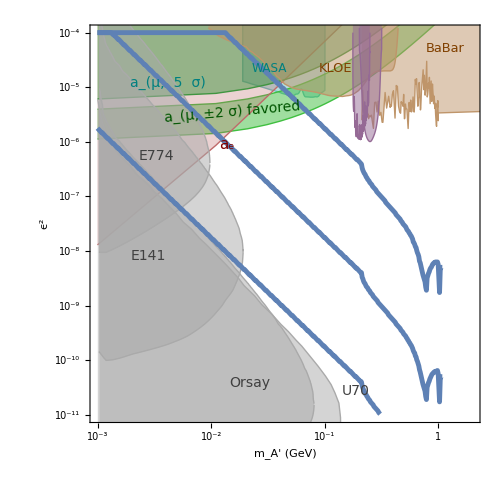

```mathematica
Show[comboFromRouvenFeb2014,gct1mm2pt2/.myThick->Sequence[Thickness[0.007]],gct10um2pt2/.myThick->Sequence[Thickness[0.007]],gct10cm2pt2/.myThick->Sequence[Thickness[0.007]]]
```

```mathematica
γcτ[0.05,10^-4.0,2.2]
NAprimeProduced[ee,BS,2.2,Full,FullTri][0.05, 10^-4.0]
```

7.13697 MM

200.035

### 2D vertex + resonance search Functions & Plots

```mathematica
PlotSignificance[mode_,E0_,fakeFunction_,Run_,BkgMode_:FullTri,vtxcutscale_:1, lumiBoost_:1, massOpt_:1,vtxEff_:0.7,trkEff_:0.85][m_,ϵ_]:=VtxSignificance[mode,E0,Run,BkgMode][fakeFunction,m,ϵ,
EndBinZ[mode,E0,Run,BkgMode][fakeFunction,m] MM*vtxcutscale, lumiBoost, massOpt,vtxEff,trkEff];
```

```mathematica
(* significanceGrid[E0_,fakeFunction_,Run_,vtxcutscale_:1, lumiBoost_:1, massOpt_:1,vtxEff_:0.7,trkEff_:0.85]:=Flatten[Table[{m,logϵ2,PlotSignificance[E0,fakeFunction,Run,vtxcutscale, lumiBoost, massOpt,vtxEff,trkEff][m,10^(logϵ2/2)]},{m,minMass,maxMass,step},{logϵ2,-10.5,-6.0,.1}],1]; *)
significanceGrid[mode_,E0_,fakeFunction_,Run_,BkgMode_:BH,vtxcutscale_:1, lumiBoost_:1, massOpt_:1,vtxEff_:0.7,trkEff_:0.85]:=Flatten[Table[{m,logϵ2,PlotSignificance[mode,E0,fakeFunction,Run,BkgMode,vtxcutscale, lumiBoost, massOpt,vtxEff,trkEff][m,10^(logϵ2/2)]},{m,minMass,maxMass,step},{logϵ2,-10.5,-6,.1}],1];

(*  significanceGridCombined[Run_,vtxcutscale_:1, lumiBoost_:1, massOpt_:1,vtxEff_:0.7,trkEff_:0.85]:=Flatten[Table[{m,logϵ2,((PlotSignificance[1.1,FakeFraction[1.1,10],Run,vtxcutscale, lumiBoost, massOpt,vtxEff,trkEff][m,10^(logϵ2/2)])^2+(PlotSignificance[2.2,FakeFraction[2.2,10],Run,vtxcutscale, lumiBoost, massOpt,vtxEff,trkEff][m,10^(logϵ2/2)])^2+(PlotSignificance[6.6,FakeFraction[6.6,10],Run,vtxcutscale, lumiBoost, massOpt,vtxEff,trkEff][m,10^(logϵ2/2)])^2)^(1/2)},{m,minMass,maxMass,step},{logϵ2,-10.5,-6,.1}],1]; *)
(*significanceGridCombined[Run_,vtxcutscale_:1, lumiBoost_:1, massOpt_:1,vtxEff_:0.7,trkEff_:0.85]:=Flatten[Table[{m,logϵ2,((PlotSignificance[1.1,FakeFraction[1.1,10],Run,vtxcutscale, lumiBoost, massOpt,vtxEff,trkEff][m,10^(logϵ2/2)])^2)^(1/2)},{m,minMass,maxMass,step},{logϵ2,-10.5,-6,.1}],1];*)
```

```mathematica
significanceGridCombined[Run_,BkgMode_:BH,vtxcutscale_:1, lumiBoost_:1, massOpt_:1,vtxEff_:0.7,trkEff_:0.85]:=Flatten[Table[{m,logϵ2,(If[m<0.07,(PlotSignificance[ee,1.1,FakeFraction[1.1,10],Run,BkgMode,vtxcutscale, lumiBoost, massOpt,vtxEff,trkEff][m,10^(logϵ2/2)])^2,0]+If[m<0.11,(PlotSignificance[ee,2.2,FakeFraction[2.2,10],Run,BkgMode,vtxcutscale, lumiBoost, massOpt,vtxEff,trkEff][m,10^(logϵ2/2)])^2,0]+If[m>0.07,(PlotSignificance[ee,6.6,FakeFraction[6.6,10],Run,BkgMode,vtxcutscale, lumiBoost, massOpt,vtxEff,trkEff][m,10^(logϵ2/2)])^2,0])^(1/2)},{m,minMass,maxMass,step},{logϵ2,-10.5,-6,.1}],1];
```

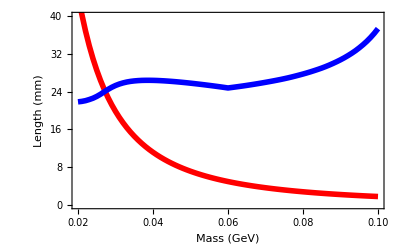

```mathematica
gctPlot2pt2=ListPlot[Table[{m,γcτ[m,10^-4,2.2]/MM},{m,0.02,0.10,0.001}],PlotRange->{{0.02,0.1},{0,40}},PlotStyle->{Red,Thickness[0.01]},Joined->True,Frame->True,FrameLabel->{"Mass (GeV)","Length (mm)"},LabelStyle->16];
endBin2pt2=ListPlot[Table[{m,EndBinZ[ee,2.2,Full][FakeFraction[2.2,10],m]},{m,0.02,0.10,0.001}],Joined->True,PlotStyle->{Blue,Thickness[0.01]},PlotRange->{{0.02,0.1},{0,40}},Frame->True,FrameLabel->{"Mass (GeV)","Length (mm)"},LabelStyle->16];
Show[gctPlot2pt2,endBin2pt2]
```

InterpolatingFunction::dmval: Input value {0.05, -26.9688} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.051, -26.138} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.052, -24.1175} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

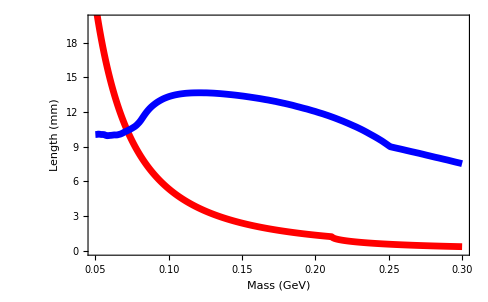

```mathematica
gctPlot6pt6=ListPlot[Table[{m,γcτ[m,10^-4,6.6]/MM},{m,0.05,0.30,0.001}],PlotRange->{{0.05,0.3},{0,20}},PlotStyle->{Red,Thickness[0.01]},Joined->True,Frame->True,FrameLabel->{"Mass (GeV)","Length (mm)"},LabelStyle->16];
endBin6pt6=ListPlot[Table[{m,EndBinZ[ee,6.6,Full][FakeFraction[6.6,10],m]},{m,0.05,0.30,0.001}],Joined->True,PlotStyle->{Blue,Thickness[0.01]},PlotRange->{{0.05,0.3},{0,20}},Frame->True,FrameLabel->{"Mass (GeV)","Length (mm)"},LabelStyle->16];
Show[gctPlot6pt6,endBin6pt6]
```

InterpolatingFunction::dmval: Input value {0.017, 40.5097} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.017, 40.6023} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.017, 40.6044} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

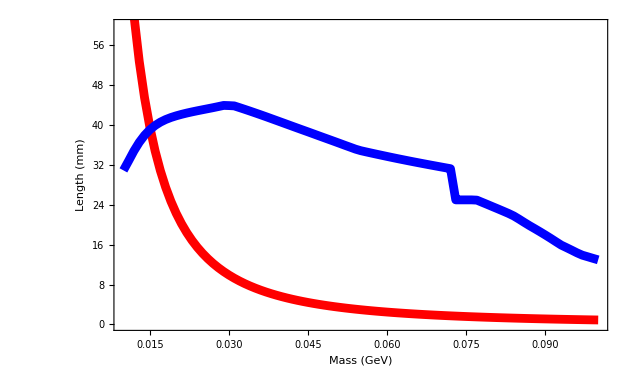

```mathematica
gctPlot1pt1=ListPlot[Table[{m,γcτ[m,10^-4,1.1]/MM},{m,0.01,0.10,0.001}],PlotRange->{{0.01,0.1},{0,60}},PlotStyle->{Red,Thickness[0.01]},Joined->True,Frame->True,FrameLabel->{"Mass (GeV)","Length (mm)"},LabelStyle->16];
endBin1pt1=ListPlot[Table[{m,EndBinZ[ee,1.1,Full][FakeFraction[1.1,10],m]},{m,0.01,0.10,0.001}],Joined->True,PlotStyle->{Blue,Thickness[0.01]},PlotRange->{{0.01,0.1},{0,20}},Frame->True,FrameLabel->{"Mass (GeV)","Length (mm)"},LabelStyle->16];
Show[gctPlot1pt1,endBin1pt1]
```

```mathematica
Table[{m,γcτ[m,10^-4,1.1]/MM},{m,0.01,0.10,0.001}]
```

{{0.01,89.2121},{0.011,73.729},{0.012,61.9528},{0.013,52.7882},{0.014,45.5164},{0.015,39.6498},{0.016,34.8485},{0.017,30.8692},{0.018,27.5346},{0.019,24.7125},{0.02,22.303},{0.021,20.2295},{0.022,18.4322},{0.023,16.8643},{0.024,15.4882},{0.025,14.2739},{0.026,13.1971},{0.027,12.2376},{0.028,11.3791},{0.029,10.6079},{0.03,9.91245},{0.031,9.28325},{0.032,8.71212},{0.033,8.19211},{0.034,7.71731},{0.035,7.28262},{0.036,6.88365},{0.037,6.51659},{0.038,6.17812},{0.039,5.86536},{0.04,5.57575},{0.041,5.30708},{0.042,5.05737},{0.043,4.82488},{0.044,4.60806},{0.045,4.40553},{0.046,4.21607},{0.047,4.03857},{0.048,3.87205},{0.049,3.71562},{0.05,3.56848},{0.051,3.42991},{0.052,3.29926},{0.053,3.17594},{0.054,3.0594},{0.055,2.94916},{0.056,2.84477},{0.057,2.74583},{0.058,2.65196},{0.059,2.56283},{0.06,2.47811},{0.061,2.39753},{0.062,2.32081},{0.063,2.24772},{0.064,2.17803},{0.065,2.11153},{0.066,2.04803},{0.067,1.98735},{0.068,1.92933},{0.069,1.87381},{0.07,1.82065},{0.071,1.76973},{0.072,1.72091},{0.073,1.67409},{0.074,1.62915},{0.075,1.58599},{0.076,1.54453},{0.077,1.50467},{0.078,1.46634},{0.079,1.42945},{0.08,1.39394},{0.081,1.35973},{0.082,1.32677},{0.083,1.29499},{0.084,1.26434},{0.085,1.23477},{0.086,1.20622},{0.087,1.17865},{0.088,1.15202},{0.089,1.12627},{0.09,1.10138},{0.091,1.07731},{0.092,1.05402},{0.093,1.03147},{0.094,1.00964},{0.095,0.988499},{0.096,0.968013},{0.097,0.948157},{0.098,0.928905},{0.099,0.910234},{0.1,0.892121}}

```mathematica
(* ListPlot[Table[{m,EndBinZ[ee,1.1,Full][FakeFraction[1.1,10],m]},{m,0.01,0.04,0.0005}],AxesLabel->{"Mass (GeV)","Z Cut (mm)"},LabelStyle->20] *)
```

```mathematica
Table[{m,EndBinZ[ee,1.1,Full][FakeFraction[1.1,10],m]},{m,0.01,0.10,0.001}]
```

InterpolatingFunction::dmval: Input value {0.017, 40.5097} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.017, 40.6023} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.017, 40.6044} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{0.01,30.9253},{0.011,32.8674},{0.012,34.8486},{0.013,36.5572},{0.014,37.959},{0.015,39.072},{0.016,39.9379},{0.017,40.6044},{0.018,41.1243},{0.019,41.5353},{0.02,41.874},{0.021,42.1671},{0.022,42.4281},{0.023,42.6634},{0.024,42.8838},{0.025,43.095},{0.026,43.303},{0.027,43.5116},{0.028,43.7343},{0.029,43.961},{0.03,43.9266},{0.031,43.8693},{0.032,43.5257},{0.033,43.1753},{0.034,42.8188},{0.035,42.4538},{0.036,42.0865},{0.037,41.7118},{0.038,41.3287},{0.039,40.9453},{0.04,40.5619},{0.041,40.1773},{0.042,39.7911},{0.043,39.4081},{0.044,39.0268},{0.045,38.648},{0.046,38.2636},{0.047,37.8759},{0.048,37.4939},{0.049,37.1126},{0.05,36.7295},{0.051,36.3433},{0.052,35.9514},{0.053,35.571},{0.054,35.1847},{0.055,34.873},{0.056,34.633},{0.057,34.3992},{0.058,34.1682},{0.059,33.9416},{0.06,33.7158},{0.061,33.4927},{0.062,33.2737},{0.063,33.0617},{0.064,32.8498},{0.065,32.6422},{0.066,32.4392},{0.067,32.2384},{0.068,32.0388},{0.069,31.8437},{0.07,31.6489},{0.071,31.4561},{0.072,31.2653},{0.073,25.},{0.074,25.},{0.075,25.},{0.076,25.},{0.077,24.9493},{0.078,24.5113},{0.079,24.0744},{0.08,23.6279},{0.081,23.1877},{0.082,22.7374},{0.083,22.2823},{0.084,21.7718},{0.085,21.1343},{0.086,20.4665},{0.087,19.8163},{0.088,19.2052},{0.089,18.5817},{0.09,17.9381},{0.091,17.277},{0.092,16.5913},{0.093,15.919},{0.094,15.4117},{0.095,14.8923},{0.096,14.3611},{0.097,13.8961},{0.098,13.586},{0.099,13.2689},{0.1,12.9597}}

```mathematica
TableForm[%625]
```

%625

```mathematica
twoSigmaVertexingTop[mode_,E0_,Run_,BkgMode_,mMin_,mMax_,nmStep_,epsMin_,epsMax_,nepsStep_,Boost_:1,nSigma_:2]:=Reap[Module[{m=mMin,mStep=(mMax-mMin)/nmStep},  While[m<mMax,Module[{eps=epsMax, epsStep=(epsMax-epsMin)/nepsStep},While[eps>epsMin,If[PlotSignificance [mode,E0,FakeFraction[E0,10],Run,BkgMode,1,Boost][10^m,10^eps]>nSigma,{Sow[{10^m,10^eps}](*,Print[{10^m,10^eps}]*),Break[]}];eps-=epsStep]];m+=mStep]]]
twoSigmaVertexingBottom[mode_,E0_,Run_,BkgMode_,mMin_,mMax_,nmStep_,epsMin_,epsMax_,nepsStep_,Boost_:1,nSigma_:2]:=Reap[Module[{m=mMin,,mStep=(mMax-mMin)/nmStep},  While[m<mMax,Module[{eps=epsMin,twoSig=False,  epsStep=(epsMax-epsMin)/nepsStep},While[eps<epsMax,If[PlotSignificance [mode,E0,FakeFraction[E0,10],Run,BkgMode,1,Boost][10^m,10^eps]>nSigma&& twoSig==False,{Sow[{10^m,10^eps}],Break[]}];eps+=epsStep]];m+=mStep]]]
```

```mathematica
(* twoSigmaVertexingTop[mode_,E0_,Run_,mMin_,mMax_,nmStep_,epsMin_,epsMax_,nepsStep_,Boost_:1,nSigma_:2]:=Reap[Module[{m=mMin,mStep=(mMax-mMin)/nmStep},  While[m<mMax,Module[{eps=epsMax, epsStep=(epsMax-epsMin)/nepsStep},While[eps>epsMin,If[PlotSignificance [mode,E0,FakeFraction[E0,10],Run,1,Boost][10^m,10^eps]>nSigma,{Sow[{10^m,10^eps}],Print[{10^m,10^eps}],Break[]}];{Print[{10^m,10^eps,PlotSignificance [mode,E0,FakeFraction[E0,10],Run,1,Boost][10^m,10^eps]}],eps-=epsStep}]];m+=mStep]]] *)
```

```mathematica
reachTop[mode_,E0_,Run_,BkgMode_,mMin_,mMax_,epsMin_,epsMax_,Boost_:1,nSigma_:2]:=Flatten[Drop[twoSigmaVertexingTop[mode,E0,Run,BkgMode,Log[10,mMin],Log[10,mMax],npoints,Log[10,epsMin],Log[10,epsMax],npoints,Boost,nSigma],1],2]; 
reachBottom[mode_,E0_,Run_,BkgMode_,mMin_,mMax_,epsMin_,epsMax_,Boost_:1,nSigma_:2]:=Flatten[Drop[twoSigmaVertexingBottom[mode,E0,Run,BkgMode,Log[10,mMin],Log[10,mMax],npoints,Log[10,epsMin],Log[10,epsMax],npoints,Boost,nSigma],1],2];
vertexReachPlot[top_,bottom_]:=ListLogLogPlot[Join[Prepend[top,bottom[[1]]],Reverse[bottom]],Joined->True,PlotStyle->myThick]
vertexReachTable[top_,bottom_]:=Join[Prepend[top,bottom[[1]]],Reverse[bottom]]
```

```mathematica
mMin[1.1]=0.01;
mMax[1.1]=0.1;
mMin[2.2]=0.02;
mMax[2.2]=0.15;
mMin[4.4]=0.04;
mMax[4.4]=0.25;
mMin[6.6]=0.05;
mMax[6.6]=0.5;
inRange[E0_,m_]:=If[(m>mMin[E0] && m<mMax[E0]),1.0,0.0];
inRange[1.1,0.09];
```

```mathematica
combinedVertexingSignificance [RunList_,BoostList_,m_,eps_]:=(Sum[If[inRange[RunList[[i]][[2]],10^m]==1,(PlotSignificance[RunList[[i]][[1]],RunList[[i]][[2]],FakeFraction[RunList[[i]][[2]],10],Full,FullTri,1,BoostList[[i]]][10^m,10^eps])^2,0],{i,Length[RunList]}])^(1/2)
```

```mathematica
twoSigmaCombinedVertexingTop[RunList_,mMin_,mMax_,nmStep_,epsMin_,epsMax_,nepsStep_,BoostList_,nSigma_:2]:=Reap[Module[{m=mMin,mStep=(mMax-mMin)/nmStep},  While[m<mMax,Module[{eps=epsMax, epsStep=(epsMax-epsMin)/nepsStep},While[eps>epsMin,If[combinedVertexingSignificance[RunList,BoostList,m,eps]>nSigma,{Sow[{10^m,10^eps}](*,Print[{10^m,10^eps}]*),Break[]}];eps-=epsStep]];m+=mStep]]];
twoSigmaCombinedVertexingBottom[RunList_,mMin_,mMax_,nmStep_,epsMin_,epsMax_,nepsStep_,BoostList_,nSigma_:2]:=Reap[Module[{m=mMin,,mStep=(mMax-mMin)/nmStep},  While[m<mMax,Module[{eps=epsMin,twoSig=False,  epsStep=(epsMax-epsMin)/nepsStep},While[eps<epsMax,If[combinedVertexingSignificance[RunList,BoostList,m,eps]>nSigma&& twoSig==False,{Sow[{10^m,10^eps}],Break[]}];eps+=epsStep]];m+=mStep]]];
```

```mathematica
reachComboTop[RunList_,mMin_,mMax_,epsMin_,epsMax_,BoostList_,nSigma_:2]:=Flatten[Drop[twoSigmaCombinedVertexingTop[RunList,Log[10,mMin],Log[10,mMax],npoints,Log[10,epsMin],Log[10,epsMax],npoints,BoostList,nSigma],1],2]; 
reachComboBottom[RunList_,mMin_,mMax_,epsMin_,epsMax_,BoostList_,nSigma_:2]:=Flatten[Drop[twoSigmaCombinedVertexingBottom[RunList,Log[10,mMin],Log[10,mMax],npoints,Log[10,epsMin],Log[10,epsMax],npoints,BoostList,nSigma],1],2];
```

InterpolatingFunction::dmval: Input value {0.0147147, 40.2012} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0147147, 40.385} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0147147, 40.3944} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0147147, 40.2012} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0147147, 40.385} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0147147, 40.3944} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

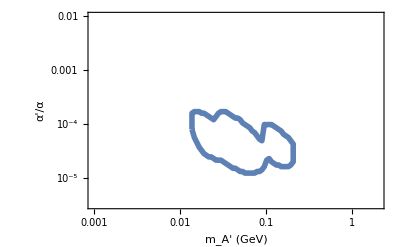

```mathematica
npoints=50;(*  number of points to scan in epsilon & mass  *)
VtxLumi={1,3,2};
VtxRuns={{ee,1.1},{ee,2.2},{ee,6.6}};
 botComboProposal=reachComboBottom[VtxRuns,0.01,0.25,10^(-10/2),10^(-7/2),VtxLumi]  ;
 topComboProposal=reachComboTop[VtxRuns,0.01,0.25,10^(-10/2),10^(-7/2),VtxLumi];
  plotComboProposal=vertexReachPlot[topComboProposal,botComboProposal]; 
Show[mylegendplot2,plotComboProposal/.myThick->Sequence[Thickness[0.01]]]
```

```mathematica
npoints=50;(*  number of points to scan in epsilon & mass  *)
VtxLumi={1,1,2};
VtxRuns={{ee,1.1},{ee,2.2},{ee,4.4}};
 botCombo2015=reachComboBottom[VtxRuns,0.01,0.25,10^(-10/2),10^(-7/2),VtxLumi]  ;
 topCombo2015=reachComboTop[VtxRuns,0.01,0.25,10^(-10/2),10^(-7/2),VtxLumi];
 plotCombo2015=vertexReachPlot[topCombo2015,botCombo2015];
Show[mylegendplot2,plotCombo2015/.myThick->Sequence[Thickness[0.01]]]
```

InterpolatingFunction::dmval: Input value {0.0147147, 40.2012} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0147147, 40.385} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0147147, 40.3944} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0147147, 40.2012} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0147147, 40.385} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0147147, 40.3944} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
vertexReachTable[topCombo2015,botCombo2015]//N
```

{{0.0137973,0.0000794328},{0.0137973,0.000158489},{0.0147147,0.000169824},{0.0156932,0.000169824},{0.0167367,0.000169824},{0.0178496,0.000158489},{0.0190365,0.000158489},{0.0203024,0.000147911},{0.0216524,0.000138038},{0.0230922,0.000128825},{0.0246277,0.000112202},{0.0262653,0.000104713},{0.0280118,0.000104713},{0.0298744,0.000128825},{0.0318609,0.000138038},{0.0339795,0.000138038},{0.036239,0.000138038},{0.0386487,0.000128825},{0.0412186,0.000120226},{0.0439595,0.000120226},{0.0468825,0.000112202},{0.05,0.000104713},{0.0533247,0.0000977237},{0.0568706,0.0000977237},{0.0606522,0.000120226},{0.0646852,0.000128825},{0.0689865,0.000128825},{0.0735737,0.000128825},{0.078466,0.000120226},{0.0836836,0.000112202},{0.0892481,0.000112202},{0.0951827,0.000104713},{0.101512,0.0000977237},{0.108262,0.0000912011},{0.115461,0.0000851138},{0.123138,0.0000794328},{0.131326,0.000074131},{0.140059,0.0000691831},{0.149372,0.000060256},{0.159305,0.0000524807},{0.169898,0.0000457088},{0.181195,0.0000346737},{0.181195,0.0000229087},{0.169898,0.0000186209},{0.159305,0.0000162181},{0.149372,0.0000151356},{0.140059,0.0000141254},{0.131326,0.0000141254},{0.123138,0.0000141254},{0.115461,0.0000141254},{0.108262,0.0000141254},{0.101512,0.0000141254},{0.0951827,0.0000151356},{0.0892481,0.0000151356},{0.0836836,0.0000162181},{0.078466,0.0000162181},{0.0735737,0.000017378},{0.0689865,0.000017378},{0.0646852,0.000017378},{0.0606522,0.000017378},{0.0568706,0.000017378},{0.0533247,0.0000186209},{0.05,0.0000186209},{0.0468825,0.0000186209},{0.0439595,0.0000186209},{0.0412186,0.0000199526},{0.0386487,0.0000199526},{0.036239,0.0000199526},{0.0339795,0.0000199526},{0.0318609,0.0000199526},{0.0298744,0.0000213796},{0.0280118,0.0000213796},{0.0262653,0.0000213796},{0.0246277,0.0000229087},{0.0230922,0.0000245471},{0.0216524,0.0000245471},{0.0203024,0.0000263027},{0.0190365,0.0000281838},{0.0178496,0.0000323594},{0.0167367,0.0000371535},{0.0156932,0.0000457088},{0.0147147,0.0000562341},{0.0137973,0.0000794328}}

```mathematica
npoints=50;(*  number of points to scan in epsilon & mass  *)
VtxLumi={1,1};
VtxRuns={{ee,1.1},{ee,2.2}};
 botCombo1gev2gev2015=reachComboBottom[VtxRuns,0.01,0.25,10^(-10/2),10^(-7/2),VtxLumi]  ;
 topCombo1gev2gev2015=reachComboTop[VtxRuns,0.01,0.25,10^(-10/2),10^(-7/2),VtxLumi];
```

InterpolatingFunction::dmval: Input value {0.0147147, 40.2012} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0147147, 40.385} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0147147, 40.3944} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0147147, 40.2012} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0147147, 40.385} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0147147, 40.3944} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

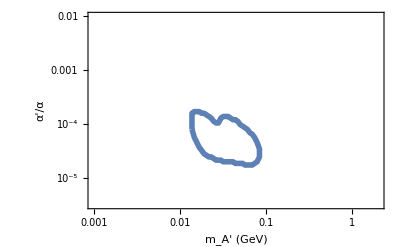

```mathematica
plotCombo1gev2gev2015=vertexReachPlot[topCombo1gev2gev2015,botCombo1gev2gev2015];
Show[mylegendplot2,plotCombo1gev2gev2015/.myThick->Sequence[Thickness[0.01]]]
```

InterpolatingFunction::dmval: Input value {0.0147147, 40.2012} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0147147, 40.385} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0147147, 40.3944} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0147147, 40.2012} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0147147, 40.385} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0147147, 40.3944} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

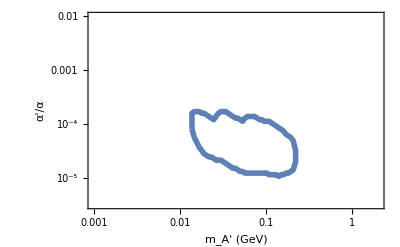

```mathematica
npoints=50;(*  number of points to scan in epsilon & mass  *)
VtxLumi={1,3,4,3};
VtxRuns={{ee,1.1},{ee,2.2},{ee,4.4},{ee,6.6}};
 botCombo2017=reachComboBottom[VtxRuns,0.01,0.25,10^(-10/2),10^(-7/2),VtxLumi]  ;
 topCombo2017=reachComboTop[VtxRuns,0.01,0.25,10^(-10/2),10^(-7/2),VtxLumi];
  plotCombo2017=vertexReachPlot[topCombo2017,botCombo2017]; 
Show[mylegendplot2,plotCombo2017/.myThick->Sequence[Thickness[0.01]]]
```

```mathematica
(*  vertexReachPlotAlt[top_,bottom_]:=ListLogLogPlot[{bottom,top},PlotStyle->myThick,Joined->True,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.3],Green]];
plotComboProposalAlt=vertexReachPlotAlt[topComboProposal,botComboProposal];
Show[mylegendplot2,plotComboProposalAlt/.myThick->Sequence[Thickness[0.01]]]    *)
```

```mathematica
(*   npoints=100;(*  number of points to scan in epsilon & mass  *)
VtxLumi={4*3,4*3};
VtxRuns={{ee,2.2},{ee,6.6}};
 botCombo3Months=reachComboBottom[VtxRuns,0.01,0.25,10^(-10/2),10^(-7/2),VtxLumi]  ;
 topCombo3Months=reachComboTop[VtxRuns,0.01,0.25,10^(-10/2),10^(-7/2),VtxLumi];  *)
```

```mathematica
(*    plotCombo3Months=vertexReachPlotAlt[topCombo3Months,botCombo3Months];
Show[mylegendplot2,plotCombo3Months/.myThick->Sequence[Thickness[0.001]]]  *)
```

InterpolatingFunction::dmval: Input value {0.0147147, 40.2012} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0147147, 40.385} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0147147, 40.3944} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0147147, 40.2012} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0147147, 40.385} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0147147, 40.3944} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

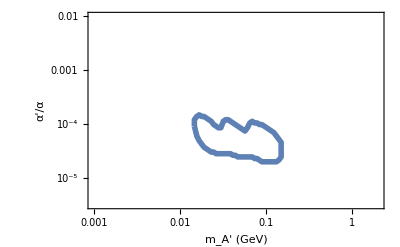

```mathematica
npoints=50;(*  number of points to scan in epsilon & mass  *)
VtxLumi={1,1,2};
VtxRuns={{ee,1.1},{ee,2.2},{ee,4.4}};
 botCombo2015Evidence=reachComboBottom[VtxRuns,0.01,0.25,10^(-10/2),10^(-7/2),VtxLumi,4.5]  ;
 topCombo2015Evidence=reachComboTop[VtxRuns,0.01,0.25,10^(-10/2),10^(-7/2),VtxLumi,4.5];
  plotCombo2015Evidence=vertexReachPlot[topCombo2015Evidence,botCombo2015Evidence]; 
Show[mylegendplot2,plotCombo2015Evidence/.myThick->Sequence[Thickness[0.01]]]
```

```mathematica
npoints=50;(*  number of points to scan in epsilon & mass  *)
VtxLumi={1,3,4,3};
VtxRuns={{ee,1.1},{ee,2.2},{ee,4.4},{ee,6.6}};
 botCombo2017Evidence=reachComboBottom[VtxRuns,0.01,0.25,10^(-10/2),10^(-7/2),VtxLumi,4.5]  ;
 topCombo2017Evidence=reachComboTop[VtxRuns,0.01,0.25,10^(-10/2),10^(-7/2),VtxLumi,4.5];
```

InterpolatingFunction::dmval: Input value {0.0147147, 40.2012} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0147147, 40.385} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0147147, 40.3944} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0147147, 40.2012} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0147147, 40.385} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0147147, 40.3944} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

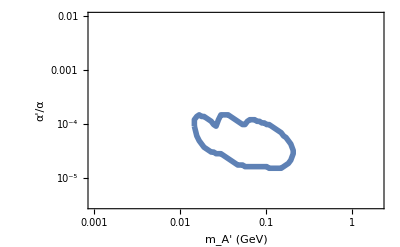

```mathematica
plotCombo2017Evidence=vertexReachPlot[topCombo2017Evidence,botCombo2017Evidence]; 
Show[mylegendplot2,plotCombo2017Evidence/.myThick->Sequence[Thickness[0.01]]]
```

InterpolatingFunction::dmval: Input value {0.101512, 40.3655} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.101512, 41.7326} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.101512, 41.9178} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.101512, 40.3655} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.101512, 41.7326} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.101512, 41.9178} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

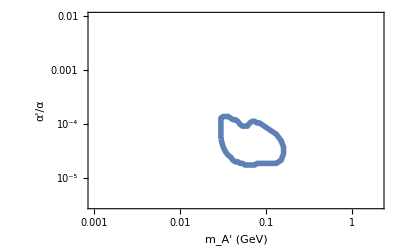

```mathematica
npoints=50;(*  number of points to scan in epsilon & mass  *)
VtxLumi={1,1};
VtxRuns={{ee,2.2},{ee,4.4}};
 botCombo2015with4pt4=reachComboBottom[VtxRuns,0.01,0.25,10^(-10/2),10^(-7/2),VtxLumi]  ;
 topCombo2015with4pt4=reachComboTop[VtxRuns,0.01,0.25,10^(-10/2),10^(-7/2),VtxLumi];
 plotCombo2015with4pt4=vertexReachPlot[topCombo2015with4pt4,botCombo2015with4pt4];
Show[mylegendplot2,plotCombo2015with4pt4/.myThick->Sequence[Thickness[0.01]]]
```

InterpolatingFunction::dmval: Input value {0.101512, 40.3655} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.101512, 41.7326} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.101512, 41.9178} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.101512, 40.3655} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.101512, 41.7326} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.101512, 41.9178} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

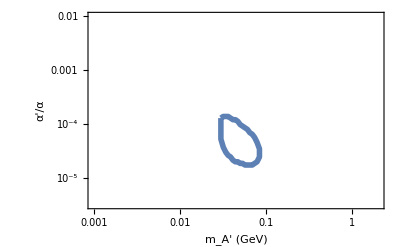

```mathematica
npoints=50;(*  number of points to scan in epsilon & mass  *)
VtxLumi={1};
VtxRuns={{ee,2.2}};
 botCombo2pt2=reachComboBottom[VtxRuns,0.01,0.25,10^(-10/2),10^(-7/2),VtxLumi]  ;
 topCombo2pt2=reachComboTop[VtxRuns,0.01,0.25,10^(-10/2),10^(-7/2),VtxLumi];
ee2pt2GeVVertex=vertexReachPlot[botCombo2pt2,topCombo2pt2];
Show[mylegendplot2,ee2pt2GeVVertex/.myThick->Sequence[Thickness[0.01]]]
```

InterpolatingFunction::dmval: Input value {0.0144544, 40.0692} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0144544, 40.0745} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0144544, 40.0692} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0144544, 40.0745} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

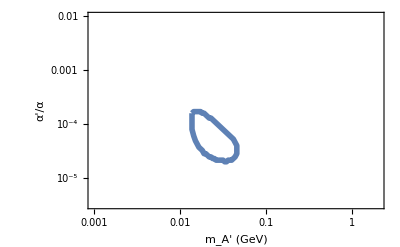

```mathematica
npoints=50;(*  number of points to scan in epsilon & mass  *)
VtxLumi={1};
VtxRuns={{ee,1.1}};
 botCombo1pt1=reachComboBottom[VtxRuns,0.01,0.1,10^(-10/2),10^(-7/2),VtxLumi]  ;
 topCombo1pt1=reachComboTop[VtxRuns,0.01,0.1,10^(-10/2),10^(-7/2),VtxLumi];
ee1pt1GeVVertex=vertexReachPlot[botCombo1pt1,topCombo1pt1];
Show[mylegendplot2,ee1pt1GeVVertex/.myThick->Sequence[Thickness[0.01]]]
```

### Statistics & Reach Plots

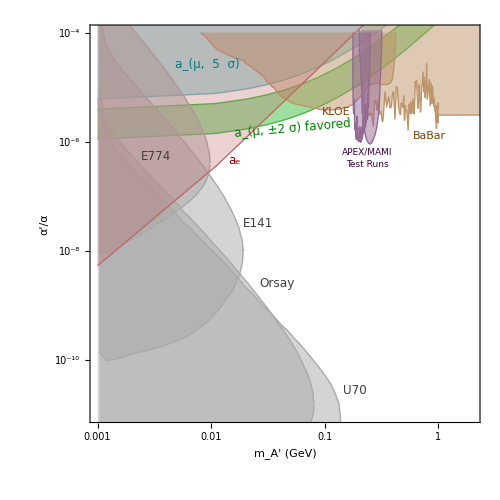
```mathematica
mycomboplot2=-Graphics-;
```

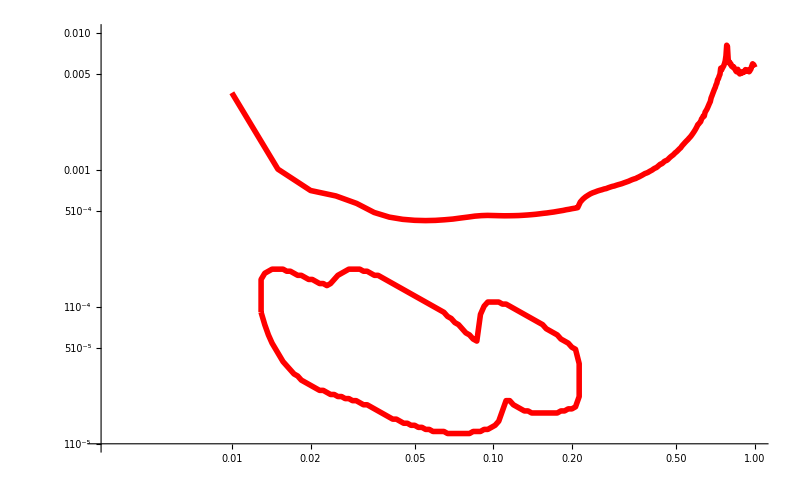
```mathematica
bhPlusRadPhase1=-Graphics-;
```

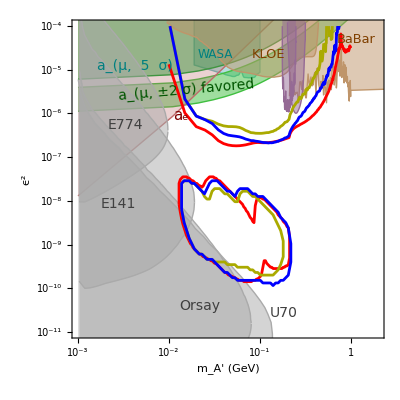

```mathematica
p=Show[comboFromRouvenFeb2014,
bhPlusRadPhase1,
(* ee2pt2GeVBumpHunt/.myThick->Sequence[Thickness[0.005],Dotted,Purple], *)
(* eeCombinedBumpHuntBeam3Months/.myThick->Sequence[Thickness[0.005],Red], *)
eemumuCombinedBumpHunt2015/.myThick->Sequence[Thickness[0.005],Darker[Yellow]], 
 eemumuCombinedBumpHunt2017/.myThick->Sequence[Thickness[0.005],Blue], 
(*  ee6pt6GeVMuonBumpHunt1Month/.myThick->Sequence[Thickness[0.005],Darker[Green]], *)
(* plot2pt2Month/.myThick->Sequence[Thickness[0.005],Dashed,Yellow], *)
plotCombo2015/.myThick->Sequence[Thickness[0.005],Darker[Yellow]],  
plotCombo2017/.myThick->Sequence[Thickness[0.005],Blue], 
(* plotComboProposal/.myThick->Sequence[Thickness[0.005],Red], *)
(* plot6pt6MonthHalfSigma/.myThick->Sequence[Thickness[0.003],Dashed,Red],  *)
ImageSize->400]
Export[EXPDIR<>"ee2pt2GeV.pdf",p];
```

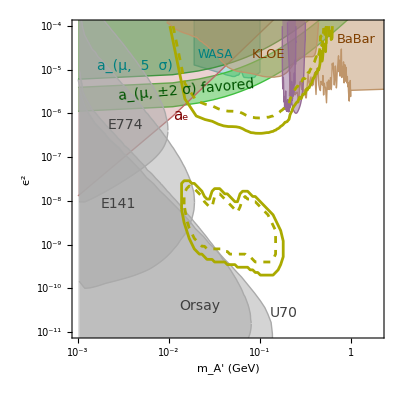

```mathematica
p=Show[comboFromRouvenFeb2014,

(* ee2pt2GeVBumpHunt/.myThick->Sequence[Thickness[0.005],Dotted,Purple], *)
(* eeCombinedBumpHuntBeam3Months/.myThick->Sequence[Thickness[0.005],Red], *)
eemumuCombinedBumpHunt2015Evidence/.myThick->Sequence[Thickness[0.005],Dashed,Darker[Yellow]], 
eemumuCombinedBumpHunt2015/.myThick->Sequence[Thickness[0.005],Darker[Yellow]], 
(*  ee6pt6GeVMuonBumpHunt1Month/.myThick->Sequence[Thickness[0.005],Darker[Green]], *)
(* plot2pt2Month/.myThick->Sequence[Thickness[0.005],Dashed,Yellow], *)
 plotCombo2015/.myThick->Sequence[Thickness[0.005],Darker[Yellow]],  
plotCombo2015Evidence/.myThick->Sequence[Thickness[0.005],Dashed,Darker[Yellow]],  
(* plotComboProposal/.myThick->Sequence[Thickness[0.005],Red], *)
(* plot6pt6MonthHalfSigma/.myThick->Sequence[Thickness[0.003],Dashed,Red],  *)
ImageSize->400]
Export[EXPDIR<>"ee2pt2GeV.pdf",p];
```

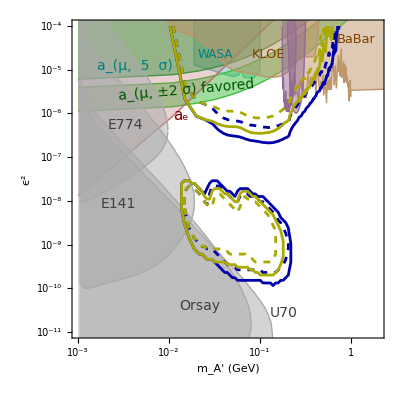

```mathematica
p=Show[comboFromRouvenFeb2014,
eemumuCombinedBumpHunt2017/.myThick->Sequence[Thickness[0.005],Darker[Blue]], 
eemumuCombinedBumpHunt2017Evidence/.myThick->Sequence[Thickness[0.005],Dashed,Darker[Blue]], 
eemumuCombinedBumpHunt2015Evidence/.myThick->Sequence[Thickness[0.005],Dashed,Darker[Yellow]], 
eemumuCombinedBumpHunt2015/.myThick->Sequence[Thickness[0.005],Darker[Yellow]], 
 plotCombo2017/.myThick->Sequence[Thickness[0.005],Darker[Blue]],  
plotCombo2017Evidence/.myThick->Sequence[Thickness[0.005],Dashed,Darker[Blue]],  
 plotCombo2015/.myThick->Sequence[Thickness[0.005],Darker[Yellow]],  
plotCombo2015Evidence/.myThick->Sequence[Thickness[0.005],Dashed,Darker[Yellow]],  
ImageSize->400]
Export[EXPDIR<>"ee2pt2GeV.pdf",p];
```

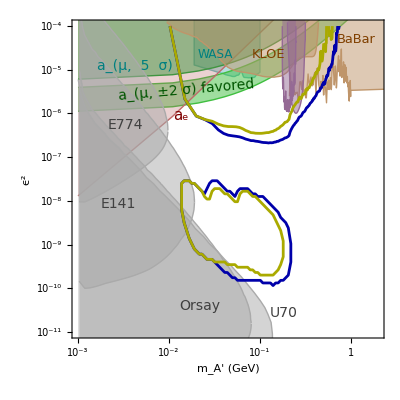

```mathematica
p=Show[comboFromRouvenFeb2014,
(* ee2pt2GeVBumpHunt/.myThick->Sequence[Thickness[0.005],Dotted,Purple], *)
(* eeCombinedBumpHuntBeam3Months/.myThick->Sequence[Thickness[0.005],Red], *)
eemumuCombinedBumpHunt2017/.myThick->Sequence[Thickness[0.005],Darker[Blue]], 
eemumuCombinedBumpHunt2015/.myThick->Sequence[Thickness[0.005],Darker[Yellow]], 
(*  ee6pt6GeVMuonBumpHunt1Month/.myThick->Sequence[Thickness[0.005],Darker[Green]], *)
(* plot2pt2Month/.myThick->Sequence[Thickness[0.005],Dashed,Yellow], *)
 plotCombo2017/.myThick->Sequence[Thickness[0.005],Darker[Blue]],  
plotCombo2015/.myThick->Sequence[Thickness[0.005],Darker[Yellow]],  
(* plotComboProposal/.myThick->Sequence[Thickness[0.005],Red], *)
(* plot6pt6MonthHalfSigma/.myThick->Sequence[Thickness[0.003],Dashed,Red],  *)
ImageSize->400]
Export[EXPDIR<>"ee2pt2GeV.pdf",p];
```

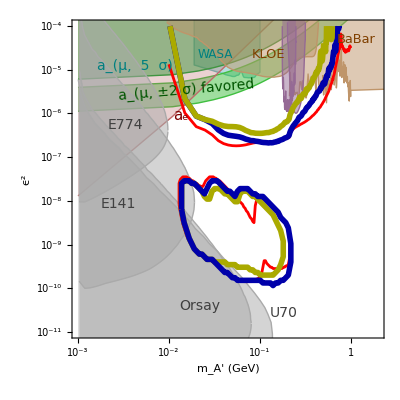

```mathematica
p=Show[comboFromRouvenFeb2014,
bhPlusRadPhase1,
(* ee2pt2GeVBumpHunt/.myThick->Sequence[Thickness[0.005],Dotted,Purple], *)
(* eeCombinedBumpHuntBeam3Months/.myThick->Sequence[Thickness[0.005],Red], *)
eemumuCombinedBumpHunt2017/.myThick->Sequence[Thickness[0.01],Darker[Blue]], 
eemumuCombinedBumpHunt2015/.myThick->Sequence[Thickness[0.01],Darker[Yellow]], 
(*  ee6pt6GeVMuonBumpHunt1Month/.myThick->Sequence[Thickness[0.005],Darker[Green]], *)
(* plot2pt2Month/.myThick->Sequence[Thickness[0.005],Dashed,Yellow], *)
plotCombo2015/.myThick->Sequence[Thickness[0.01],Darker[Yellow]],  
 plotCombo2017/.myThick->Sequence[Thickness[0.01],Darker[Blue]],  
(* plotComboProposal/.myThick->Sequence[Thickness[0.005],Red], *)
(* plot6pt6MonthHalfSigma/.myThick->Sequence[Thickness[0.003],Dashed,Red],  *)
ImageSize->400]
Export[EXPDIR<>"ee2pt2GeV.pdf",p];
```

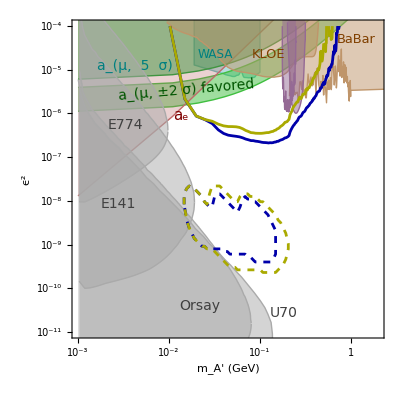

```mathematica
p=Show[comboFromRouvenFeb2014,
(* ee2pt2GeVBumpHunt/.myThick->Sequence[Thickness[0.005],Dotted,Purple], *)
(* eeCombinedBumpHuntBeam3Months/.myThick->Sequence[Thickness[0.005],Red], *)
eemumuCombinedBumpHunt2017/.myThick->Sequence[Thickness[0.005],Darker[Blue]], 
eemumuCombinedBumpHunt2015/.myThick->Sequence[Thickness[0.005],Darker[Yellow]], 
(*  ee6pt6GeVMuonBumpHunt1Month/.myThick->Sequence[Thickness[0.005],Darker[Green]], *)
(* plot2pt2Month/.myThick->Sequence[Thickness[0.005],Dashed,Yellow], *)
 plotCombo2015Evidence/.myThick->Sequence[Thickness[0.005],Dashed,Darker[Blue]],  
plotCombo2017Evidence/.myThick->Sequence[Thickness[0.005],Dashed,Darker[Yellow]],  
(* plotComboProposal/.myThick->Sequence[Thickness[0.005],Red], *)
(* plot6pt6MonthHalfSigma/.myThick->Sequence[Thickness[0.003],Dashed,Red],  *)
ImageSize->400]
Export[EXPDIR<>"ee2pt2GeV.pdf",p];
```

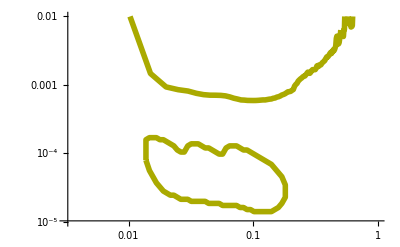

```mathematica
p=Show[eemumuCombinedBumpHunt2015/.myThick->Sequence[Thickness[0.01],Darker[Yellow]], 
plotCombo2015/.myThick->Sequence[Thickness[0.01],Darker[Yellow]],  
ImageSize->400]
Export[EXPDIR<>"ee2pt2GeV.pdf",p];
```

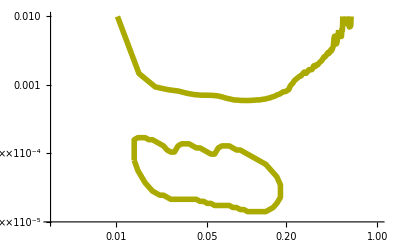
```mathematica
hps2015=-Graphics-;
```

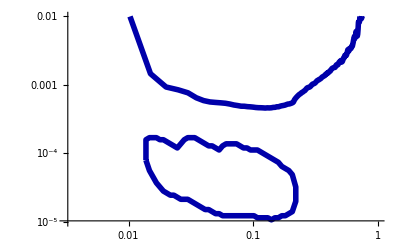

```mathematica
p=Show[eemumuCombinedBumpHunt2017/.myThick->Sequence[Thickness[0.01],Darker[Blue]], 
 plotCombo2017/.myThick->Sequence[Thickness[0.01],Darker[Blue]],  
ImageSize->400]
Export[EXPDIR<>"ee2pt2GeV.pdf",p];
```

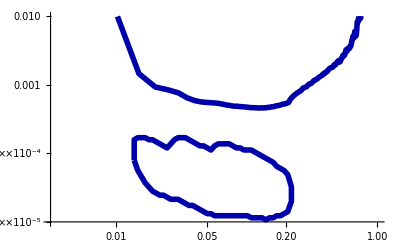
```mathematica
hps2017=-Graphics-;
```

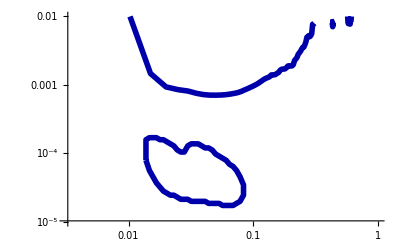

```mathematica
p=Show[eeCombinedBumpHunt1gev2gev2015/.myThick->Sequence[Thickness[0.01],Darker[Blue]], 
 plotCombo1gev2gev2015/.myThick->Sequence[Thickness[0.01],Darker[Blue]],  
ImageSize->400]
Export[EXPDIR<>"ee2pt2GeV.pdf",p];
```

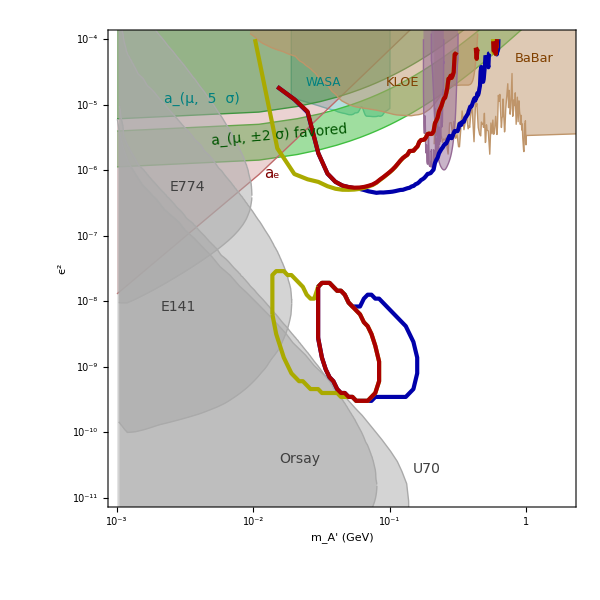

```mathematica
p=Show[comboFromRouvenFeb2014, 
(* eeCombinedBumpHuntBeam3Months/.myThick->Sequence[Thickness[0.005],Red], *)
eeCombinedBumpHuntwith4pt42015/.myThick->Sequence[Thickness[0.005],Darker[Blue]], 
eeCombinedBumpHunt1gev2gev2015/.myThick->Sequence[Thickness[0.005],Darker[Yellow]],
 ee2pt2GeVBumpHunt/.myThick->Sequence[Thickness[0.005],Darker[Red]], 
(*  ee6pt6GeVMuonBumpHunt1Month/.myThick->Sequence[Thickness[0.005],Darker[Green]], *)
 plotCombo2015with4pt4/.myThick->Sequence[Thickness[0.005],Darker[Blue]],  
plotCombo1gev2gev2015/.myThick->Sequence[Thickness[0.005],Darker[Yellow]],  
ee2pt2GeVVertex/.myThick->Sequence[Thickness[0.005],Darker[Red]],
(* plotComboProposal/.myThick->Sequence[Thickness[0.005],Red], *)
(* plot6pt6MonthHalfSigma/.myThick->Sequence[Thickness[0.003],Dashed,Red],  *)
ImageSize->600]
Export[EXPDIR<>"ee2pt2GeV.pdf",p];
```

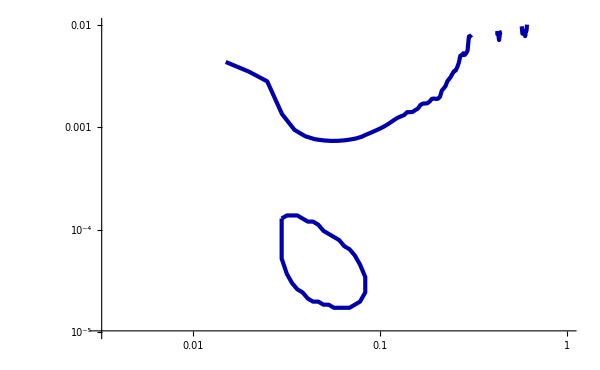

```mathematica
p=Show[
(* ee2pt2GeVBumpHunt/.myThick->Sequence[Thickness[0.005],Dotted,Purple], *)
(* eeCombinedBumpHuntBeam3Months/.myThick->Sequence[Thickness[0.005],Red], *)
ee2pt2GeVBumpHunt/.myThick->Sequence[Thickness[0.005],Darker[Blue]], 
(*  ee6pt6GeVMuonBumpHunt1Month/.myThick->Sequence[Thickness[0.005],Darker[Green]], *)
(* plot2pt2Month/.myThick->Sequence[Thickness[0.005],Dashed,Yellow], *)
 ee2pt2GeVVertex/.myThick->Sequence[Thickness[0.005],Darker[Blue]],  
(* plotComboProposal/.myThick->Sequence[Thickness[0.005],Red], *)
(* plot6pt6MonthHalfSigma/.myThick->Sequence[Thickness[0.003],Dashed,Red],  *)
ImageSize->600]
Export[EXPDIR<>"ee2pt2GeV.pdf",p];
```

```mathematica
(*bumphuntTable2pt2run2015=bumphuntTable[{ee,BS,2.2,Full,FullTri},1.0];*)
```

```mathematica
(*bumphuntTable1pt1run2015=bumphuntTable[{ee,BS,1.1,Full,FullTri},1.0];*)
```

```mathematica
(*bumphuntTable4pt4run2015=bumphuntTable[{ee,BS,4.4,Full,FullTri},2.0];*)
```

```mathematica
(*bumphuntTable4pt4run2017=bumphuntTable[{ee,BS,4.4,Full,FullTri},4.0];*)
```

```mathematica
(*bumphuntTable6pt6run2017=bumphuntTable[{ee,BS,6.6,Full,FullTri},3.0];*)
```

```mathematica
(*bumphuntTable2pt2run2017=bumphuntTable[{ee,BS,2.2,Full,FullTri},3.0];*)
```

```mathematica
(* bot6pt6run2017=reachBottom[ee,6.6,Full,FullTri,0.05,0.3,10^(-10/2),10^(-7/2),3,2];
top6pt6run2017=reachTop[ee,6.6,Full,FullTri,0.05,0.3,10^(-10/2),10^(-7/2),3,2.0];
table6pt6run2017=N[TableForm[vertexReachTable[top6pt6run2017,bot6pt6run2017]]]
*)
```

```mathematica
(*table6pt6run2017*)
```

```mathematica
(* bot4pt4run2017=reachBottom[ee,4.4,Full,FullTri,mMin[4.4],mMax[4.4],10^(-10/2),10^(-7/2),4,2];
top4pt4run2017=reachTop[ee,4.4,Full,FullTri,mMin[4.4],mMax[4.4],10^(-10/2),10^(-7/2),4,2.0];
table4pt4run2017=N[TableForm[vertexReachTable[top4pt4run2017,bot4pt4run2017]]]
*)
```

```mathematica
(* bot2pt2run2017=reachBottom[ee,2.2,Full,FullTri,mMin[2.2],mMax[2.2],10^(-10/2),10^(-7/2),3,2];
top2pt2run2017=reachTop[ee,2.2,Full,FullTri,mMin[2.2],mMax[2.2],10^(-10/2),10^(-7/2),3,2.0];
table2pt2run2017=N[TableForm[vertexReachTable[top2pt2run2017,bot2pt2run2017]]]
*)
```

```mathematica
(* bot2pt2run2015=reachBottom[ee,2.2,Full,FullTri,mMin[2.2],mMax[2.2],10^(-10/2),10^(-7/2),1,2];
top2pt2run2015=reachTop[ee,2.2,Full,FullTri,mMin[2.2],mMax[2.2],10^(-10/2),10^(-7/2),1,2.0];
table2pt2run2015=N[TableForm[vertexReachTable[top2pt2run2015,bot2pt2run2015]]]
*)
```

```mathematica
(* bot1pt1run2015=reachBottom[ee,1.1,Full,FullTri,mMin[1.1],mMax[1.1],10^(-10/2),10^(-7/2),1,2];
top1pt1run2015=reachTop[ee,1.1,Full,FullTri,mMin[1.1],mMax[1.1],10^(-10/2),10^(-7/2),1,2.0];
table1pt1run2015=N[TableForm[vertexReachTable[top1pt1run2015,bot1pt1run2015]]]
*)
```

```mathematica
(* bot4pt4run2015=reachBottom[ee,4.4,Full,FullTri,mMin[4.4],mMax[4.4],10^(-10/2),10^(-7/2),2,2];
top4pt4run2015=reachTop[ee,4.4,Full,FullTri,mMin[4.4],mMax[4.4],10^(-10/2),10^(-7/2),2,2.0];
table4pt4run2015=N[TableForm[vertexReachTable[top4pt4run2015,bot4pt4run2015]]]
*)
```